# Young Tableaux

José M. Martín-García

### 0. Comments

#### 0.1. Applications of Young tableaux

Combinatorics. It is possible to convert the set of all tableaux into a monoid in several forms:
	
	- The Schensted “bumping” algorithm and the Schützenberger “sliding” algorithm.
	- The relations with words developed by Knuth and Lascoux, and Schützenberger.
	- The Robinson-Schensted-Knuth correspondence between matrices with nonnegative integer entries and pairs of tableaux on the same shape.

These constructions are used for the combinatorial version of the Littlewood-Richardson rule, and for counting the numbers of tableaux of various types.

The algebra of symmetric functions.

Representations of the symmetric and general linear groups.

Tensor decompositions and symbolic tensor canonicalization.

Geometry of flag varieties.

#### 0.2. References

Main books, with emphasis in representation theory:

[Fulton 1997: Young Tableaux: With Applications to Representation Theory and Geometry]

[Sagan 1991: The Symmetric Group: Representations, Combinatorial Algorithms, and Symmetric Functions]

[James & Kerber 1981: Representation Theory of the Symmetric Group]

Collections of articles by experts:

[Wybourne papers]

[Ron King papers]

#### 0.3. Codes

Combinatorica has some support for Young tableaux, but very little, and rather slow.

A Mathematica package is [LieART], with focus on Lie algebras.

Wybourne and his students developed Schur, for computations with Young tableaux and many other aspects of representation theory. Version 5 was commercialized by Steve Christensen. Version 6 is free: [schur.sourceforge.net].

The Lie groups community has developed several codes, most notably [LiE], which includes Young tableaux capabilities.

MAGMA has Young tableaux capabilities in its [Combinatorics section].

GAP 4 has Young tableaux capabilities in its [Hecke extension], which is a port of [Specht]. I’m not sure this covers the general case.

### 1. Initialization

#### 1.1. BeginPackage

```mathematica
BeginPackage["Tableaux`"]
```

Tableaux`

#### 1.2. Usage messages

Notes:
	- A partition will be denoted in the code as par. Do not use part because that is something else in Mathematica.
	- A tableau will be denoted in the code as tab.
	- The object filling a box of a tableau is called a label. The word element is too general.

```mathematica
(* Some combinatorics and partitions *)
RepeatedSubsets::usage="";
PartitionQ::usage="PartitionQ[expr] returns True if expr is a partition of a nonnegative integer, i.e. a non-increasing list of nonnegative integers, and False otherwise.";
TransposePartition::usage="TransposePartition[par] returns the transpose of the partition par.";
HookFactor::usage="HookFactor[par] computes the hook factor of the partition par.";
InclusionOrder::usage="InclusionOrder[par1, par2]";
DominanceOrder::usage="DominanceOrder[par1, par2]";
LexicographicOrder::usage="LexicographicOrder[par1, par2]";
```

```mathematica
(* Main notation *)
Tableau::usage="Tableau is the head used to denote a Young tableau. Its arguments are lists containing the labels of consecutive rows of the tableau. A tableau is typeset as a left-justified and top-justified ragged array of boxes containing the labels (English style).";
TransposeTableau::usage="TransposeTableau[tab] returns a Young tableau obtained from tab by turning the rows into columns and viceversa.";
TableauWeight::usage="TableauWeight[tab, set] returns the weight of the tableau w.r.t. the given set of labels. This is a list of the respective numbers of occurrences of the elements of set in the tableau tab. TableauWeight[tab] returns the weight in the set of the union of all entries, sorted.";

(* General tableaux *)
TableauQ::usage="TableauQ[expr] returns True if expr is a valid tableau, that is an expression with head Tableau and arguments being lists of non-increasing length. It returns False otherwise.";
Tableaux::usage="Tableaux[par, set] returns the list of all tableaux, of shape given by the partition par, that can be constructed onto the given set of labels. Tableaux[par, n] for a positive integer n is interpreted as Tableaux[par, Range[n]]. Tableaux[par] is interpreted as Tableaux[par, Total[par]].";
NumberOfTableaux::usage="NumberOfTableaux[part, set] returns the number of tableaux, of shape given by the partition par, that can be constructed onto the given set of labels. NumberOfTableaux[par, n] for a positive integer is interpreted as NumberOfTableaux[par, Range[n]]. NumberOfTableaux[par] is interpreted as NumberOfTableaux[par, Total[par]].";

(* Disjoint tableaux *)
DisjointTableauQ::usage="DisjointTableauQ[expr] returns True if expr is a valid disjoint tableau, that is a Young tableau whose labels are all different. It returns False otherwise.";
DisjointTableaux::usage="DisjointTableaux[par, set] returns the list of all disjoint tableaux, of shape given by the partition par, that can be constructed onto the given set of labels. DisjointTableaux[par, n] for a positive integer n is interpreted as DisjointTableaux[par, Range[n]]. DisjointTableaux[par] is interpreted as DisjointTableaux[par, Total[par]].";
NumberOfDisjointTableaux::usage="NumberOfDisjointTableaux[par, set] returns the number of disjoint tableaux, of shape given by the partition par, that can be constructed onto the given set of labels. NumberOfDisjointTableaux[par, n] for a positive integer n is interpreted as NumberOfDisjointTableaux[par, Range[n]]. NumberOfDisjointTableaux[par] is interpreted as NumberOfDisjointTableaux[par, Total[par]].";

(* Semistandard tableaux *)
SemistandardTableauQ::usage="SemistandardTableauQ[tab] gives True if the labels of the Young tableau tab are sorted in each row and are sorted and different in each column. It returns False otherwise.";
SemistandardTableaux::usage="SemistandardTableaux[par, set] returns the list of all semistandard tableaux, of shape given by the partition par, that can be constructed onto the given set of labels. SemistandardTableaux[par, n] for a positive integer n is interpreted as SemistandardTableaux[par, Range[n]]. SemistandardTableaux[par] is interpreted as SemistandardTableaux[par, Total[par]].";
NumberOfSemistandardTableaux::usage="NumberOfSemistandardTableaux[par, set] returns the number of semistandard tableaux, of shape given by the partition par, that can be constructed onto the given set of labels. NumberOfSemistandardTableaux[par, n] for a positive integer n is interpreted as NumberOfSemistandardTableaux[par, Range[n]]. NumberOfSemistandardTableaux[par] is interpreted as NumberOfSemistandardTableaux[par, Total[par]].";

(* Standard tableaux *)
StandardTableauQ::usage="StandardTableauQ[tab] gives True if the labels of the Young tableau tab are all different, and the labels of each row and each column are sorted. It returns False otherwise.";
StandardTableaux::usage="StandardTableaux[par, set] returns the list of all standard tableaux, of shape given by the partition par, that can be constructed onto the given set of labels. StandardTableaux[par, n] for a positive integer n is interpreted as StandardTableaux[par, Range[n]]. StandardTableaux[par] is interpreted as StandardTableaux[par, Total[par]]. StandardTableaux[n] returns the list of all possible standard tableaux corresponding to the partitions of the integer n.";
NumberOfStandardTableaux::usage="NumberOfStandardTableaux[par, set] returns the number of standard tableaux, of shape given by the partition par, that can be constructed onto the given set of labels. NumberOfStandardTableaux[par, n] for a positive integer n is interpreted as NumberOfStandardTableaux[par, Range[n]]. NumberOfStandardTableaux[par] is interpreted as NumberOfStandardTableaux[par, Total[par]]. NumberOfStandardTableaux[n] returns the number of standard tableaux corresponding to all partitions of the integer n.";

(* Normal tableaux *)
NormalTableauQ::usage="NormalTableauQ[tab] gives True if the Young tableau tab is written in normal form, that is, its elements are sorted when joining all rows into a single list. It returns False otherwise.";
TableauOfPartition::usage="TableauOfPartition[part] returns a filled Tableau constructed from part which is the partition of a natural number. The entries of this tableau are the natural numbers sorted in their canonical order when reading the tableau from left to right";

(* Skew tableaux *)
Skew::usage="Skew is a symbol used to denote boxes of the interior partition of a skew tableau.";
```

```mathematica
(* Operations with tableaux *)
RowBump::usage="RowBump[tab, x, n] bumps the label x into the n-th row of the semistandard tableau tab. RowBump[tab, x] bumps the label into the first row of tab.";
SchenstedProduct::usage="SchenstedProduct[tab1, tab2] computes the Schensted product of the semistandard tableaux tab1 and tab2, by iteration of RowBump.";
SkewTableauSlide::usage="SkewTableauSlide[skewtab] removes the last Skew box of the skew tableau skewtab, using the sliding algorithm.";
RectifySkewTableau::usage="RectifySkewTableau[skewtab] removes all Skew boxes of the skew tableau skewtab, by iteration of SkewTableauSlide.";
```

```mathematica
(* Words and the plactic monoid *)
WordOfTableau::usage="";
TableauOfWord::usage="";
LatticeWordQ::usage="";
ReverseLatticeWordQ::usage="";
```

```mathematica
(* The LR rule *)
LRrule::usage="LRrule[tab1, tab2] decomposes the product of the Young tableaux tab1, tab2 as a sum (with multiplicities) of Young tableaux, using the Littlewood-Richardson rule.";
LRNumber::usage="LRNumber[par1, par2, tpar] returns the Littlewood-Richardson number associated to the decomposition of the partition tpar as a product of par1 and par2.";
LRProduct::usage="LRProduct[tabpar1, tabpar2] returns the product of partitions, using Tableau notation for them.";

(* Branching rules *)
Branch::usage="Branch[par] reduces the GL(d) representation par into a sum of representations of O(d).";
DimensionalRestriction::usage="DimensionalRestriction[par, dim] eliminates linear dependencies and trivial cases in the O(d) representation par.";
```

```mathematica
(* Symmetric polynomials and plethysms *)
PowerSumSymmetricPolynomial::usage="";
CompleteHomogeneousSymmetricPolynomial::usage="";
SchurPolynomial::usage="";
Plethysm::usage="";
```

#### 1.3. Begin private

```mathematica
Begin["`Private`"]
```

Tableaux`Private`

```mathematica
Names["Tableaux`*"]
```

{Branch,CompleteHomogeneousSymmetricPolynomial,DimensionalRestriction,DisjointTableauQ,DisjointTableaux,DominanceOrder,HookFactor,InclusionOrder,LatticeWordQ,LexicographicOrder,LRNumber,LRProduct,LRrule,NormalTableauQ,NumberOfDisjointTableaux,NumberOfSemistandardTableaux,NumberOfStandardTableaux,NumberOfTableaux,PartitionQ,Plethysm,PowerSumSymmetricPolynomial,RectifySkewTableau,RepeatedSubsets,ReverseLatticeWordQ,RowBump,SchenstedProduct,SchurPolynomial,SemistandardTableauQ,SemistandardTableaux,Skew,SkewTableauSlide,StandardTableauQ,StandardTableaux,Tableau,TableauOfPartition,TableauOfWord,TableauQ,TableauWeight,Tableaux,TransposePartition,TransposeTableau,WordOfTableau}

```mathematica
%//Length
```

42

```mathematica
$ContextPath
```

{Tableaux`,System`}

```mathematica
$Context
```

Tableaux`Private`

### 2. Partitions of an integer

#### 2.1. PartitionQ

A partition (abbreviated to par in the codes) of a nonnegative integer n is a list of nonincreasing nonnegative integers adding up to n. That is, we are dealing with **additive** partitions, and not with multiplicative partitions (more commonly known as factorizations). Note that partitions are naturally multisets, and could be also given in multiplicity-form, like FactorInteger does.

```mathematica
?PartitionQ
```

PartitionQ[expr] returns True if expr is a partition of a nonnegative integer, i.e. a non-increasing list of nonnegative integers, and False otherwise.

```mathematica
PartitionQ[par:{___Integer?NonNegative}]:=GreaterEqual@@par;
PartitionQ[_]:=False;
```

The empty list { } is a partition, the only partition of 0.

```mathematica
PartitionQ[{}]
```

True

QUESTION: Do we accept trailing zeros in partitions? The previous definition of PartitionQ does accept them:

```mathematica
PartitionQ[{2,2,1,0,0}]
```

True

Actually I now think that we must accept trailing zeros because in some cases we need to compare or sort partitions of different lengths, and then it is useful to keep the idea that two partitions coincide if they differ only by trailing zeros. We will see later that empty lists are accepted by the head Tableau, though they are immediately removed. Because partitions have head List we cannot automatically remove zeros.

#### 2.2. IntegerPartitions

```mathematica
?IntegerPartitions
```

RowBox[{"IntegerPartitions", "[", StyleBox["n", "TI"], "]"}] gives a list of all possible ways to partition the integer StyleBox["n", "TI"] into smaller integers. 
RowBox[{"IntegerPartitions", "[", RowBox[{StyleBox["n", "TI"], ",", StyleBox["k", "TI"]}], "]"}] gives partitions into at most StyleBox["k", "TI"] integers. 
RowBox[{"IntegerPartitions", "[", RowBox[{StyleBox["n", "TI"], ",", RowBox[{"{", StyleBox["k", "TI"], "}"}]}], "]"}] gives partitions into exactly StyleBox["k", "TI"] integers. 
RowBox[{"IntegerPartitions", "[", RowBox[{StyleBox["n", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["k", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["k", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] gives partitions into between SubscriptBox[StyleBox["k", "TI"], StyleBox["min", "TI"]] and SubscriptBox[StyleBox["k", "TI"], StyleBox["max", "TI"]] integers. 
RowBox[{"IntegerPartitions", "[", RowBox[{StyleBox["n", "TI"], ",", StyleBox["kspec", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["s", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["s", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] gives partitions involving only the SubscriptBox[StyleBox["s", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"IntegerPartitions", "[", RowBox[{StyleBox["n", "TI"], ",", StyleBox["kspec", "TI"], ",", StyleBox["sspec", "TI"], ",", StyleBox["m", "TI"]}], "]"}] limits the result to the first StyleBox["m", "TI"] partitions.

Starting version 6, there is the builtin function IntegerPartitions. This is an alternative implementation for the 2-arguments case:

```mathematica
If[$VersionNumber<6.0,
IntegerPartitions[n_Integer]:=IntegerPartitions[n,n];
IntegerPartitions[n_Integer?Negative,_]:={};
IntegerPartitions[0,_]:={{}};
IntegerPartitions[_,0]:={};
IntegerPartitions[n_Integer,1]:={Table[1,{n}]};
IntegerPartitions[n_Integer,m_Integer]:=Join[(Prepend[#,m]&)/@IntegerPartitions[n-m,m],IntegerPartitions[n,m-1]]
];
```

A partition identifies a Young diagram (also known as Ferrer diagram), which is not a Young tableau. The diagram is an unfilled tableau, giving the boxes structure, but not its labels. A tableau always has labels.

Partitions are formatted as standard lists. We do not format them as unfilled tableaux. We will actually allow later the syntax Tableau[4, 4, 2], but only for typesetting purposes. The code does not accept partitions with head Tableau.

```mathematica
IntegerPartitions[0]
```

{{}}

```mathematica
IntegerPartitions[1]
```

{{1}}

```mathematica
IntegerPartitions[2]
```

{{2},{1,1}}

```mathematica
IntegerPartitions[6]
```

{{6},{5,1},{4,2},{4,1,1},{3,3},{3,2,1},{3,1,1,1},{2,2,2},{2,2,1,1},{2,1,1,1,1},{1,1,1,1,1,1}}

```mathematica
PartitionQ/@%
```

{True,True,True,True,True,True,True,True,True,True,True}

Note that Mathematica's function accepts any rational input (this is because a third argument allows partitioning a rational into specified rationals), returning an empty list:

```mathematica
IntegerPartitions[-3]
```

{}

```mathematica
IntegerPartitions[5/2]
```

{}

#### 2.3. TransposePartition

A partition can be transposed (sometimes referred to as “conjugate” as well):

```mathematica
?TransposePartition
```

TransposePartition[par] returns the transpose of the partition par.

```mathematica
TransposePartition[Tableau[ints___Integer]]:=Tableau@@TransposePartition[{ints}];
TransposePartition[par:{___Integer}]:=Map[Count[Thread[par≥#],True]&,Range@Max[par,0]]
SetNumberOfArguments[TransposePartition,1];
Protect[TransposePartition];
```

Max[par, 0] is used to include the empty partition.

Note that zeros disappear under double transposition. It is not even clear that intermediate zeros should have been allowed in the first place, because they break the non-increasing condition of partitions, however we usually do not check input, to avoid the overhead:

```mathematica
TransposePartition[{2,1,0,1}]
```

{3,1}

```mathematica
TransposePartition[%]
```

{2,1,1}

```mathematica
TransposePartition[{}]
```

{}

#### 2.4. Counting partitions: PartitionsP

It seems there is no analytic formula for the number of partitions of an integer. However, Mathematica has such function:

```mathematica
IntegerPartitions[9]//Length
```

30

```mathematica
PartitionsP[9]
```

30

```mathematica
?PartitionsP
```

RowBox[{"PartitionsP", "[", StyleBox["n", "TI"], "]"}] gives the number RowBox[{StyleBox["p", "TI"], RowBox[{"(", StyleBox["n", "TI"], ")"}]}] of unrestricted partitions of the integer StyleBox["n", "TI"].

#### 2.5. HookFactor

A hook is a Γ-shape collection of boxes,defined by the position of the corner box, and going to the far right and far bottom in the given tableau. Do not confuse it with a “Garnir hook”, in which it has two corners (which are neighbours in a row).

Here the HookFactor of a partition is defined as the **inverse** of the product of its hook-lengths. The hook-length of a box of a diagram of a partition is the number of boxes to its right plus the number of boxes under it plus 1 the box itself. Each box of a diagram has a hook-length. For example the hook factor of the partition {n} is 1/n!

QUESTION: Wouldn’t it be more natural to work with the product of the hook-lengths instead of its inverse? It is a bit odd to define something which is always of the form 1/n. Actually, this formula is typically used as Total[par]!/product_of_hook_lengths, so perhaps what we should do is multiplying by Total[par]!, which is guaranteed to give an integer always.

Frobenius determinant of a list of integers, not necessarily a partition:

```mathematica
DET[{x_Integer}]:=1;
DET[{xs__Integer,x_Integer}]:=DET[{xs}]Times@@({xs}-x);
(* Special case to work with partition {} *)
DET[{}]:=1;
```

Rather efficient:

```mathematica
AbsoluteTiming[DET@Range[100]//N]
```

{0.00388,2.89648181359652×10^6782}

The hook factor  of a given partition:

```mathematica
?HookFactor
```

HookFactor[par] computes the hook factor of the partition par.

```mathematica
HookFactor[{n_Integer}]:=1/n!;
(* HookFactor[seq:({1}..)]:=1/Length[{seq}]!; *)
HookFactor[par_List]:=With[{tmppar=With[{n=Length[par]},par-Range[n]+n]},DET[tmppar]/Apply[Times,Factorial/@tmppar] 
];
```

Examples :

```mathematica
HookFactor[{3}]
```

1/6

```mathematica
HookFactor[{2,1}]
```

1/3

```mathematica
HookFactor[{1,1,1}]
```

1/6

```mathematica
HookFactor[{4}]
```

1/24

```mathematica
HookFactor[{3,1}]
```

1/8

```mathematica
HookFactor[{2,2}]
```

1/12

```mathematica
HookFactor[{2,1,1}]
```

1/8

```mathematica
HookFactor[{1,1,1,1}]
```

1/24

```mathematica
HookFactor[{5,4,1}]
```

1/12600

```mathematica
HookFactor[{}]
```

1

Trailing zeros are irrelevant:

```mathematica
HookFactor[{2,2,0,0,0}]
```

1/12

but increasing integers produce invalid Hood factors:

```mathematica
HookFactor[{2,0,1}]
```

0

```mathematica
HookFactor[{2,1,3}]
```

-1/144

A simple representation of the hook lengths:

```mathematica
HookLengthsRow[n_,trpar_List,{row_}]:=Take[trpar,n]+Reverse@Range[n]-row;
HookLengthsTableau[par_List]:=With[{trpar=TransposePartition[par]},Tableau@@MapIndexed[HookLengthsRow[#1,trpar,#2]&,par]];
```

```mathematica
HookLengthsTableau[{5,4,2}]
```

Tableau[{7,6,4,3,1},{5,4,2,1},{2,1}]

```mathematica
Times@@Flatten[List@@%]
```

40320

```mathematica
HookFactor[{5,4,2}]
```

1/40320

#### 2.6. RepeatedSubsets

```mathematica
?RepeatedSubsets
```

This is not a good name. It should be something like SubsetsWithRepetitions or better Multisets:

```mathematica
RepeatedSubsets[vars_List,k_]:=Apply[Union,repeatedsubsets[vars,k,#]&/@Range[Length[vars]]];
RepeatedSubsets[vars_List,1]:=List/@vars;
RepeatedSubsets[vars_List,0]:={};
repeatedsubsets[vars_List,k_,n_]:=Flatten/@Thread[List[vars[[n]],RepeatedSubsets[Drop[vars,n-1],k-1]]];
SetNumberOfArguments[RepeatedSubsets,{2,3}];
Protect[RepeatedSubsets];
```

```mathematica
RepeatedSubsets[{a,b},3]
```

{{a,a,a},{a,a,b},{a,b,b},{b,b,b}}

These are alternative ways of constructing them, but they go through intermediate cases that are potentially very large:

```mathematica
Subsets[{a,a,a,b,b,b},{3}]//DeleteDuplicates
```

{{a,a,a},{a,a,b},{a,b,b},{b,b,b}}

```mathematica
Sort/@Tuples[{a,b},{3}]//DeleteDuplicates
```

{{a,a,a},{a,a,b},{a,b,b},{b,b,b}}

The length of the result is the standard

```mathematica
Binomial[2+3-1,3]
```

4

#### 2.7. PartitionCorners

We now define the concept of partition corners: these are positions in the Young diagram of that partition such that they are at the end of the row and they do not have a box below them (hence they have hook-length 1).

```mathematica
cornerposition[{0,_},{_}]:=Sequence[];
cornerposition[{_,column_},{row_}]:={row,column};
PartitionCorners[par_List]:=MapIndexed[cornerposition,Transpose[{Differences[Append[par,0]],par}]]
```

Positions are denoted in the standard matrix-style of tableaux (English style).

```mathematica
PartitionCorners[{4,4,1}]
```

{{2,4},{3,1}}

#### 2.8. Ordering of partitions

There are three orders for the whole sets of partitions. We want to order partitions even if they have different lengths. The idea is that of padding with zeros on the right if needed before comparing them.

```mathematica
pars6=IntegerPartitions[6]
```

{{6},{5,1},{4,2},{4,1,1},{3,3},{3,2,1},{3,1,1,1},{2,2,2},{2,2,1,1},{2,1,1,1,1},{1,1,1,1,1,1}}

1) Inclusion order. This is the most restrictive. It is not a total order.

```mathematica
?InclusionOrder
```

InclusionOrder[par1, par2]

```mathematica
InclusionOrder[par1_List,par2_List]:=With[{l1=Length@par1,l2=Length@par2},
Which[
l1≤l2 &&And@@LessEqual@@@Transpose[{par1,par2[[Range[l1]]]}],1,
l2≤l1&&And@@LessEqual@@@Transpose[{par2,par1[[Range[l2]]]}],-1,
True,0
]
];
```

```mathematica
InclusionOrder[{2,1},{3,1}]
```

1

```mathematica
InclusionOrder[{2,2},{3,1}]
```

0

```mathematica
InclusionOrder[{3,3},{4,1}]
```

0

```mathematica
InclusionOrder[{4,1},{3,3}]
```

0

```mathematica
Outer[InclusionOrder,pars6,pars6,1,1]//TableForm
```

1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1

This is probably incorrectly programmed, because all results are trivial in that table.

2) Dominance order. It is not a total order either.

```mathematica
?DominanceOrder
```

DominanceOrder[par1, par2]

```mathematica
DominanceOrder[par1_List,par2_List]:=With[{l=Max[Length[par1],Length[par2]]},With[{p1=Accumulate@PadRight[par1,l],p2=Accumulate@PadRight[par2,l]},
Which[
p1===p2,0,
And@@LessEqual@@@Transpose[{p1,p2}],1,
And@@GreaterEqual@@@Transpose[{p1,p2}],-1,
True,0
]
]
];
```

```mathematica
DominanceOrder[{4,1,1},{3,3}]
```

0

```mathematica
DominanceOrder[{2,1},{3,1}]
```

1

```mathematica
DominanceOrder[{2,2},{3,1}]
```

1

```mathematica
DominanceOrder[{3,3},{4,1}]
```

0

```mathematica
DominanceOrder[{4,1},{3,3}]
```

0

For n >= 6 we see non-diagonal zeros:

```mathematica
Outer[DominanceOrder,pars6,pars6,1,1]//TableForm
```

0 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
1 | 0 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
1 | 1 | 0 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
1 | 1 | 1 | 0 | 0 | -1 | -1 | -1 | -1 | -1 | -1
1 | 1 | 1 | 0 | 0 | -1 | -1 | -1 | -1 | -1 | -1
1 | 1 | 1 | 1 | 1 | 0 | -1 | -1 | -1 | -1 | -1
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | -1 | -1 | -1
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | -1 | -1 | -1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | -1 | -1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | -1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0

Note that dominance order is always sign reversed under transposition of partitions.

The dominance order induces a lattice structure in the Young subgroups of the symmetric group. This plays a fundamental role in the representation theory of the symmetric group.

3) Lexicographic order. This is a total order (zero is returned only for coinciding partitions). It coindices with (0-right-padded) lexicographic order of lists in Mathematica.

```mathematica
LexicographicOrder
```

LexicographicOrder

```mathematica
LexicographicOrder[par1_List,par2_List]:=With[{l=Max[Length[par1],Length[par2]]},
Order[PadRight[par1,l],PadRight[par2,l]]
];
```

```mathematica
LexicographicOrder[{2,1},{3,1}]
```

1

```mathematica
LexicographicOrder[{2,2},{3,1}]
```

1

```mathematica
LexicographicOrder[{3,3},{4,1}]
```

1

```mathematica
LexicographicOrder[{4,1},{3,3}]
```

-1

```mathematica
Outer[LexicographicOrder,pars6,pars6,1,1]//TableForm
```

0 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
1 | 0 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
1 | 1 | 0 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
1 | 1 | 1 | 0 | -1 | -1 | -1 | -1 | -1 | -1 | -1
1 | 1 | 1 | 1 | 0 | -1 | -1 | -1 | -1 | -1 | -1
1 | 1 | 1 | 1 | 1 | 0 | -1 | -1 | -1 | -1 | -1
1 | 1 | 1 | 1 | 1 | 1 | 0 | -1 | -1 | -1 | -1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | -1 | -1 | -1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | -1 | -1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | -1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0

```mathematica
pars6=.
```

#### 2.9. Frobenius notation

This is a clever way to represent a partition, and is rather symmetric:

```mathematica
ToFrobeniusMatrix[par_?PartitionQ]:=Select[#-Range[Length[#]],Positive]&/@{par,TransposePartition[par]};
```

```mathematica
FromFrobeniusMatrix[{hors_,vers_}]:=With[{dl=Length[hors]},Join[hors+Range[dl],Drop[TransposePartition[vers+Range[dl]],dl]]
];
```

Example in page 1558 of Black, King and Wybourne 1983:

```mathematica
{6,5,2,1,1}//ToFrobeniusMatrix
```

{{5,3},{4,1}}

```mathematica
%//FromFrobeniusMatrix
```

{6,5,2,1,1}

```mathematica
{6,5,2,1,1}//TransposePartition
```

{5,3,2,2,2,1}

```mathematica
%//ToFrobeniusMatrix
```

{{4,1},{5,3}}

```mathematica
%//FromFrobeniusMatrix
```

{5,3,2,2,2,1}

### 3. Young tableaux

#### 3.0. Comments on the notions of tableau

We can visualize a partition as a 2D arrangement of boxes. Given a set of labels (Fulton calls this set an alphabet [m]={1,...,m} because he always has in mind these numeric labels), a Young tableau is a mapping from that set of boxes to that set of labels. In general the mapping is neither injective nor surjective. The sets of boxes and labels may have different cardinalities (including 0), though the number of boxes must be always finite. Fulton talks about a numbering of a tableau when the labels are all different, and a filling when they can be repeated.

There are different types of tableaux, and there is no agreement in the literature on how to name them. For example (copied from Fulton, page 2):

Young diagrams are also known as Ferrers diagrams or frames; sometimes dots are used instead of boxes, and sometimes, particularly in France, they are written upside down, in order not to offend Descartes. What we call tableaux are known variously as semistandard tableaux, or column-strict tableaux, or generalized Young tableaux (in which case our standard tableaux are just called tableaux). Combinatorialists also know them as column-strict reversed plane partitions; the "reversed" is in opposition to the case of decreasing rows and columns, which was studied first (and allows zero entries).

This is our current nomenclature:

- Any filling of a Young diagram (aka Young frame) is a tableau, with head Tableau.
- If the labels of a tableau are all different (checked with UnsameQ) then we call it a "disjoint tableau" (I have invented that name).
- If the columns are strictly sorted and the rows are sorted (but could contain repeated labels) then we call it a "semistandard tableau".
- If the tableau is disjoint and both the columns and rows are strictly sorted then we call it a "standard tableau".
- If the flattening of all rows gives a strictly sorted list of labels then we call it a "normal tableau". This could also be called a "first tableau" (in the lexicographic ordering of labels provided by Sort).

It would be nice to have a RandomXTableau function (X meaning any of the previous types). Combinatorica has one for standard tableaux, but it is rather complicated.

We now remove empty lists from Tableau:

```mathematica
Tableau[L___,{},R___]:=Tableau[L,R];
```

Any tableau defines a partition:

```mathematica
TableauPartition[tab_Tableau]:=Length/@List@@tab;
```

#### 3.1. Ordering of tableaux

The set of labels is always assumed to have a total order. There are two ways to interpret this. We could take the ordering of the input set, or we can declare that the ordering is always decided by Mathematica' s Sort function (that is, lexicographic order). Currently we take the latter approach, because it is simpler and faster.

The ordering of the labels of the set induces an ordering of the tableaux for a given partition shape. It compares succesive elements of the first row and then succesive rows, until one label differs. The comparison decides the ordering. If we use Sort for the labels then fortunately Sort also gives the right order for tableaux. The listing functions XTableaux will follow this ordering. In case we want to change the sorting function of labels, we shall use this driver:

```mathematica
LabelsSort=Sort;
```

That is, all functions using a list of labels will call first LabelsSort[labels] to bring the set to a canonical form. There is an important question here: what happens if we provide a set of labels with repeated elements? I have the impression that the function LabelsSort should be Union, and not just Sort. In other words, do we work with a set of labels or with a multiset of labels? QUESTION.

#### 3.2. Tableau and its formatting

```mathematica
?Tableau
```

Tableau is the head used to denote a Young tableau. Its arguments are lists containing the labels of consecutive rows of the tableau. A tableau is typeset as a left-justified and top-justified ragged array of boxes containing the labels (English style).

This is a very simply way of formatting, and we should look for something better (now not evaluatable).

```mathematica
Format[tab:Tableau[__List],StandardForm]:=DisplayForm@GridBox[Module[{pad},PadRight[List@@tab,pad]/. pad->""],ColumnSpacings->0.3,RowSpacings->0.3];
```

New code (no use yet of InterpretationBox or TemplateBoxes) :

```mathematica
Format[Tableau[rows__List],StandardForm]:=Text@Style[Grid[Map[Item[#,Frame->Blue]&,{rows},{2}]],FontSize->10]
```

Boxes do not need to have the same width or height :

```mathematica
Tableau[{a,100000,2,d},{e^e^e^e,f},{X}]
```

a | 100000 | 2 | d
e^(e^(e^e)) | f |  | 
X |  |  |

Empty lists would leave a gap, but now we remove them :

```mathematica
Tableau[{a,b,c},{},{d}]
```

a | b | c
d |  |

This is not formatted, because its only reasonable formatting would be a blank, and that is a really bad idea. It would be very difficult to distinguish { } from { Tableau[ ] }.

```mathematica
Tableau[]
```

Tableau[]

It is simple to generalize the formatting to "unfilled tableaux", or "Young diagrams" :

```mathematica
Format[Tableau[lengths__Integer],StandardForm]:=Text@Style[Grid[Map[Item[#,Frame->Blue]&,Table["  ",{#}]&/@{lengths},{2}]],FontSize->8]
```

```mathematica
Tableau[4,4,2]
```

|    |    |   
   |    |    |   
   |    |  |

Now we can visualize

```mathematica
IntegerPartitions[6]
```

{{6},{5,1},{4,2},{4,1,1},{3,3},{3,2,1},{3,1,1,1},{2,2,2},{2,2,1,1},{2,1,1,1,1},{1,1,1,1,1,1}}

as

```mathematica
Tableau@@@%
```

{   |    |    |    |    |   ,   |    |    |    |   
   |  |  |  | ,   |    |    |   
   |    |  | ,   |    |    |   
   |  |  | 
   |  |  | ,   |    |   
   |    |   ,   |    |   
   |    | 
   |  | ,   |    |   
   |  | 
   |  | 
   |  | ,   |   
   |   
   |   ,   |   
   |   
   | 
   | ,   |   
   | 
   | 
   | 
   | ,  
  
  
  
  
  }

The head Tableau acts as a simple wrapper, and we do not store any other definitions with it.

```mathematica
Protect[Tableau];
```

This is the formatting for skew-tableaux:

```mathematica
Tableau[{Skew,Skew,Skew,a,b},{Skew,Skew,c,d},{e,f}]
```

Skew | Skew | Skew | a | b
Skew | Skew | c | d | 
e | f |  |  |

#### 3.3. TransposeTableau

Generalization of Transpose for ragged arrays. This operation is independent of the labels of the tableau.

```mathematica
?TransposeTableau
```

TransposeTableau[tab] returns a Young tableau obtained from tab by turning the rows into columns and viceversa.

The only difference between TransposeTableau and transpose is that the former only works on expressions with head Tableau, while the latter accepts any head. The function works by padding with a unique variable pad$ and then using Transpose.

```mathematica
padright[list_List,pad_]:=PadRight[list,{Length[list],Max[Length/@list]},pad];
transpose[head_[]]:=head[];
transpose[head_[list_List]]:=Apply[head,Transpose[{list}]];
transpose[head_[lists__List]]:=Module[{pad},
Apply[head,
DeleteCases[Transpose@padright[{lists},pad],pad,Infinity]
]
];
TransposeTableau[tab_Tableau]:=transpose@tab;
SetNumberOfArguments[TransposeTableau,1];
Protect[TransposeTableau];
```

Note these special cases:

```mathematica
transpose[head[{}]]
```

head[]

```mathematica
transpose[head[]]
```

head[]

Example:

```mathematica
Tableau[{a1,a2,a3,a4,a5},{b1,b2},{c1}]
```

a1 | a2 | a3 | a4 | a5
b1 | b2 |  |  | 
c1 |  |  |  |

```mathematica
%//TransposeTableau
```

a1 | b1 | c1
a2 | b2 | 
a3 |  | 
a4 |  | 
a5 |  |

```mathematica
TransposeTableau[Tableau[]]
```

Tableau[]

#### 3.4. (General) Young tableaux

1) A general Young tableau is any expression with head Tableau in which the arguments are lists of labels (the rows of the tableau) with non-increasing length, and such that the lengths of the columns are also non-increasing. We pay no attention to the actual labels.

```mathematica
?TableauQ
```

TableauQ[expr] returns True if expr is a valid tableau, that is an expression with head Tableau and arguments being lists of non-increasing length. It returns False otherwise.

```mathematica
TableauQ[tab:Tableau[___List]]:=GreaterEqual@@(Length/@tab)&&GreaterEqual@@(Length/@transpose[tab]);
TableauQ[_]:=False;
SetNumberOfArguments[TableauQ,1];
Protect[TableauQ];
```

This is clear:

```mathematica
TableauQ[Tableau[]]
```

True

Empty lists should not be allowed, but they are automatically removed anyway, before TableauQ gets its input:

```mathematica
Tableau[{}]
```

Tableau[]

```mathematica
Tableau[{a,b,c},{},{d,e}]//InputForm
```

Tableau[{a, b, c}, {d, e}]

```mathematica
TableauQ[Tableau[{a,b,c},{},{d,e}]]
```

True

2) Generation of all tableaux for a given set of labels  or dimension (interpreted as labels Range[dim]):

```mathematica
?Tableaux
```

Tableaux[par, set] returns the list of all tableaux, of shape given by the partition par, that can be constructed onto the given set of labels. Tableaux[par, n] for a positive integer n is interpreted as Tableaux[par, Range[n]]. Tableaux[par] is interpreted as Tableaux[par, Total[par]].

```mathematica
RaggedPartition[list_List,lengths_List]:=raggedpartition[list,{},lengths]/;Length[list]≥Total[lengths];
raggedpartition[list_List,done_List,{l_,rest___}]:=raggedpartition[Drop[list,l],Append[done,Take[list,l]],{rest}];
raggedpartition[list_List,done_List,{}]:=done;
MakeTableau[list_List,par_List]:=Tableau@@RaggedPartition[list,par]
```

```mathematica
Tableaux[par:{___Integer}]:=Tableaux[par,Total@par];
Tableaux[par:{___Integer},dim_Integer?NonNegative]:=Tableaux[par,Range[dim]];
Tableaux[par:{___Integer},labels_List]:=MakeTableau[#,par]&/@Tuples[LabelsSort[labels],Total@par];
SetNumberOfArguments[Tableaux,{1,2}];
Protect[Tableaux];
```

Examples :

```mathematica
Tableaux[{2,1},{a,b}]
```

{a | a
a | ,a | a
b | ,a | b
a | ,a | b
b | ,b | a
a | ,b | a
b | ,b | b
a | ,b | b
b | }

```mathematica
Tableaux[{2,1},2]
```

{1 | 1
1 | ,1 | 1
2 | ,1 | 2
1 | ,1 | 2
2 | ,2 | 1
1 | ,2 | 1
2 | ,2 | 2
1 | ,2 | 2
2 | }

```mathematica
Tableaux[{2,1}]
```

{1 | 1
1 | ,1 | 1
2 | ,1 | 1
3 | ,1 | 2
1 | ,1 | 2
2 | ,1 | 2
3 | ,1 | 3
1 | ,1 | 3
2 | ,1 | 3
3 | ,2 | 1
1 | ,2 | 1
2 | ,2 | 1
3 | ,2 | 2
1 | ,2 | 2
2 | ,2 | 2
3 | ,2 | 3
1 | ,2 | 3
2 | ,2 | 3
3 | ,3 | 1
1 | ,3 | 1
2 | ,3 | 1
3 | ,3 | 2
1 | ,3 | 2
2 | ,3 | 2
3 | ,3 | 3
1 | ,3 | 3
2 | ,3 | 3
3 | }

```mathematica
Tableaux[{},{a,b,c}]
```

{Tableau[]}

```mathematica
Tableaux[{},{}]
```

{Tableau[]}

```mathematica
Tableaux[{2,2},{}]
```

{}

```mathematica
Tableaux[{2,2},{a}]
```

{a | a
a | a}

There should not be repeated elements in output. It seems that the natural choice here is to have a set of labels, and not a multiset of labels:

```mathematica
Tableaux[{2,2},{a,a}]
```

{a | a
a | a,a | a
a | a,a | a
a | a,a | a
a | a,a | a
a | a,a | a
a | a,a | a
a | a,a | a
a | a,a | a
a | a,a | a
a | a,a | a
a | a,a | a
a | a,a | a
a | a,a | a
a | a,a | a
a | a,a | a
a | a}

3) Number of general tableaux:

```mathematica
?NumberOfTableaux
```

NumberOfTableaux[part, set] returns the number of tableaux, of shape given by the partition par, that can be constructed onto the given set of labels. NumberOfTableaux[par, n] for a positive integer is interpreted as NumberOfTableaux[par, Range[n]]. NumberOfTableaux[par] is interpreted as NumberOfTableaux[par, Total[par]].

```mathematica
NumberOfTableaux[par:{___Integer}]:=NumberOfTableaux[par,Total@par];
NumberOfTableaux[par:{___Integer},labels_List]:=NumberOfTableaux[par,Length@LabelsSort[labels]];
NumberOfTableaux[{},0]:=1;
NumberOfTableaux[par:{___Integer},dim_Integer?NonNegative]:=dim^Total[par];
SetNumberOfArguments[NumberOfTableaux,{1,2}];
Protect[NumberOfTableaux];
```

Examples :

```mathematica
NumberOfTableaux[{2,1},{a,b}]
```

8

```mathematica
NumberOfTableaux[{2,1},2]
```

8

```mathematica
NumberOfTableaux[{2,1}]
```

27

```mathematica
NumberOfTableaux[{},{a,b,c}]
```

1

```mathematica
NumberOfTableaux[{},{}]
```

1

```mathematica
NumberOfTableaux[{2,2},{}]
```

0

```mathematica
NumberOfTableaux[{2,2},{a}]
```

1

Again, this does not seem useful:

```mathematica
NumberOfTableaux[{2,2},{a,a}]
```

16

#### 3.5. Disjoint tableaux

1) A disjoint tableau has no two repeated labels.To test for equality we use SameQ, and to test for inequality we use UnsameQ.

```mathematica
?DisjointTableauQ
```

DisjointTableauQ[expr] returns True if expr is a valid disjoint tableau, that is a Young tableau whose labels are all different. It returns False otherwise.

```mathematica
disjointQ[tab_]:=UnsameQ@@Join@@tab;
DisjointTableauQ[tab:Tableau[___List]]:=TableauQ[tab]&&disjointQ[tab];
DisjointTableauQ[_]:=False;
SetNumberOfArguments[DisjointTableauQ,1];
Protect[DisjointTableauQ];
```

Examples :

```mathematica
DisjointTableauQ[Tableau[{4,1},{2,3}]]
```

True

```mathematica
DisjointTableauQ[Tableau[{2,1},{2,3}]]
```

False

```mathematica
DisjointTableauQ[Tableau[]]
```

True

2) Enumeration of all disjoint tableaux:

```mathematica
?DisjointTableaux
```

DisjointTableaux[par, set] returns the list of all disjoint tableaux, of shape given by the partition par, that can be constructed onto the given set of labels. DisjointTableaux[par, n] for a positive integer n is interpreted as DisjointTableaux[par, Range[n]]. DisjointTableaux[par] is interpreted as DisjointTableaux[par, Total[par]].

```mathematica
DisjointTableaux[par:{___Integer}]:=DisjointTableaux[par,Total@par];
DisjointTableaux[par:{___Integer},dim_Integer?NonNegative]:=DisjointTableaux[par,Range[dim]];
DisjointTableaux[par:{___Integer},labels_List]:=MakeTableau[#,par]&/@Permutations[LabelsSort[labels],{Total@par}];
SetNumberOfArguments[DisjointTableaux,{1,2}];
Protect[DisjointTableaux];
```

Examples :

```mathematica
DisjointTableaux[{2,1},{a,b,c,d}]
```

{a | b
c | ,a | b
d | ,a | c
b | ,a | c
d | ,a | d
b | ,a | d
c | ,b | a
c | ,b | a
d | ,b | c
a | ,b | c
d | ,b | d
a | ,b | d
c | ,c | a
b | ,c | a
d | ,c | b
a | ,c | b
d | ,c | d
a | ,c | d
b | ,d | a
b | ,d | a
c | ,d | b
a | ,d | b
c | ,d | c
a | ,d | c
b | }

```mathematica
DisjointTableaux[{2,1},4]
```

{1 | 2
3 | ,1 | 2
4 | ,1 | 3
2 | ,1 | 3
4 | ,1 | 4
2 | ,1 | 4
3 | ,2 | 1
3 | ,2 | 1
4 | ,2 | 3
1 | ,2 | 3
4 | ,2 | 4
1 | ,2 | 4
3 | ,3 | 1
2 | ,3 | 1
4 | ,3 | 2
1 | ,3 | 2
4 | ,3 | 4
1 | ,3 | 4
2 | ,4 | 1
2 | ,4 | 1
3 | ,4 | 2
1 | ,4 | 2
3 | ,4 | 3
1 | ,4 | 3
2 | }

```mathematica
DisjointTableaux[{2,1}]
```

{1 | 2
3 | ,1 | 3
2 | ,2 | 1
3 | ,2 | 3
1 | ,3 | 1
2 | ,3 | 2
1 | }

```mathematica
DisjointTableaux[{},{a,b,c}]
```

{Tableau[]}

```mathematica
DisjointTableaux[{},{}]
```

{Tableau[]}

```mathematica
DisjointTableaux[{2,1},{}]
```

{}

```mathematica
DisjointTableaux[{2,1},{a,b}]
```

{}

```mathematica
DisjointTableaux[{2,1},{a,b,c}]
```

{a | b
c | ,a | c
b | ,b | a
c | ,b | c
a | ,c | a
b | ,c | b
a | }

This is obviously wrong. Again, it seems natural to work with sets and not multisets of labels:

```mathematica
DisjointTableaux[{2,1},{a,a,a}]
```

{a | a
a | }

3) Counting disjoint tableaux:

```mathematica
?NumberOfDisjointTableaux
```

NumberOfDisjointTableaux[par, set] returns the number of disjoint tableaux, of shape given by the partition par, that can be constructed onto the given set of labels. NumberOfDisjointTableaux[par, n] for a positive integer n is interpreted as NumberOfDisjointTableaux[par, Range[n]]. NumberOfDisjointTableaux[par] is interpreted as NumberOfDisjointTableaux[par, Total[par]].

```mathematica
NumberOfDisjointTableaux[par:{___Integer}]:=NumberOfDisjointTableaux[par,Total@par];
NumberOfDisjointTableaux[par:{___Integer},labels_List]:=NumberOfDisjointTableaux[par,Length@LabelsSort[labels]];NumberOfDisjointTableaux[par:{___Integer},dim_Integer?NonNegative]:=With[{n=Total[par]},If[dim<n,0,dim!/(dim-n)!]];
SetNumberOfArguments[NumberOfDisjointTableaux,{1,2}];
Protect[NumberOfDisjointTableaux];
```

Examples :

```mathematica
NumberOfDisjointTableaux[{2,1},{a,b,c,d}]
```

24

```mathematica
NumberOfDisjointTableaux[{2,1},4]
```

24

```mathematica
NumberOfDisjointTableaux[{2,1}]
```

6

```mathematica
NumberOfDisjointTableaux[{},{a,b,c}]
```

1

```mathematica
NumberOfDisjointTableaux[{},{}]
```

1

```mathematica
NumberOfDisjointTableaux[{2,1},{}]
```

0

```mathematica
NumberOfDisjointTableaux[{2,1},{a,b}]
```

0

```mathematica
NumberOfDisjointTableaux[{2,1},{a,b,c}]
```

6

This is wrong, even comparing to DisjointTableaux:

```mathematica
NumberOfDisjointTableaux[{2,1},{a,a,a}]
```

6

#### 3.6. Standard tableaux

1) A standard tableau is a disjoint tableau in which labels in the rows are sorted, and labels in the columns are also sorted. This symmetric definition is preserved under transposition. This is the nomenclature used in the Wikipedia page for Young tableaux.

```mathematica
?StandardTableauQ
```

StandardTableauQ[tab] gives True if the labels of the Young tableau tab are all different, and the labels of each row and each column are sorted. It returns False otherwise.

In order to check order of labels we use the Order functions of Mathematica, and not the Less functions, because

```mathematica
OrderedQ[{a,b,c}]
```

True

```mathematica
Less[a,b,c]
```

a<b<c

```mathematica
UnsameOrderedQ[list_]:=list===Union[list];
StandardTableauQ[tab:Tableau[___List]]:=TableauQ[tab]&&And@@(UnsameOrderedQ/@tab)&&And@@(UnsameOrderedQ/@transpose[tab]);
StandardTableauQ[_]:=False;
SetNumberOfArguments[StandardTableauQ,1];
Protect[StandardTableauQ];
```

2) Now we want to generate the tableaux corresponding to a given partition. This code is taken from Combinatorica`, with names slightly modified:

```mathematica
FirstLexicographicStandardTableau[par:{___Integer}]:=Module[{c=0},Apply[Tableau,((c+=#1;Range[c-#1+1,c])&)/@par]];
```

```mathematica
LastLexicographicStandardTableau[par:{__Integer}]:=transpose[FirstLexicographicStandardTableau[TransposePartition[par]]];
```

The lexicographic ordering of tableaux in Combinatorica` is confusing, and I do not think it is consistent. Anyway, it seems to be close to the reverse of what I want, so I have reversed First/Last/Next to Last/First/Previous, and added Reverse in the construction. But because that is not quite correct, finally there is a Sort at the end of the construction of the list, which brings the ordering to our convention.

```mathematica
FirstLexicographicStandardTableau[{4,4,2,1}]
```

1 | 2 | 3 | 4
5 | 6 | 7 | 8
9 | 10 |  | 
11 |  |  |

```mathematica
LastLexicographicStandardTableau[{4,4,2,1}]
```

1 | 5 | 8 | 10
2 | 6 | 9 | 11
3 | 7 |  | 
4 |  |  |

```mathematica
TableauToYVector[tb_Tableau]:=Module[{i,y=Table[1,{Length[Flatten[List@@tb]]}]},Do[Scan[(y[[#]]=i)&,tb[[i]]],{i,2,Length[tb]}];y];
```

This function generates the previous standard tableau with the same shape. When reaching the first one, it gives the last one again. The function assumes that there are at least two labels in the tableau, and hence we need a special definition:

```mathematica
PreviousStandardTableau[Tableau[{1}]]:=Tableau[{1}];
PreviousStandardTableau[tb_Tableau]:=Module[{s,y,row,j,count=0,tj,i,n=Max[List@@tb]},
y=TableauToYVector[tb];
For[j=2,j<n&&y⟦j⟧≥y⟦j-1⟧,j++,Null];
If[y⟦j⟧≥y⟦j-1⟧,Return[LastLexicographicStandardTableau[List@@(Length/@tb)]]];
s=Length/@Table[Select[tb⟦i⟧,#1≤j&],{i,Length[tb]}];
{row}=Last[Position[s,s⟦Position[tb,j]⟦1,1⟧+1⟧]];
s⟦row⟧--;
tj=LastLexicographicStandardTableau[s];
If[Length[tj]<row,tj=Append[tj,{j}],tj⟦row⟧=Append[tj⟦row⟧,j]];
Tableau@@Join[Table[Join[tj⟦i⟧,Select[tb⟦i⟧,#1>j&]],{i,Length[tj]}],Table[tb⟦i⟧,{i,Length[tj]+1,Length[tb]}]
]
];
```

This is the needed function:

```mathematica
?StandardTableaux
```

StandardTableaux[par, set] returns the list of all standard tableaux, of shape given by the partition par, that can be constructed onto the given set of labels. StandardTableaux[par, n] for a positive integer n is interpreted as StandardTableaux[par, Range[n]]. StandardTableaux[par] is interpreted as StandardTableaux[par, Total[par]]. StandardTableaux[n] returns the list of all possible standard tableaux corresponding to the partitions of the integer n.

```mathematica
(* Special definitions from a problem in PreviousTableau *)
StandardTableaux[{}]:={Tableau[]};
StandardTableaux[{n_Integer}]:={Tableau[Range[n]]};
(* Added Sort to bring the sorting rules to Mathematica's default *)
StandardTableaux[par:{__Integer}]:=Sort@Module[{t=FirstLexicographicStandardTableau[par]},Reverse@Table[t=PreviousStandardTableau[t],{NumberOfStandardTableaux[par]}]
];
StandardTableaux[n_Integer]:=Apply[Join,StandardTableaux/@IntegerPartitions[n]];
(* With a nondefault set of labels *)
ChangeLabels[expr_,labels1_,labels2_]:=Sort@Flatten[expr/.Map[Thread[labels1->#]&,Subsets[labels2,{Length@labels1}]]]/;Length[labels2]≥Length[labels1];
StandardTableaux[par:{___Integer},dim_Integer?NonNegative]:=StandardTableaux[par,Range[dim]];
StandardTableaux[par:{___Integer},labels_List]:=With[{n=Total[par],slabels=LabelsSort[labels]},
If[n>Length[slabels],
{},
ChangeLabels[StandardTableaux[par],Range[n],slabels]
]
];
StandardTableaux[n_Integer,dim_Integer?NonNegative]:=StandardTableaux[n,Range@dim];
StandardTableaux[n_Integer,labels_List]:=With[{slabels=LabelsSort[labels]},
If[n>Length[slabels],
{},
ChangeLabels[StandardTableaux[n],Range[n],slabels]
]
];
SetNumberOfArguments[StandardTableaux,{1,2}];
Protect[StandardTableaux];
```

```mathematica
StandardTableaux[{},{a,b,c}]
```

{Tableau[]}

```mathematica
StandardTableaux[{},{}]
```

{Tableau[]}

```mathematica
StandardTableaux[{2,1},{a}]
```

{}

3) Here we give the simple formula which computes the number of those standard tableaux corresponding to a given partition and a given set of labels (Fulton says this was given by Frame, Robinson and Thrall, at least for the case dim=n):

```mathematica
?NumberOfStandardTableaux
```

NumberOfStandardTableaux[par, set] returns the number of standard tableaux, of shape given by the partition par, that can be constructed onto the given set of labels. NumberOfStandardTableaux[par, n] for a positive integer n is interpreted as NumberOfStandardTableaux[par, Range[n]]. NumberOfStandardTableaux[par] is interpreted as NumberOfStandardTableaux[par, Total[par]]. NumberOfStandardTableaux[n] returns the number of standard tableaux corresponding to all partitions of the integer n.

```mathematica
NumberOfStandardTableaux[par:{___Integer}]:=NumberOfStandardTableaux[par,Total[par]];
NumberOfStandardTableaux[par:{___Integer},labels_List]:=NumberOfStandardTableaux[par,Length[LabelsSort[labels]]];
NumberOfStandardTableaux[par:{___Integer},dim_Integer?NonNegative]:=With[{n=Total[par]},If[dim<n,0,dim!/(dim-n)! HookFactor[par]]];
NumberOfStandardTableaux[n_Integer]:=Total[NumberOfStandardTableaux/@IntegerPartitions[n]];
NumberOfStandardTableaux[n_Integer,labels_]:=Total[NumberOfStandardTableaux[#,labels]&/@IntegerPartitions[n]];
SetNumberOfArguments[NumberOfStandardTableaux,{1,2}];
Protect[NumberOfStandardTableaux];
```

Examples :

```mathematica
NumberOfStandardTableaux[{},{a,b,c}]
```

1

```mathematica
NumberOfStandardTableaux[{},{}]
```

1

```mathematica
NumberOfStandardTableaux[{2,2},{a,b,c}]
```

0

```mathematica
AbsoluteTiming[NumberOfStandardTableaux[{4,3,2,1}]]
```

{0.00015,768}

```mathematica
AbsoluteTiming[NumberOfStandardTableaux[10]]
```

{0.00425,9496}

```mathematica
AbsoluteTiming[NumberOfStandardTableaux[20]]
```

{0.08413,23758664096}

It grows exponentially :

```mathematica
NumberOfStandardTableaux/@Range[20]
```

{1,2,4,10,26,76,232,764,2620,9496,35696,140152,568504,2390480,10349536,46206736,211799312,997313824,4809701440,23758664096}

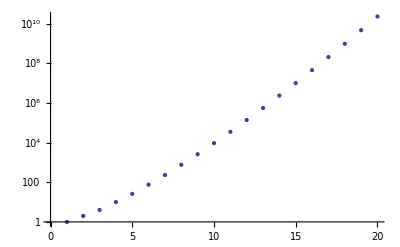

```mathematica
ListLogPlot[%]
```

Example in the Wikipedia :

```mathematica
NumberOfStandardTableaux[{5,4,1}]===288
```

True

4) Examples :

```mathematica
NumberOfStandardTableaux[{2,2}]
```

2

```mathematica
StandardTableaux[{2,2}]
```

{1 | 2
3 | 4,1 | 3
2 | 4}

```mathematica
NumberOfStandardTableaux[{2,2,2}]
```

5

```mathematica
StandardTableaux[{2,2,2},{a,b,c,d,e,f}]
```

{a | b
c | d
e | f,a | b
c | e
d | f,a | c
b | d
e | f,a | c
b | e
d | f,a | d
b | e
c | f}

```mathematica
NumberOfStandardTableaux[{2,2,2},{a,b,c,d,e,f,g}]
```

35

```mathematica
StandardTableaux[{2,2,2},{a,b,c,d,e,f,g}]
```

{a | b
c | d
e | f,a | b
c | d
e | g,a | b
c | d
f | g,a | b
c | e
d | f,a | b
c | e
d | g,a | b
c | e
f | g,a | b
c | f
d | g,a | b
c | f
e | g,a | b
d | e
f | g,a | b
d | f
e | g,a | c
b | d
e | f,a | c
b | d
e | g,a | c
b | d
f | g,a | c
b | e
d | f,a | c
b | e
d | g,a | c
b | e
f | g,a | c
b | f
d | g,a | c
b | f
e | g,a | c
d | e
f | g,a | c
d | f
e | g,a | d
b | e
c | f,a | d
b | e
c | g,a | d
b | e
f | g,a | d
b | f
c | g,a | d
b | f
e | g,a | d
c | e
f | g,a | d
c | f
e | g,a | e
b | f
c | g,a | e
b | f
d | g,a | e
c | f
d | g,b | c
d | e
f | g,b | c
d | f
e | g,b | d
c | e
f | g,b | d
c | f
e | g,b | e
c | f
d | g}

```mathematica
NumberOfStandardTableaux[4]
```

10

```mathematica
StandardTableaux[4]
```

{1 | 2 | 3 | 4,1 | 2 | 3
4 |  | ,1 | 2 | 4
3 |  | ,1 | 3 | 4
2 |  | ,1 | 2
3 | 4,1 | 3
2 | 4,1 | 2
3 | 
4 | ,1 | 3
2 | 
4 | ,1 | 4
2 | 
3 | ,1
2
3
4}

```mathematica
NumberOfStandardTableaux[4,{a,b,c,d,e}]
```

50

```mathematica
StandardTableaux[4,{a,b,c,d,e}]//Length
```

50

```mathematica
NumberOfStandardTableaux[5]
```

26

```mathematica
StandardTableaux[5]
```

{1 | 2 | 3 | 4 | 5,1 | 2 | 3 | 4
5 |  |  | ,1 | 2 | 3 | 5
4 |  |  | ,1 | 2 | 4 | 5
3 |  |  | ,1 | 3 | 4 | 5
2 |  |  | ,1 | 2 | 3
4 | 5 | ,1 | 2 | 4
3 | 5 | ,1 | 2 | 5
3 | 4 | ,1 | 3 | 4
2 | 5 | ,1 | 3 | 5
2 | 4 | ,1 | 2 | 3
4 |  | 
5 |  | ,1 | 2 | 4
3 |  | 
5 |  | ,1 | 2 | 5
3 |  | 
4 |  | ,1 | 3 | 4
2 |  | 
5 |  | ,1 | 3 | 5
2 |  | 
4 |  | ,1 | 4 | 5
2 |  | 
3 |  | ,1 | 2
3 | 4
5 | ,1 | 2
3 | 5
4 | ,1 | 3
2 | 4
5 | ,1 | 3
2 | 5
4 | ,1 | 4
2 | 5
3 | ,1 | 2
3 | 
4 | 
5 | ,1 | 3
2 | 
4 | 
5 | ,1 | 4
2 | 
3 | 
5 | ,1 | 5
2 | 
3 | 
4 | ,1
2
3
4
5}

```mathematica
%//Length
```

26

There is this interesting identity, which seems to come from the Robinson correspondence (see Fulton, page 52), and which is very important in the theory of characters of the symmetric groups:

```mathematica
(NumberOfStandardTableaux/@IntegerPartitions[10])^2
```

{1,81,1225,1296,5625,25600,7056,8100,99225,50625,122500,15876,1764,82944,202500,321489,275625,200704,15876,63504,90000,44100,589824,275625,90000,321489,122500,7056,44100,63504,202500,50625,82944,99225,25600,1296,1764,8100,5625,1225,81,1}

```mathematica
Total[%]===10!
```

True

The RSK correspondence also gives a formula for the sum of those numbers, in terms of the number of involutions in S[n]. See Fulton, page 52.

```mathematica
NumberOfInvolutions[n_]:=n!Sum[1/(n-2k)!/2^k/k!,{k,0,Floor[n/2]}]
```

```mathematica
NumberOfStandardTableaux/@IntegerPartitions[10]
```

{1,9,35,36,75,160,84,90,315,225,350,126,42,288,450,567,525,448,126,252,300,210,768,525,300,567,350,84,210,252,450,225,288,315,160,36,42,90,75,35,9,1}

```mathematica
Total[%]===NumberOfInvolutions[10]
```

True

#### 3.7. Semistandard tableaux

1) A semistandard tableau is one in which labels are strictly increasing on any given column, and are non-decreasing (could be repeated) on any given row.

```mathematica
?SemistandardTableauQ
```

SemistandardTableauQ[tab] gives True if the labels of the Young tableau tab are sorted in each row and are sorted and different in each column. It returns False otherwise.

```mathematica
SemistandardTableauQ[tab:Tableau[___List]]:=TableauQ[tab]&&And@@(OrderedQ/@tab)&&And@@(UnsameOrderedQ/@transpose[tab]);
SemistandardTableauQ[_]:=False;
SetNumberOfArguments[SemistandardTableauQ,1];
Protect[SemistandardTableauQ];
```

It is helpful below to use this private function :

```mathematica
NonSemistandardTableauQ[tab_]:=Not@SemistandardTableauQ[tab];
```

2) SemistandardTableaux is not a very elegant function because it first generates lots of tableaux (by expanding the dimension over standard tableaux) and then selects only those which are semistandard. It should be possible to enumerate directly semistandard tableaux.

```mathematica
?SemistandardTableaux
```

SemistandardTableaux[par, set] returns the list of all semistandard tableaux, of shape given by the partition par, that can be constructed onto the given set of labels. SemistandardTableaux[par, n] for a positive integer n is interpreted as SemistandardTableaux[par, Range[n]]. SemistandardTableaux[par] is interpreted as SemistandardTableaux[par, Total[par]].

```mathematica
rules[0,set_List]:={};
rules[m_Integer?Positive,labels_List]:=Flatten[Outer[Inner[Rule,Range[m],{##},List]&,Sequence@@Table[labels,{m}]],m-1];
SemistandardTableaux[par:{___Integer}]:=SemistandardTableaux[par,Total[par]];
SemistandardTableaux[par:{___Integer},dim_Integer?NonNegative]:=SemistandardTableaux[par,Range[dim]];
SemistandardTableaux[par:{___Integer},labels_List]:=Sort@Select[First[StandardTableaux[par]]/.rules[Total[par],LabelsSort[labels]],SemistandardTableauQ];
SetNumberOfArguments[SemistandardTableaux,{1,2}];
(*Protect[SemistandardTableaux];*)
```

```mathematica
StandardTableaux[{},{a,b}]
```

{Tableau[]}

```mathematica
StandardTableaux[{},{}]
```

{Tableau[]}

```mathematica
StandardTableaux[{2,2},{}]
```

{}

3) This is the number of semistandard tableaux in dimension dim (that is, with labels Range[dim]). It gives the number of components when the tensor has as symmetry a standard tableau of the given partition. Fulton calls this d_λ(m), where λ is the partition and m is our dim. Fulton says that this formula in terms of hook-lengths is due to Stanley (1971).

```mathematica
?NumberOfSemistandardTableaux
```

NumberOfSemistandardTableaux[par, set] returns the number of semistandard tableaux, of shape given by the partition par, that can be constructed onto the given set of labels. NumberOfSemistandardTableaux[par, n] for a positive integer n is interpreted as NumberOfSemistandardTableaux[par, Range[n]]. NumberOfSemistandardTableaux[par] is interpreted as NumberOfSemistandardTableaux[par, Total[par]].

```mathematica
NumberOfSemistandardTableaux[par:{___Integer}]:=NumberOfSemistandardTableaux[par,Total[par]];
NumberOfSemistandardTableaux[par:{___Integer},labels_List]:=NumberOfSemistandardTableaux[par,Length@LabelsSort[labels]];
NumberOfSemistandardTableaux[par:{___Integer},dim_Integer?NonNegative]:=If[Length[par]>dim,0,DET@(Join[par,Table[0,{dim-Length[par]}]]+dim-Range[dim])/DET@Range[dim-1,0,-1]];
SetNumberOfArguments[NumberOfSemistandardTableaux,{1,2}];
Protect[NumberOfSemistandardTableaux];
```

Examples :

```mathematica
NumberOfSemistandardTableaux[{},{}]
```

1

```mathematica
NumberOfSemistandardTableaux[{},{a,b,c}]
```

1

```mathematica
NumberOfSemistandardTableaux[{2,1},{}]
```

0

```mathematica
NumberOfSemistandardTableaux[{2,1},{a}]
```

0

```mathematica
SemistandardTableaux[{2,1},{a}]
```

{}

```mathematica
NumberOfSemistandardTableaux[{2,1},{a,b}]
```

2

```mathematica
SemistandardTableaux[{2,1},{a,b}]
```

{a | a
b | ,a | b
b | }

For the Riemann tensor in several dimensions we have

```mathematica
NumberOfSemistandardTableaux[{2,2},#]&/@Range[0,26]
```

{0,0,1,6,20,50,105,196,336,540,825,1210,1716,2366,3185,4200,5440,6936,8721,10830,13300,16170,19481,23276,27600,32500,38025}

Example in the Wikipedia:

```mathematica
NumberOfSemistandardTableaux[{5,4,1},7]===66528
```

True

For the Riemann tensor in 4 dimensions :

```mathematica
SemistandardTableaux[{2,2},4]
```

{1 | 1
2 | 2,1 | 1
2 | 3,1 | 1
2 | 4,1 | 1
3 | 3,1 | 1
3 | 4,1 | 1
4 | 4,1 | 2
2 | 3,1 | 2
2 | 4,1 | 2
3 | 3,1 | 2
3 | 4,1 | 2
4 | 4,1 | 3
2 | 4,1 | 3
3 | 4,1 | 3
4 | 4,2 | 2
3 | 3,2 | 2
3 | 4,2 | 2
4 | 4,2 | 3
3 | 4,2 | 3
4 | 4,3 | 3
4 | 4}

```mathematica
Length[%]
```

20

```mathematica
NumberOfSemistandardTableaux[{2,2},4]
```

20

There is this interesting identity, which seems to come from the Robinson correspondence (Fulton, page 52),

```mathematica
(NumberOfSemistandardTableaux[#,5]NumberOfStandardTableaux[#]&)/@IntegerPartitions[7]
```

{330,4320,11760,8100,7840,24500,3200,6615,4410,6125,225,560,140,0,0}

```mathematica
Total[%]===5^7
```

True

Another interesting result is that the number of matrices m by n with nonnegative entries that sum to r is the sum of NumberOfSemistandardTableaux[λ,m]*NumberOfSemistandardTableaux[λ,n] over all partitions λ of r. For example, take all 2x3 matrices with entries adding up to 10:

```mathematica
Flatten[Permutations/@IntegerPartitions[10,{6},Range[0,10]],1]//Length
```

3003

```mathematica
NumberOfSemistandardTableaux[#,2]&/@IntegerPartitions[10]
```

{11,9,7,0,5,0,0,3,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
NumberOfSemistandardTableaux[#,3]&/@IntegerPartitions[10]
```

{66,99,105,36,90,48,0,60,42,15,0,0,21,24,15,0,0,0,0,6,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
%.%%
```

3003

That number is also the following combinatorial number, because this is just a multichoose problem:

```mathematica
Binomial[10+2 3-1,10]
```

3003

The connection is that the number of ways of choosing k nonnegative integers to add up to n is Binomial[n + k - 1, n]. This is exercise 7 of Fulton, page 53.

```mathematica
Binomial[2 3+10-1,10]
```

3003

```mathematica
FrobeniusSolve[{1,1,1,1,1,1},10]//Length
```

3003

Exercise 8 of Fulton's book, page 53, is rather amazing as a generalization of Sudokus and Latin squares.

Exercise 15 of Fulton in page 56 shows how to count the semistandard tableaux in a numeric set of labels whose entries all sum to a given number. It uses a generating function.

#### 3.8. Normal tableaux

1) A normal tableau is a tableau in which all labels are sorted when joining all rows together into a single list. Hence, there is a single normal tableau for a given partition (and using a predetermined collection of different elements). It is always the first one in our listings of standard tableaux.

```mathematica
?NormalTableauQ
```

NormalTableauQ[tab] gives True if the Young tableau tab is written in normal form, that is, its elements are sorted when joining all rows into a single list. It returns False otherwise.

```mathematica
NormalTableauQ[tab:Tableau[___List]]:=TableauQ[tab]&&OrderedQ[Flatten[List@@tab]];
NormalTableauQ[_]:=False;
SetNumberOfArguments[NormalTableauQ,1];
Protect[NormalTableauQ];
```

Examples :

```mathematica
TableauQ[Tableau[{1,3},{2,4}]]
```

True

```mathematica
StandardTableauQ[Tableau[{1,3},{2,4}]]
```

True

```mathematica
NormalTableauQ[Tableau[{1,3},{2,4}]]
```

False

2) This command constructs a tableau from a partition of the number of indices. It can be also understood as a normal-numbered form of a Young diagram.

QUESTION : Do we need this function? I find it too simple, and actually it is never used in the rest of the package. Note also that this is identical to FirstLexicographicStandardTableau, taken from Combinatorica`.

```mathematica
?TableauOfPartition
```

TableauOfPartition[part] returns a filled Tableau constructed from part which is the partition of a natural number. The entries of this tableau are the natural numbers sorted in their canonical order when reading the tableau from left to right

```mathematica
row[{___,m_},n_]:=Range[m+1,m+n];
TableauOfPartition[par:{___Integer}]:=Apply[Tableau,Rest@FoldList[row,{0},par]];
SetNumberOfArguments[TableauOfPartition,1];
Protect[TableauOfPartition];
```

3) There is nothing to compute here concerning numbers of these objects, because there is one normal tableau per partition.

Example :

```mathematica
TableauOfPartition[{4,3,2,1}]
```

1 | 2 | 3 | 4
5 | 6 | 7 | 
8 | 9 |  | 
10 |  |  |

```mathematica
FirstLexicographicStandardTableau[{4,3,2,1}]
```

1 | 2 | 3 | 4
5 | 6 | 7 | 
8 | 9 |  | 
10 |  |  |

### 4. Skew-tableaux

#### 4.0. Comments on the skew-tableaux

In order to deal with skew-tableaux we introduce the symbol Skew. Do not use it as a label for any other purpose! This is not an ideal solution, because skew-tableaux can also be classified as standard, semistandard, etc, and we are not implementing that. That is, we are considering skew-tableaux as a special case of tableau (those using the “label” Skew), but perhaps it would be more natural to consider tableaux as a special case of skew-tableau (those with an empty inner partition).

```mathematica
?Skew
```

Skew is a symbol used to denote boxes of the interior partition of a skew tableau.

```mathematica
Format[Skew]=■;
Protect[Skew];
```

Skew-tableaux have two associated partitions. We will talk of “the partition” or the “outer partition” when referring to the larger one, and of the “skew partition” or the “inner partition” when referring to the smaller one. Our notation naturally implements the fact that the outer partition includes the inner partition and hence we do not have to check that in the tableaux. We need to check that on functions creating skew-tableaux.

```mathematica
takeSkew[{lskew:Longest[Skew...],rest___}]:=If[FreeQ[{rest},Skew],{lskew},Throw[Print["Skew labels are not contiguous in rows."]]];
SkewPartition[tab_Tableau]:=(Length/@takeSkew/@List@@tab)//.{ints___,0}:>{ints};
```

For example:

```mathematica
Tableau[{Skew,Skew,Skew,Skew,2},{Skew,Skew,Skew,Skew,6},{Skew,2,4,4},{2,3,6},{5,5}]
```

■ | ■ | ■ | ■ | 2
■ | ■ | ■ | ■ | 6
■ | 2 | 4 | 4 | 
2 | 3 | 6 |  | 
5 | 5 |  |  |

```mathematica
TableauPartition[%]
```

{5,5,4,3,2}

```mathematica
SkewPartition[%%]
```

{4,4,1}

Tableaux have an empty skew partition:

```mathematica
Tableau[{1,2},{3}]
```

1 | 2
3 |

```mathematica
SkewPartition[%]
```

{}

Finally a small function to delete the Skew boxes:

```mathematica
DeleteSkew[list_List]:=DeleteCases[list,Skew];
DeleteSkew[tab_Tableau]:=DeleteSkew/@tab;
```

#### 4.1. Ordering of skew-tableaux. TODO

#### 4.2. (General) skew-tableaux

1) Identification:

```mathematica
SkewTableauQ[tab_Tableau]:=TableauQ[tab]&&PartitionQ@SkewPartition[tab];
SkewTableauQ[_]:=False;
SetNumberOfArguments[SkewTableauQ,1];
```

```mathematica
Tableau[{Skew,Skew,Skew,Skew,2},{Skew,Skew,Skew,Skew,6},{Skew,2,4,4},{2,3,6},{5,5}]
```

■ | ■ | ■ | ■ | 2
■ | ■ | ■ | ■ | 6
■ | 2 | 4 | 4 | 
2 | 3 | 6 |  | 
5 | 5 |  |  |

```mathematica
SkewTableauQ[%]
```

True

QUESTION: Is this reasonable?

```mathematica
TableauQ[%%]
```

True

Trivially, tableaux are considered to be also skew-tableaux :

```mathematica
Tableau[{1,2},{3}]
```

1 | 2
3 |

```mathematica
SkewTableauQ[%]
```

True

This case is invalid:

```mathematica
Tableau[{Skew,Skew,a,Skew,b},{Skew,Skew,c},{d}]
```

■ | ■ | a | ■ | b
■ | ■ | c |  | 
d |  |  |  |

```mathematica
Catch[SkewPartition[%]]
```

Skew labels are not contiguous in rows.

```mathematica
Catch[SkewTableauQ[%%]]
```

Skew labels are not contiguous in rows.

2) Enumeration of skew-tableaux on a given labels set is easy: construct a template skew tableau and then map all possible tuples of the labels set:

```mathematica
SkewTableaux[opar_List,ipar_List]:=SkewTableaux[opar,ipar,Total[opar]-Total[ipar]];
SkewTableaux[opar_List,ipar_List,dim_Integer]:=SkewTableaux[opar,ipar,Range[dim]];
SkewTableaux[opar_List,ipar_List,labels_List]:=With[{vars=Unique[]&/@Range[Total[opar]-Total[ipar]]},First@Fold[{Append[#1[[1]],Join[ConstantArray[Skew,#2[[2]]],Take[#1[[2]],Subtract@@#2]]],Drop[#1[[2]],Subtract@@#2]}&,{Tableau[],vars},Transpose[{opar,PadRight[ipar,Length[opar]]}]]/.Inner[Rule[#2,#1]&,Tuples[LabelsSort[labels],Length[vars]],vars,List,2]
];
SetNumberOfArguments[SkewTableaux,{2,3}];
```

```mathematica
SkewTableaux[{3,2,1},{2,1},{a,b,c,d}]//Length
```

64

3) Counting is equally simple:

```mathematica
NumberOfSkewTableaux[opar_List,ipar_List]:=NumberOfSkewTableaux[opar,ipar,Total[opar]-Total[ipar]];
NumberOfSkewTableaux[opar_List,ipar_List,dim_Integer]:=
dim^(Total[opar]-Total[ipar]);
NumberOfSkewTableaux[opar_List,ipar_List,labels_List]:=NumberOfSkewTableaux[opar,ipar,Length[LabelsSort[labels]]];
SetNumberOfArguments[NumberOfSkewTableaux,{2,3}];
```

```mathematica
NumberOfSkewTableaux[{3,2,1},{2,1},{a,b,c,d}]
```

64

#### 4.3. Disjoint skew-tableaux

1) Identification:

```mathematica
DisjointSkewTableauQ[tab_Tableau]:=TableauQ[tab]&&disjointQ[DeleteSkew[tab]];
DisjointSkewTableauQ[_]:=False;
SetNumberOfArguments[DisjointSkewTableauQ,1];
```

```mathematica
Tableau[{Skew,Skew,Skew,Skew,2},{Skew,Skew,Skew,Skew,6},{Skew,2,4,4},{2,3,6},{5,5}]
```

■ | ■ | ■ | ■ | 2
■ | ■ | ■ | ■ | 6
■ | 2 | 4 | 4 | 
2 | 3 | 6 |  | 
5 | 5 |  |  |

```mathematica
DisjointSkewTableauQ[%]
```

False

```mathematica
Tableau[{Skew,Skew,Skew,Skew,2},{Skew,Skew,Skew,Skew,6},{Skew,3,4,7},{8,9,10},{11,12}]
```

■ | ■ | ■ | ■ | 2
■ | ■ | ■ | ■ | 6
■ | 3 | 4 | 7 | 
8 | 9 | 10 |  | 
11 | 12 |  |  |

```mathematica
DisjointSkewTableauQ[%]
```

True

2) Enumeration of disjoint skew-tableaux on a given labels set is easy: construct a template skew tableau and then map all possible permutations of the labels set:

```mathematica
DisjointSkewTableaux[opar_List,ipar_List]:=DisjointSkewTableaux[opar,ipar,Total[opar]-Total[ipar]];
DisjointSkewTableaux[opar_List,ipar_List,dim_Integer]:=DisjointSkewTableaux[opar,ipar,Range[dim]];
DisjointSkewTableaux[opar_List,ipar_List,labels_List]:=With[{vars=Unique[]&/@Range[Total[opar]-Total[ipar]]},First@Fold[{Append[#1[[1]],Join[ConstantArray[Skew,#2[[2]]],Take[#1[[2]],Subtract@@#2]]],Drop[#1[[2]],Subtract@@#2]}&,{Tableau[],vars},Transpose[{opar,PadRight[ipar,Length[opar]]}]]/.Inner[Rule[#2,#1]&,Permutations[LabelsSort[labels],{Length[vars]}],vars,List,2]
];
SetNumberOfArguments[DisjointSkewTableaux,{2,3}];
```

```mathematica
DisjointSkewTableaux[{3,2,1},{2,1},{a,b,c,d}]//Length
```

24

3) Counting is equally simple:

```mathematica
NumberOfDisjointSkewTableaux[opar_List,ipar_List]:=NumberOfDisjointSkewTableaux[opar,ipar,Total[opar]-Total[ipar]];
NumberOfDisjointSkewTableaux[opar_List,ipar_List,dim_Integer?Positive]:=
With[{n=Total[opar]-Total[ipar]},If[dim<n,0,dim!/(dim-n)!]];
NumberOfDisjointSkewTableaux[opar_List,ipar_List,labels_List]:=NumberOfDisjointSkewTableaux[opar,ipar,Length[LabelsSort[labels]]];
SetNumberOfArguments[NumberOfDisjointSkewTableaux,{2,3}];
```

```mathematica
NumberOfDisjointSkewTableaux[{3,2,1},{2,1},{a,b,c,d}]
```

24

#### 4.4. Standard skew-tableaux

1) Identification:

```mathematica
StandardSkewTableauQ[tab_Tableau]:=SkewTableauQ[tab]&&And@@(UnsameOrderedQ/@DeleteSkew[tab])&&And@@(UnsameOrderedQ/@DeleteSkew[transpose[tab]]);
SetNumberOfArguments[StandardSkewTableauQ,1];
```

```mathematica
Tableau[{Skew,Skew,Skew,Skew,2},{Skew,Skew,Skew,Skew,6},{Skew,2,4,4},{2,3,6},{5,5}]
```

■ | ■ | ■ | ■ | 2
■ | ■ | ■ | ■ | 6
■ | 2 | 4 | 4 | 
2 | 3 | 6 |  | 
5 | 5 |  |  |

```mathematica
StandardSkewTableauQ[%]
```

False

```mathematica
Tableau[{Skew,Skew,Skew,Skew,2},{Skew,Skew,Skew,Skew,6},{Skew,2,4,5},{2,3,6},{5,6}]
```

■ | ■ | ■ | ■ | 2
■ | ■ | ■ | ■ | 6
■ | 2 | 4 | 5 | 
2 | 3 | 6 |  | 
5 | 6 |  |  |

```mathematica
StandardSkewTableauQ[%]
```

True

2) This is a possible overshooting algorithm  to construct standard skew-tableaux from the algorithms for the respective tableaux. It can be very slow for those cases with many black boxes, but I don’t see a better way to do this...

```mathematica
PatternSkewTableau[opar_List,ipar_List,opat_,ipat_]:=Apply[Tableau,Join[ConstantArray[ipat,First[#]],ConstantArray[opat,Last[#]-First[#]]]&/@Transpose[{PadRight[ipar,Length[opar]],opar}]];
```

```mathematica
PatternSkewTableau[{3,3,2},{2,1},A,B]
```

B | B | A
B | A | A
A | A |

```mathematica
StandardSkewTableaux[opar_List,ipar_List]:=With[{labels=Range[Total[opar]]-Total[ipar],pat=PatternSkewTableau[opar,ipar,_?Positive,_?NonPositive]},Cases[StandardTableaux[opar,labels],pat]/._Integer?NonPositive->Skew//DeleteDuplicates
];
StandardSkewTableaux[opar_List,ipar_List,dim_Integer?Positive]:=StandardSkewTableaux[opar,ipar,Range[dim]];
StandardSkewTableaux[opar_List,ipar_List,labels_List]:=With[{n=Total[opar]-Total[ipar],dim=Length[LabelsSort@labels]},
Flatten@If[dim<n,{},
StandardSkewTableaux[opar,ipar]/.Inner[Rule[#2,#1]&,Subsets[LabelsSort@labels,{n}],Range[n],List]]];
SetNumberOfArguments[StandardSkewTableaux,{2,3}];
```

```mathematica
StandardSkewTableaux[{3,3,2},{2,1}]
```

{■ | ■ | 1
■ | 2 | 3
4 | 5 | ,■ | ■ | 1
■ | 2 | 4
3 | 5 | ,■ | ■ | 1
■ | 2 | 5
3 | 4 | ,■ | ■ | 1
■ | 3 | 4
2 | 5 | ,■ | ■ | 1
■ | 3 | 5
2 | 4 | ,■ | ■ | 2
■ | 1 | 3
4 | 5 | ,■ | ■ | 2
■ | 1 | 4
3 | 5 | ,■ | ■ | 2
■ | 1 | 5
3 | 4 | ,■ | ■ | 2
■ | 3 | 4
1 | 5 | ,■ | ■ | 2
■ | 3 | 5
1 | 4 | ,■ | ■ | 3
■ | 1 | 4
2 | 5 | ,■ | ■ | 3
■ | 1 | 5
2 | 4 | ,■ | ■ | 3
■ | 2 | 4
1 | 5 | ,■ | ■ | 3
■ | 2 | 5
1 | 4 | ,■ | ■ | 4
■ | 1 | 5
2 | 3 | ,■ | ■ | 4
■ | 2 | 5
1 | 3 | }

```mathematica
StandardSkewTableaux[{3,3,2},{2,1},{a,b,c,d,e,f}]
```

{■ | ■ | a
■ | b | c
d | e | ,■ | ■ | a
■ | b | d
c | e | ,■ | ■ | a
■ | b | e
c | d | ,■ | ■ | a
■ | c | d
b | e | ,■ | ■ | a
■ | c | e
b | d | ,■ | ■ | b
■ | a | c
d | e | ,■ | ■ | b
■ | a | d
c | e | ,■ | ■ | b
■ | a | e
c | d | ,■ | ■ | b
■ | c | d
a | e | ,■ | ■ | b
■ | c | e
a | d | ,■ | ■ | c
■ | a | d
b | e | ,■ | ■ | c
■ | a | e
b | d | ,■ | ■ | c
■ | b | d
a | e | ,■ | ■ | c
■ | b | e
a | d | ,■ | ■ | d
■ | a | e
b | c | ,■ | ■ | d
■ | b | e
a | c | ,■ | ■ | a
■ | b | c
d | f | ,■ | ■ | a
■ | b | d
c | f | ,■ | ■ | a
■ | b | f
c | d | ,■ | ■ | a
■ | c | d
b | f | ,■ | ■ | a
■ | c | f
b | d | ,■ | ■ | b
■ | a | c
d | f | ,■ | ■ | b
■ | a | d
c | f | ,■ | ■ | b
■ | a | f
c | d | ,■ | ■ | b
■ | c | d
a | f | ,■ | ■ | b
■ | c | f
a | d | ,■ | ■ | c
■ | a | d
b | f | ,■ | ■ | c
■ | a | f
b | d | ,■ | ■ | c
■ | b | d
a | f | ,■ | ■ | c
■ | b | f
a | d | ,■ | ■ | d
■ | a | f
b | c | ,■ | ■ | d
■ | b | f
a | c | ,■ | ■ | a
■ | b | c
e | f | ,■ | ■ | a
■ | b | e
c | f | ,■ | ■ | a
■ | b | f
c | e | ,■ | ■ | a
■ | c | e
b | f | ,■ | ■ | a
■ | c | f
b | e | ,■ | ■ | b
■ | a | c
e | f | ,■ | ■ | b
■ | a | e
c | f | ,■ | ■ | b
■ | a | f
c | e | ,■ | ■ | b
■ | c | e
a | f | ,■ | ■ | b
■ | c | f
a | e | ,■ | ■ | c
■ | a | e
b | f | ,■ | ■ | c
■ | a | f
b | e | ,■ | ■ | c
■ | b | e
a | f | ,■ | ■ | c
■ | b | f
a | e | ,■ | ■ | e
■ | a | f
b | c | ,■ | ■ | e
■ | b | f
a | c | ,■ | ■ | a
■ | b | d
e | f | ,■ | ■ | a
■ | b | e
d | f | ,■ | ■ | a
■ | b | f
d | e | ,■ | ■ | a
■ | d | e
b | f | ,■ | ■ | a
■ | d | f
b | e | ,■ | ■ | b
■ | a | d
e | f | ,■ | ■ | b
■ | a | e
d | f | ,■ | ■ | b
■ | a | f
d | e | ,■ | ■ | b
■ | d | e
a | f | ,■ | ■ | b
■ | d | f
a | e | ,■ | ■ | d
■ | a | e
b | f | ,■ | ■ | d
■ | a | f
b | e | ,■ | ■ | d
■ | b | e
a | f | ,■ | ■ | d
■ | b | f
a | e | ,■ | ■ | e
■ | a | f
b | d | ,■ | ■ | e
■ | b | f
a | d | ,■ | ■ | a
■ | c | d
e | f | ,■ | ■ | a
■ | c | e
d | f | ,■ | ■ | a
■ | c | f
d | e | ,■ | ■ | a
■ | d | e
c | f | ,■ | ■ | a
■ | d | f
c | e | ,■ | ■ | c
■ | a | d
e | f | ,■ | ■ | c
■ | a | e
d | f | ,■ | ■ | c
■ | a | f
d | e | ,■ | ■ | c
■ | d | e
a | f | ,■ | ■ | c
■ | d | f
a | e | ,■ | ■ | d
■ | a | e
c | f | ,■ | ■ | d
■ | a | f
c | e | ,■ | ■ | d
■ | c | e
a | f | ,■ | ■ | d
■ | c | f
a | e | ,■ | ■ | e
■ | a | f
c | d | ,■ | ■ | e
■ | c | f
a | d | ,■ | ■ | b
■ | c | d
e | f | ,■ | ■ | b
■ | c | e
d | f | ,■ | ■ | b
■ | c | f
d | e | ,■ | ■ | b
■ | d | e
c | f | ,■ | ■ | b
■ | d | f
c | e | ,■ | ■ | c
■ | b | d
e | f | ,■ | ■ | c
■ | b | e
d | f | ,■ | ■ | c
■ | b | f
d | e | ,■ | ■ | c
■ | d | e
b | f | ,■ | ■ | c
■ | d | f
b | e | ,■ | ■ | d
■ | b | e
c | f | ,■ | ■ | d
■ | b | f
c | e | ,■ | ■ | d
■ | c | e
b | f | ,■ | ■ | d
■ | c | f
b | e | ,■ | ■ | e
■ | b | f
c | d | ,■ | ■ | e
■ | c | f
b | d | }

```mathematica
%//Length
```

96

3) There is no obvious hook-length formula. Let us not define a counting function here...

#### 4.5. Semistandard skew-tableaux

1) Identification:

```mathematica
SemistandardSkewTableauQ[tab_Tableau]:=SkewTableauQ[tab]&&And@@(OrderedQ/@DeleteSkew[tab])&&And@@(UnsameOrderedQ/@DeleteSkew[transpose[tab]]);
SetNumberOfArguments[StandardSkewTableauQ,1];
```

```mathematica
Tableau[{Skew,Skew,Skew,Skew,2},{Skew,Skew,Skew,Skew,6},{Skew,2,4,4},{2,3,6},{5,5}]
```

■ | ■ | ■ | ■ | 2
■ | ■ | ■ | ■ | 6
■ | 2 | 4 | 4 | 
2 | 3 | 6 |  | 
5 | 5 |  |  |

```mathematica
SemistandardSkewTableauQ[%]
```

True

```mathematica
SemistandardSkewTableauQ[TransposeTableau[%%]]
```

False

2) Enumeration

```mathematica
SemistandardSkewTableaux[opar_List,ipar_List]:=SemistandardSkewTableaux[opar,ipar,Total[opar]-Total[ipar]];
SemistandardSkewTableaux[opar_List,ipar_List,dim_Integer?NonNegative]:=SemistandardSkewTableaux[opar,ipar,Range[dim]];
SemistandardSkewTableaux[opar_List,ipar_List,labels_List]:=Sort@Select[First[StandardSkewTableaux[opar,ipar]]/.rules[Total[opar]-Total[ipar],LabelsSort[labels]],SemistandardSkewTableauQ];
SetNumberOfArguments[SemistandardSkewTableaux,{1,2}];
(*Protect[SemistandardSkewTableaux];*)
```

```mathematica
SemistandardSkewTableaux[{3,3,2},{2,1},{a,b,c}]
```

{■ | ■ | a
■ | a | b
a | b | ,■ | ■ | a
■ | a | b
a | c | ,■ | ■ | a
■ | a | b
b | b | ,■ | ■ | a
■ | a | b
b | c | ,■ | ■ | a
■ | a | b
c | c | ,■ | ■ | a
■ | a | c
a | b | ,■ | ■ | a
■ | a | c
a | c | ,■ | ■ | a
■ | a | c
b | b | ,■ | ■ | a
■ | a | c
b | c | ,■ | ■ | a
■ | a | c
c | c | ,■ | ■ | a
■ | b | b
a | c | ,■ | ■ | a
■ | b | b
b | c | ,■ | ■ | a
■ | b | b
c | c | ,■ | ■ | a
■ | b | c
a | c | ,■ | ■ | a
■ | b | c
b | c | ,■ | ■ | a
■ | b | c
c | c | ,■ | ■ | b
■ | a | c
a | b | ,■ | ■ | b
■ | a | c
a | c | ,■ | ■ | b
■ | a | c
b | b | ,■ | ■ | b
■ | a | c
b | c | ,■ | ■ | b
■ | a | c
c | c | ,■ | ■ | b
■ | b | c
a | c | ,■ | ■ | b
■ | b | c
b | c | ,■ | ■ | b
■ | b | c
c | c | }

3) There is no obvious hook-length formula. Let us not define a counting function here...

### 5. Tableau computations

#### 5.0. Comments

This section follows [Fulton], chapters 1-5.

The discussion goes as follows:
	1) There is a non-commutative associative product of semistandard tableaux, giving another semistandard tableau with the joining (in a nontrivial way) of the boxes. It is called the Schensted product, and makes the set of semistandard tableaux into an algebra over ℤ. The idea can be implemented in alternative ways, using rectification of skew-tableaux, the RSK correspondence with the plactic monoid of words, or the Schur polynomials, among others.
	2) The condition of being semistandard is so restrictive that usually we do not need to know where the labels are, but only how many of each there are: this is the weight μ={μ_1, μ_2,...} of a semistandard tableau: there are μ_1 1’s, μ_2 2’s, etc.
	3) Kostka numbers K_λμ: number of semistandard tableaux with shape λ and content μ (treat as another partition, because K_λμ is invariant under reorderings of μ). Sorting partitions lexicographically K is lower triangular and with 1’s in the diagonal.
	4) The main question is: given all semistandard tableaux of two given shapes, which other shapes can we obtain in their Schensted products, and with which multiplicities? Note that this is a property of the two initial shapes (partitions) only. The LR number (c_λ^ν)_μ is the number of ways of writing a given semistandard tableau of shape ν as the Schensted product of semistandard tableaux of respective shapes λ and μ. It is also the number of semistandard skew-tableaux ν/λ with weight μ.
	5) Given partitions λ and μ, the LR rule gives the (c_λ^ν)_μ for all ν, using a backtracking algorithm. It is also possible to write another backtracking algorithm that computes them for all μ, given λ and ν.

#### 5.1. Bumping and the Schensted product

1) This operation (called “row insertion” or “row bumping”) is well defined only on semistandard tableaux, and the result is always still semistandard.

Take a semistandard tableau T and a label x. Construct a new semistandard tableau, denoted T←x, with one more box than T, with some moving around:
	1) If x is at least as large as all the entries in the first row of T, simply add x in a new box to the end of the first row.
	2) If not, find the left-most entry in the first row that is strictly larger than x. Put x in the box of this entry and remov (“bump”) the entry.
	3) Take this entry that was bumped from the first row and repeat the process on the second row.
	4) Keep going until the bumped entry can be put at the end of the row it is bumped into, or until it is bumped out the bottom, in which case it forms a new row with one entry.

```mathematica
?RowBump
```

RowBump[tab, x, n] bumps the label x into the n-th row of the semistandard tableau tab. RowBump[tab, x] bumps the label into the first row of tab.

```mathematica
ColumnOfStrictlyLarger[rowlabels_,label_]:=Module[{col=Length[rowlabels]},While[!OrderedQ[{rowlabels[[col]],label}]&&col>0,col--];col+1];
RowBump[tab_Tableau?SemistandardTableauQ,label_,row_:1]:=With[{col=If[row≤Length[tab],ColumnOfStrictlyLarger[tab[[row]],label],0]},Which[
col===0,
Append[tab,{label}],
col>Length[tab[[row]]],MapAt[Append[#,label]&,tab,row],
True,
RowBump[ReplacePart[tab,{row,col}->label],tab[[row,col]],row+1]
]
];
```

Example from Fulton: The added 2 bumps 3 from the first row, which bumps a 5 from the second row, which bumps 6 from the third row, which gets placed in the final row.

```mathematica
Tableau[{1,2,2,3},{2,3,5,5},{4,4,6},{5,6}]
```

1 | 2 | 2 | 3
2 | 3 | 5 | 5
4 | 4 | 6 | 
5 | 6 |  |

```mathematica
RowBump[%,2]
```

1 | 2 | 2 | 2
2 | 3 | 3 | 5
4 | 4 | 5 | 
5 | 6 | 6 |

```mathematica
SemistandardTableauQ[%]
```

True

2) The row-bumping operation can be reversed if we know the position of the last added box. It returns the previous tableau and the label that was last bumped in.

```mathematica
ColumnOfStrictlySmaller[rowlabels_,label_]:=Module[{col=Length[rowlabels]},While[OrderedQ[{label,rowlabels[[col]]}]&&col>0,col--];col];
ReverseRowBump[tab_Tableau?SemistandardTableauQ,row_:-1]:=ReverseRowBumpLabel[MapAt[Most,tab,row],If[row<0,row+Length[tab],row-1],tab[[row,-1]]]/;Abs[row]≤Length[tab];
ReverseRowBumpLabel[tab_Tableau,0,label_]:={tab,label};
ReverseRowBumpLabel[tab_Tableau,row_,label_]:=With[{col=ColumnOfStrictlySmaller[tab[[row]],label]},
ReverseRowBumpLabel[ReplacePart[tab,{row,col}->label],row-1,tab[[row,col]]]
];
```

Example:

```mathematica
With[{tab=Tableau[{1,2,2,3},{2,3,5,5},{4,4,6},{5,6}],label=2},
ReverseRowBump@RowBump[tab,label]==={tab,label}
]
```

True

There is a concept of “bumping route”, as the set of boxes whose labels are bumped. There is then the Row Bumping Lemma, describing the relative positions of the bumping routes of two labels x1, x2 depending on whether x1<=x2 or x1>x2.

3) Iterating the bumping algorithm we can construct an associative product of semistandard tableaux, called the Schensted product:

```mathematica
?SchenstedProduct
```

SchenstedProduct[tab1, tab2] computes the Schensted product of the semistandard tableaux tab1 and tab2, by iteration of RowBump.

```mathematica
SchenstedProduct[tab1_Tableau?SemistandardTableauQ,tab2_Tableau?SemistandardTableauQ]:=Fold[RowBump,tab1,Flatten[Reverse[List@@tab2]]];
```

```mathematica
{Tableau[{1,2,2,3},{2,3,5,5},{4,4,6},{5,6}],Tableau[{1,3},{2}]}
```

{1 | 2 | 2 | 3
2 | 3 | 5 | 5
4 | 4 | 6 | 
5 | 6 |  | ,1 | 3
2 | }

```mathematica
SchenstedProduct@@%
```

1 | 1 | 2 | 2 | 3
2 | 2 | 3 | 5 | 
3 | 4 | 5 |  | 
4 | 6 | 6 |  | 
5 |  |  |  |

The empty tableau is the identity for such product :

```mathematica
SchenstedProduct[Tableau[{1,2},{3}],Tableau[]]
```

1 | 2
3 |

```mathematica
SchenstedProduct[Tableau[],Tableau[{1,2},{3}]]
```

1 | 2
3 |

Hence we have an associative monoid (associative semigroup with identity).

These are the two elementary Knuth transformations for x<y<z (equalities are allowed as obvious in the result):

```mathematica
SchenstedProduct[Tableau[{y,z}],Tableau[{x}]]
```

x | z
y |

```mathematica
SchenstedProduct[Tableau[{x,z}],Tableau[{y}]]
```

x | y
z |

4) For the RKS correspondence, it is interesting to keep track of the positions where the different labels have been inserted. This is done with an "insertion tableau", also called a “recording tableau”. This function takes two semistandard tableaux (the first with arbitrary labels, and the second with slot labels), assumed to have the same shape and RowBump the label in the first and modify the second to keep track of the routes:

```mathematica
RowBumpInsert[{tab_Tableau?SemistandardTableauQ,instab_Tableau?SemistandardTableauQ},{label_,step_Integer},row_:1]:=With[{col=If[row≤Length[tab],ColumnOfStrictlyLarger[tab[[row]],label],0],trinstab=TransposeTableau[instab]},Which[
col===0,
{Append[tab,{label}],
If[trinstab===Tableau[],Tableau[{step}],TransposeTableau@MapAt[Append[#,step]&,trinstab,1]]},
col>Length[tab[[row]]],
{MapAt[Append[#,label]&,tab,row],If[col>Length[trinstab],TransposeTableau@Append[trinstab,{step}],
TransposeTableau@MapAt[Append[#,step]&,trinstab,col]]},
True,
RowBumpInsert[{ReplacePart[tab,{row,col}->label],instab},{tab[[row,col]],step},row+1]
]
]/;(Length/@tab)===(Length/@instab)&&(Union@@instab==Range[Max[0,Sequence@@instab]]);
```

#### 5.2. Sliding and the “jeu de taquin”

Recall that an “inner corner” is a Skew box whose right and lower neighbours are not Skew. An “outer corner” is a normal box with neither a right nor a lower neightbours.

1) The sliding algorithm takes a skew semistandard tableau and removes one Skew box:

```mathematica
?SkewTableauSlide
```

SkewTableauSlide[skewtab] removes the last Skew box of the skew tableau skewtab, using the sliding algorithm.

```mathematica
SkewTableuSlide[tab_Tableau]:=
TableauSlide1[tab,If[#==={},{},Last[#]]&@PartitionCorners[SkewPartition[tab]]];
TableauSlide1[tab_,{}]:=tab;
TableauSlide1[tab_,corner_]:=TableauSlide2[tab,corner]/;Extract[tab,corner]===Skew;
TableauSlide2[tab_,{row_,column_}]:=TableauSlide3[tab,{row,column},If[Length[TransposeTableau[tab][[column]]]>row,tab[[row+1,column]],Null],If[Length[tab[[row]]]>column,tab[[row,column+1]],Null]];
TableauSlide3[tab_,{row_,column_},Null,Null]:=MapAt[Drop[#,-1]&,tab,row];
TableauSlide3[tab_,{row_,column_},below_,Null]:=TableauSlide2[ReplacePart[tab,{{row,column}->below,{row+1,column}->Skew}],{row+1,column}];
TableauSlide3[tab_,{row_,column_},Null,right_]:=TableauSlide2[ReplacePart[tab,{{row,column}->right,{row,column+1}->Skew}],{row,column+1}];
TableauSlide3[tab_,{row_,column_},below_,right_]:=If[OrderedQ[{below,right}],
TableauSlide2[ReplacePart[tab,{{row,column}->below,{row+1,column}->Skew}],{row+1,column}],TableauSlide2[ReplacePart[tab,{{row,column}->right,{row,column+1}->Skew}],{row,column+1}]
];
```

Example from Fulton:

```mathematica
Tableau[{Skew,Skew,Skew,Skew,2},{Skew,Skew,Skew,Skew,6},{Skew,2,4,4},{2,3,6},{5,5}]
```

■ | ■ | ■ | ■ | 2
■ | ■ | ■ | ■ | 6
■ | 2 | 4 | 4 | 
2 | 3 | 6 |  | 
5 | 5 |  |  |

This removes the last inside corner of the small tableau :

```mathematica
SkewTableuSlide[%]
```

■ | ■ | ■ | ■ | 2
■ | ■ | ■ | ■ | 6
2 | 2 | 4 | 4 | 
3 | 5 | 6 |  | 
5 |  |  |  |

2) Iteration of the slide algorithm over all Skew boxes gives the concept of rectification of a skew-tableau :

```mathematica
?RectifySkewTableau
```

RectifySkewTableau[skewtab] removes all Skew boxes of the skew tableau skewtab, by iteration of SkewTableauSlide.

```mathematica
RectifySkewTableau[tab_Tableau?SkewTableauQ]:=FixedPoint[SkewTableuSlide,tab];
```

```mathematica
Tableau[{Skew,Skew,Skew,Skew,2},{Skew,Skew,Skew,Skew,6},{Skew,2,4,4},{2,3,6},{5,5}]
```

■ | ■ | ■ | ■ | 2
■ | ■ | ■ | ■ | 6
■ | 2 | 4 | 4 | 
2 | 3 | 6 |  | 
5 | 5 |  |  |

```mathematica
RectifySkewTableau[%]
```

2 | 2 | 2 | 4 | 6
3 | 4 | 6 |  | 
5 | 5 |  |  |

```mathematica
SemistandardTableauQ[%]
```

True

```mathematica
RectifySkewTableau[Tableau[{Skew,Skew},{Skew,Skew}]]
```

Tableau[]

3) The interesting observation is that these two coincide:

```mathematica
Tableau[{Skew,Skew,Skew,Skew,1,3},{Skew,Skew,Skew,Skew,2},{1,2,2,3},{2,3,5,5},{4,4,6},{5,6}]
```

■ | ■ | ■ | ■ | 1 | 3
■ | ■ | ■ | ■ | 2 | 
1 | 2 | 2 | 3 |  | 
2 | 3 | 5 | 5 |  | 
4 | 4 | 6 |  |  | 
5 | 6 |  |  |  |

```mathematica
RectifySkewTableau[%]//Timing
```

{0.00438,1 | 1 | 2 | 2 | 3
2 | 2 | 3 | 5 | 
3 | 4 | 5 |  | 
4 | 6 | 6 |  | 
5 |  |  |  | }

```mathematica
SchenstedProduct[Tableau[{1,2,2,3},{2,3,5,5},{4,4,6},{5,6}],Tableau[{1,3},{2}]]//Timing
```

{0.00239,1 | 1 | 2 | 2 | 3
2 | 2 | 3 | 5 | 
3 | 4 | 5 |  | 
4 | 6 | 6 |  | 
5 |  |  |  | }

Again, these are the elementary Knuth transformations, with x<y<z :

```mathematica
RectifySkewTableau[Tableau[{Skew,Skew,x},{y,z}]]
```

x | z
y |

```mathematica
RectifySkewTableau[Tableau[{Skew,Skew,y},{x,z}]]
```

x | y
z |

#### 5.3. Words and the plactic monoid

A word is just a list of labels, and they can be repeated. We will later see a generalization to “double words” (my name) in which we have a list with two lists { slots, labels }. A word of length n is equivalent to the double word { Range[n], word }, but in the double word the slots (which must be integers 1...m) can also be repeated.

Given any semistandard tableau or skew-tableau, we associate to it a word in the following way:

```mathematica
WordOfTableau[tab_Tableau]:=DeleteCases[Join@@Reverse[tab],Skew]
```

The process is obviously reversible for words constructed from a non-skew semistandard tableau, but not every word comes from such a tableau in this way, and the Skew information is lost in the conversion to a word, so many different skew-tableaux may give the same word. In fact every word comes from some (generally many) skew-tableau.

We proceed in a different way: Given a word, there is a unique semistandard tableau whose word is Knuth-equivalent (see below) to the original word:

```mathematica
TableauOfWord[word_List]:=Fold[RowBump,Tableau[],word]
```

```mathematica
TableauOfWord[{a,b,c,a,d,c}]
```

a | a | c | c
b | d |  |

```mathematica
WordOfTableau[%]
```

{b,d,a,a,c,c}

```mathematica
TableauOfWord[%]
```

a | a | c | c
b | d |  |

Hence, semistandard tableaux correspond to classes of equivalence of words.

We could also define Knuth-equivalence of words as those words whose tableaux coincide.

But usually Knuth-equivalence is based on whether words can be related by elementary Knuth transformations. There are two. The basic idea is to work with a product of words given by juxtaposition, and give words a canonical form under the Knuth transformations:

Elementary Knuth transformation 1:

```mathematica
KnuthProduct[{L___,y_,z_,x_,R___}]:=(Print["Using rule 1 with ",{L,y,z,x,R}->{L,y,x,z,R}," assuming ",x,"<",y,"≤"z];KnuthProduct[{L,y,x,z,R}])/;OrderedQ[{x,y,z}]&&UnsameQ[x,y];
```

Elementary Knuth transformation 2:

```mathematica
KnuthProduct[{L___,x_,z_,y_,R___}]:=(Print["Using rule 2 with ",{L,x,z,y,R}->{L,z,x,y,R}," assuming ",x,"≤",y,"<",z];KnuthProduct[{L,z,x,y,R}])/;OrderedQ[{x,y,z}]&&UnsameQ[y,z];
```

Fulton's description is terrible, and leads to infinite loops :

```mathematica
TableauOfWord[{v,x,z,u,y}]
```

u | x | y
v | z |

```mathematica
WordOfTableau[%]
```

{v,z,u,x,y}

This construction does not stop when that canonical word is found. I don' t know what is the criterium to stop it. Perhaps there is no notion of canonical representative, and all what these two rules do is showing equivalence between two words. Fulton’s example just want to use equivalence between the original word {v,x,z,u,y} and the word {v,z,u,x,y}, which we get already in the fifth step.

```mathematica
Block[{$RecursionLimit=20,$IterationLimit=20},KnuthProduct[{v,x,z,u,y}]]
```

Using rule 1 with {v,x,z,u,y}→{v,x,u,z,y} assuming u<x≤ z

Using rule 1 with {v,x,u,z,y}→{v,u,x,z,y} assuming u<v≤ x

Using rule 2 with {v,u,x,z,y}→{v,u,z,x,y} assuming x≤y<z

Using rule 2 with {v,u,z,x,y}→{v,z,u,x,y} assuming u≤x<z

Using rule 1 with {v,z,u,x,y}→{v,u,z,x,y} assuming u<v≤ z

Using rule 2 with {v,u,z,x,y}→{v,z,u,x,y} assuming u≤x<z

Using rule 1 with {v,z,u,x,y}→{v,u,z,x,y} assuming u<v≤ z

Using rule 2 with {v,u,z,x,y}→{v,z,u,x,y} assuming u≤x<z

Using rule 1 with {v,z,u,x,y}→{v,u,z,x,y} assuming u<v≤ z

Using rule 2 with {v,u,z,x,y}→{v,z,u,x,y} assuming u≤x<z

Using rule 1 with {v,z,u,x,y}→{v,u,z,x,y} assuming u<v≤ z

Using rule 2 with {v,u,z,x,y}→{v,z,u,x,y} assuming u≤x<z

Using rule 1 with {v,z,u,x,y}→{v,u,z,x,y} assuming u<v≤ z

Using rule 2 with {v,u,z,x,y}→{v,z,u,x,y} assuming u≤x<z

Using rule 1 with {v,z,u,x,y}→{v,u,z,x,y} assuming u<v≤ z

Using rule 2 with {v,u,z,x,y}→{v,z,u,x,y} assuming u≤x<z

$RecursionLimit::reclim: Recursion depth of 20 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 20 exceeded.

General::stop: Further output of $IterationLimit :: itlim will be suppressed during this calculation.

KnuthProduct[{v,z,u,x,y}]

In principle, this provides a third route to the tableau product monoid.

With any monoid there is an associated "group ring". For the monoid of semistandard tableaux with labels in S, we have the ring R_S, called the tableau ring. This is the module of linear combinations with integers of the semistandard tableaux in S, with multiplication determined by the multiplication of tableaux. It is an associative but noncommutative ring. There is a canonical homomorphism of this ring to the ring of polynomials with integers coefficients with variables S.

An interesting result (Fulton, exercise 16, page 57) is that for a semistandard tableau T with shape λ there are exactly NumberOfStandardTableaux[λ] words that are Knuth-equivalent to WordOfTableau[T]. I have tried to check examples, but I don’t get that result...

An important type of words, for later use, are lattice words and reverse lattice words (aka Yamanouchi words):

```mathematica
LatticeWordQ[word_List]:=LatticeWordQ[word,Union[word]];
LatticeWordQ[word_List,labels_]:=Module[{n,rules},
n=Length[labels];
rules=Thread[labels->Range[n]];
And@@GreaterEqual@@@FoldList[Plus[#1,UnitVector[n,#2]]&,ConstantArray[0,n],word/.rules]
];
ReverseLatticeWordQ[word_List]:=ReverseLatticeWordQ[word,Union[word]];
ReverseLatticeWordQ[word_List,labels_]:=LatticeWordQ[Reverse[word],labels];
```

```mathematica
ReverseLatticeWordQ[{2,1,3,2,1,2,1}]
```

True

```mathematica
ReverseLatticeWordQ[{1,2,3,2,1,2,1}]
```

False

Interestingly, being ReverseLatticeWordQ is a property that is preserved under Knuth equivalence.

There is a canonical correspondence between standard tableaux and reverse lattice words. We do this for the integers alphabet only:

```mathematica
TableauOfReverseLatticeWord[word_?ReverseLatticeWordQ]:=Tableau@@Fold[With[{matrix=#1,pos=#2[[1]],val=#2[[2]]},MapAt[Prepend[#,val]&,matrix,pos]]&,ConstantArray[{},Max[word]],Reverse@Transpose[{Reverse[word],Range[Length[word]]}]];
```

```mathematica
ReverseLatticeWordOfTableau[tab_?StandardTableauQ]:=Reverse[Position[tab,#][[1,1]]&/@Union@@tab]
```

```mathematica
TableauOfReverseLatticeWord[{1,1,2,3,1,2,1}]
```

1 | 3 | 6 | 7
2 | 5 |  | 
4 |  |  |

```mathematica
ReverseLatticeWordOfTableau[%]
```

{1,1,2,3,1,2,1}

#### 5.4. Increasing sequences. TODO

This is chapter 3 of Fulton’s book. I skipped it this time...

#### 5.5. Weight of a tableau. Kostka numbers

1) The weight of a tableau in a set S of labels is a list of integers counting how many times each label appears in the tableau, respectively. Hence weights are lists of integers, not necessarily partitions, though clearly the sum of the integers is the number of boxes. These lists are sometimes called “weak decompositions” of an integer.

```mathematica
?TableauWeight
```

TableauWeight[tab, set] returns the weight of the tableau w.r.t. the given set of labels. This is a list of the respective numbers of occurrences of the elements of set in the tableau tab. TableauWeight[tab] returns the weight in the set of the union of all entries, sorted.

```mathematica
TableauWeight[tab_Tableau]:=TableauWeight[tab,DeleteCases[Union@@tab,Skew]];
TableauWeight[tab_Tableau,labels_List]:=With[{word=WordOfTableau[tab]},Count[word,#]&/@labels];
```

```mathematica
TableauWeight[Tableau[{1,1,2,3},{2,2,2},{3,4}],{1,2,3,4}]
```

{2,4,2,1}

2) Given a set S of labels, for any partition λ and any weight μ we define the Kostka number K_λμ as the number of semistandard tableaux of partition λ and weight μ. Sometimes the name Kostka number is restricted to the case in which μ is also a partition.

3) A known result is that for a given partition there is always a single semistandard tableau with weight equal to the partition (this is called the Yamanouchi tableau of that partition, and has a very simple structure: λ_i copies of the i-th label in the i-th row):

```mathematica
tabs=SemistandardTableaux[{3,2,1},{a,b,c}]
```

{a | a | a
b | b | 
c |  | ,a | a | a
b | c | 
c |  | ,a | a | b
b | b | 
c |  | ,a | a | b
b | c | 
c |  | ,a | a | c
b | b | 
c |  | ,a | a | c
b | c | 
c |  | ,a | b | b
b | c | 
c |  | ,a | b | c
b | c | 
c |  | }

```mathematica
TableauWeight[#,{a,b,c}]&/@%
```

{{3,2,1},{3,1,2},{2,3,1},{2,2,2},{2,2,2},{2,1,3},{1,3,2},{1,2,3}}

Another result is that K_λμ is zero unless μ<=λ in the lexicographic order.

```mathematica
tabs=SemistandardTableaux[{3,2},{a,b,c,d,e}]
```

{a | a | a
b | b | ,a | a | a
b | c | ,a | a | a
b | d | ,a | a | a
b | e | ,a | a | a
c | c | ,a | a | a
c | d | ,a | a | a
c | e | ,a | a | a
d | d | ,a | a | a
d | e | ,a | a | a
e | e | ,a | a | b
b | b | ,a | a | b
b | c | ,a | a | b
b | d | ,a | a | b
b | e | ,a | a | b
c | c | ,a | a | b
c | d | ,a | a | b
c | e | ,a | a | b
d | d | ,a | a | b
d | e | ,a | a | b
e | e | ,a | a | c
b | b | ,a | a | c
b | c | ,a | a | c
b | d | ,a | a | c
b | e | ,a | a | c
c | c | ,a | a | c
c | d | ,a | a | c
c | e | ,a | a | c
d | d | ,a | a | c
d | e | ,a | a | c
e | e | ,a | a | d
b | b | ,a | a | d
b | c | ,a | a | d
b | d | ,a | a | d
b | e | ,a | a | d
c | c | ,a | a | d
c | d | ,a | a | d
c | e | ,a | a | d
d | d | ,a | a | d
d | e | ,a | a | d
e | e | ,a | a | e
b | b | ,a | a | e
b | c | ,a | a | e
b | d | ,a | a | e
b | e | ,a | a | e
c | c | ,a | a | e
c | d | ,a | a | e
c | e | ,a | a | e
d | d | ,a | a | e
d | e | ,a | a | e
e | e | ,a | b | b
b | c | ,a | b | b
b | d | ,a | b | b
b | e | ,a | b | b
c | c | ,a | b | b
c | d | ,a | b | b
c | e | ,a | b | b
d | d | ,a | b | b
d | e | ,a | b | b
e | e | ,a | b | c
b | c | ,a | b | c
b | d | ,a | b | c
b | e | ,a | b | c
c | c | ,a | b | c
c | d | ,a | b | c
c | e | ,a | b | c
d | d | ,a | b | c
d | e | ,a | b | c
e | e | ,a | b | d
b | c | ,a | b | d
b | d | ,a | b | d
b | e | ,a | b | d
c | c | ,a | b | d
c | d | ,a | b | d
c | e | ,a | b | d
d | d | ,a | b | d
d | e | ,a | b | d
e | e | ,a | b | e
b | c | ,a | b | e
b | d | ,a | b | e
b | e | ,a | b | e
c | c | ,a | b | e
c | d | ,a | b | e
c | e | ,a | b | e
d | d | ,a | b | e
d | e | ,a | b | e
e | e | ,a | c | c
b | d | ,a | c | c
b | e | ,a | c | c
c | d | ,a | c | c
c | e | ,a | c | c
d | d | ,a | c | c
d | e | ,a | c | c
e | e | ,a | c | d
b | d | ,a | c | d
b | e | ,a | c | d
c | d | ,a | c | d
c | e | ,a | c | d
d | d | ,a | c | d
d | e | ,a | c | d
e | e | ,a | c | e
b | d | ,a | c | e
b | e | ,a | c | e
c | d | ,a | c | e
c | e | ,a | c | e
d | d | ,a | c | e
d | e | ,a | c | e
e | e | ,a | d | d
b | e | ,a | d | d
c | e | ,a | d | d
d | e | ,a | d | d
e | e | ,a | d | e
b | e | ,a | d | e
c | e | ,a | d | e
d | e | ,a | d | e
e | e | ,b | b | b
c | c | ,b | b | b
c | d | ,b | b | b
c | e | ,b | b | b
d | d | ,b | b | b
d | e | ,b | b | b
e | e | ,b | b | c
c | c | ,b | b | c
c | d | ,b | b | c
c | e | ,b | b | c
d | d | ,b | b | c
d | e | ,b | b | c
e | e | ,b | b | d
c | c | ,b | b | d
c | d | ,b | b | d
c | e | ,b | b | d
d | d | ,b | b | d
d | e | ,b | b | d
e | e | ,b | b | e
c | c | ,b | b | e
c | d | ,b | b | e
c | e | ,b | b | e
d | d | ,b | b | e
d | e | ,b | b | e
e | e | ,b | c | c
c | d | ,b | c | c
c | e | ,b | c | c
d | d | ,b | c | c
d | e | ,b | c | c
e | e | ,b | c | d
c | d | ,b | c | d
c | e | ,b | c | d
d | d | ,b | c | d
d | e | ,b | c | d
e | e | ,b | c | e
c | d | ,b | c | e
c | e | ,b | c | e
d | d | ,b | c | e
d | e | ,b | c | e
e | e | ,b | d | d
c | e | ,b | d | d
d | e | ,b | d | d
e | e | ,b | d | e
c | e | ,b | d | e
d | e | ,b | d | e
e | e | ,c | c | c
d | d | ,c | c | c
d | e | ,c | c | c
e | e | ,c | c | d
d | d | ,c | c | d
d | e | ,c | c | d
e | e | ,c | c | e
d | d | ,c | c | e
d | e | ,c | c | e
e | e | ,c | d | d
d | e | ,c | d | d
e | e | ,c | d | e
d | e | ,c | d | e
e | e | ,d | d | d
e | e | ,d | d | e
e | e | }

```mathematica
tabweights=TableauWeight[#,{a,b,c,d,e}]&/@tabs
```

{{3,2,0,0,0},{3,1,1,0,0},{3,1,0,1,0},{3,1,0,0,1},{3,0,2,0,0},{3,0,1,1,0},{3,0,1,0,1},{3,0,0,2,0},{3,0,0,1,1},{3,0,0,0,2},{2,3,0,0,0},{2,2,1,0,0},{2,2,0,1,0},{2,2,0,0,1},{2,1,2,0,0},{2,1,1,1,0},{2,1,1,0,1},{2,1,0,2,0},{2,1,0,1,1},{2,1,0,0,2},{2,2,1,0,0},{2,1,2,0,0},{2,1,1,1,0},{2,1,1,0,1},{2,0,3,0,0},{2,0,2,1,0},{2,0,2,0,1},{2,0,1,2,0},{2,0,1,1,1},{2,0,1,0,2},{2,2,0,1,0},{2,1,1,1,0},{2,1,0,2,0},{2,1,0,1,1},{2,0,2,1,0},{2,0,1,2,0},{2,0,1,1,1},{2,0,0,3,0},{2,0,0,2,1},{2,0,0,1,2},{2,2,0,0,1},{2,1,1,0,1},{2,1,0,1,1},{2,1,0,0,2},{2,0,2,0,1},{2,0,1,1,1},{2,0,1,0,2},{2,0,0,2,1},{2,0,0,1,2},{2,0,0,0,3},{1,3,1,0,0},{1,3,0,1,0},{1,3,0,0,1},{1,2,2,0,0},{1,2,1,1,0},{1,2,1,0,1},{1,2,0,2,0},{1,2,0,1,1},{1,2,0,0,2},{1,2,2,0,0},{1,2,1,1,0},{1,2,1,0,1},{1,1,3,0,0},{1,1,2,1,0},{1,1,2,0,1},{1,1,1,2,0},{1,1,1,1,1},{1,1,1,0,2},{1,2,1,1,0},{1,2,0,2,0},{1,2,0,1,1},{1,1,2,1,0},{1,1,1,2,0},{1,1,1,1,1},{1,1,0,3,0},{1,1,0,2,1},{1,1,0,1,2},{1,2,1,0,1},{1,2,0,1,1},{1,2,0,0,2},{1,1,2,0,1},{1,1,1,1,1},{1,1,1,0,2},{1,1,0,2,1},{1,1,0,1,2},{1,1,0,0,3},{1,1,2,1,0},{1,1,2,0,1},{1,0,3,1,0},{1,0,3,0,1},{1,0,2,2,0},{1,0,2,1,1},{1,0,2,0,2},{1,1,1,2,0},{1,1,1,1,1},{1,0,2,2,0},{1,0,2,1,1},{1,0,1,3,0},{1,0,1,2,1},{1,0,1,1,2},{1,1,1,1,1},{1,1,1,0,2},{1,0,2,1,1},{1,0,2,0,2},{1,0,1,2,1},{1,0,1,1,2},{1,0,1,0,3},{1,1,0,2,1},{1,0,1,2,1},{1,0,0,3,1},{1,0,0,2,2},{1,1,0,1,2},{1,0,1,1,2},{1,0,0,2,2},{1,0,0,1,3},{0,3,2,0,0},{0,3,1,1,0},{0,3,1,0,1},{0,3,0,2,0},{0,3,0,1,1},{0,3,0,0,2},{0,2,3,0,0},{0,2,2,1,0},{0,2,2,0,1},{0,2,1,2,0},{0,2,1,1,1},{0,2,1,0,2},{0,2,2,1,0},{0,2,1,2,0},{0,2,1,1,1},{0,2,0,3,0},{0,2,0,2,1},{0,2,0,1,2},{0,2,2,0,1},{0,2,1,1,1},{0,2,1,0,2},{0,2,0,2,1},{0,2,0,1,2},{0,2,0,0,3},{0,1,3,1,0},{0,1,3,0,1},{0,1,2,2,0},{0,1,2,1,1},{0,1,2,0,2},{0,1,2,2,0},{0,1,2,1,1},{0,1,1,3,0},{0,1,1,2,1},{0,1,1,1,2},{0,1,2,1,1},{0,1,2,0,2},{0,1,1,2,1},{0,1,1,1,2},{0,1,1,0,3},{0,1,1,2,1},{0,1,0,3,1},{0,1,0,2,2},{0,1,1,1,2},{0,1,0,2,2},{0,1,0,1,3},{0,0,3,2,0},{0,0,3,1,1},{0,0,3,0,2},{0,0,2,3,0},{0,0,2,2,1},{0,0,2,1,2},{0,0,2,2,1},{0,0,2,1,2},{0,0,2,0,3},{0,0,1,3,1},{0,0,1,2,2},{0,0,1,2,2},{0,0,1,1,3},{0,0,0,3,2},{0,0,0,2,3}}

```mathematica
LexicographicOrder[#,{3,2}]&/@tabweights
```

{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

In other words, if partitions are sorted lexicographically then the matrix K_λμ is lower triangular with 1’s in the diagonal. This guarantees that certain linear combinations and equations given later can always be solved.

```mathematica
tabweights//Length
```

175

A final interesting result is that the numbers in μ can be reordered without affecting the value of K_λμ. In that sense μ does not need to be necessarily a partition, but we can always convert it into a partition without changing its value. There are only five partitions:

```mathematica
tabpars=Reverse@Union[Reverse/@Sort/@tabweights]
```

{{3,2,0,0,0},{3,1,1,0,0},{2,2,1,0,0},{2,1,1,1,0},{1,1,1,1,1}}

```mathematica
Tally[tabweights]
```

{{{3,2,0,0,0},1},{{3,1,1,0,0},1},{{3,1,0,1,0},1},{{3,1,0,0,1},1},{{3,0,2,0,0},1},{{3,0,1,1,0},1},{{3,0,1,0,1},1},{{3,0,0,2,0},1},{{3,0,0,1,1},1},{{3,0,0,0,2},1},{{2,3,0,0,0},1},{{2,2,1,0,0},2},{{2,2,0,1,0},2},{{2,2,0,0,1},2},{{2,1,2,0,0},2},{{2,1,1,1,0},3},{{2,1,1,0,1},3},{{2,1,0,2,0},2},{{2,1,0,1,1},3},{{2,1,0,0,2},2},{{2,0,3,0,0},1},{{2,0,2,1,0},2},{{2,0,2,0,1},2},{{2,0,1,2,0},2},{{2,0,1,1,1},3},{{2,0,1,0,2},2},{{2,0,0,3,0},1},{{2,0,0,2,1},2},{{2,0,0,1,2},2},{{2,0,0,0,3},1},{{1,3,1,0,0},1},{{1,3,0,1,0},1},{{1,3,0,0,1},1},{{1,2,2,0,0},2},{{1,2,1,1,0},3},{{1,2,1,0,1},3},{{1,2,0,2,0},2},{{1,2,0,1,1},3},{{1,2,0,0,2},2},{{1,1,3,0,0},1},{{1,1,2,1,0},3},{{1,1,2,0,1},3},{{1,1,1,2,0},3},{{1,1,1,1,1},5},{{1,1,1,0,2},3},{{1,1,0,3,0},1},{{1,1,0,2,1},3},{{1,1,0,1,2},3},{{1,1,0,0,3},1},{{1,0,3,1,0},1},{{1,0,3,0,1},1},{{1,0,2,2,0},2},{{1,0,2,1,1},3},{{1,0,2,0,2},2},{{1,0,1,3,0},1},{{1,0,1,2,1},3},{{1,0,1,1,2},3},{{1,0,1,0,3},1},{{1,0,0,3,1},1},{{1,0,0,2,2},2},{{1,0,0,1,3},1},{{0,3,2,0,0},1},{{0,3,1,1,0},1},{{0,3,1,0,1},1},{{0,3,0,2,0},1},{{0,3,0,1,1},1},{{0,3,0,0,2},1},{{0,2,3,0,0},1},{{0,2,2,1,0},2},{{0,2,2,0,1},2},{{0,2,1,2,0},2},{{0,2,1,1,1},3},{{0,2,1,0,2},2},{{0,2,0,3,0},1},{{0,2,0,2,1},2},{{0,2,0,1,2},2},{{0,2,0,0,3},1},{{0,1,3,1,0},1},{{0,1,3,0,1},1},{{0,1,2,2,0},2},{{0,1,2,1,1},3},{{0,1,2,0,2},2},{{0,1,1,3,0},1},{{0,1,1,2,1},3},{{0,1,1,1,2},3},{{0,1,1,0,3},1},{{0,1,0,3,1},1},{{0,1,0,2,2},2},{{0,1,0,1,3},1},{{0,0,3,2,0},1},{{0,0,3,1,1},1},{{0,0,3,0,2},1},{{0,0,2,3,0},1},{{0,0,2,2,1},2},{{0,0,2,1,2},2},{{0,0,2,0,3},1},{{0,0,1,3,1},1},{{0,0,1,2,2},2},{{0,0,1,1,3},1},{{0,0,0,3,2},1},{{0,0,0,2,3},1}}

In the example above we see the following Kostka numbers:

```mathematica
parperms[par_,kostka_]:=Sequence@@Table[Permutations[par],{kostka}]
```

```mathematica
Sort@Join[
parperms[{3,2,0,0,0},1],
parperms[{3,1,1,0,0},1],
parperms[{2,2,1,0,0},2],
parperms[{2,1,1,1,0},3],
parperms[{1,1,1,1,1},5]
]===Sort@tabweights
```

True

Note how useful are the trailing zeros here.

QUESTION: This is a very innefficient way of computing Kostka numbers. What is a better way? See [MathExchange] discussion for pointers.

Note that we have not really written a function KostkaNumber[par1, par2].

#### 5.6. The Robinson-Schensted-Knuth correspondence

1) From any word, it is possible to construct a pair of tableaux, the first containing the word and the second containing positional information to reconstruct the word:

```mathematica
TableauPairOfWord[word_List]:=Fold[RowBumpInsert,{Tableau[],Tableau[]},Transpose[{#,Range[Length[#]]}&@word]]
```

This is the example given by Fulton page 37:

```mathematica
exampleword={5,4,8,2,3,4,1,7,5,3,1};
```

```mathematica
examplepair=TableauPairOfWord[exampleword]
```

{1 | 1 | 3 | 5
2 | 3 |  | 
4 | 4 |  | 
5 | 7 |  | 
8 |  |  | ,1 | 3 | 6 | 8
2 | 5 |  | 
4 | 9 |  | 
7 | 10 |  | 
11 |  |  | }

In the original design of Robinson and Schensted the first tableau is always semistandard and the second is standard:

```mathematica
SemistandardTableauQ[examplepair[[1]]]
```

True

```mathematica
StandardTableauQ[examplepair[[2]]]
```

True

The second tableau stores information of where the different labels end up after row-bumping them, and hence allows reconstructing the word from the first tableau through inverse row bumping:

```mathematica
WordOfTableauPair[{tab_,instab_}]:=Reverse@Rest[Last/@FoldList[ReverseRowBump[First[#1],#2]&,{tab,0},Position[instab,#][[-1,1]]&/@Reverse@Sort[Join@@instab]]]
```

```mathematica
WordOfTableauPair[examplepair]===exampleword
```

True

There does not seem to be any special property when using  a normal tableau:

```mathematica
{TableauOfWord[exampleword],FirstLexicographicStandardTableau[{4,2,2,2,1}]}
```

{1 | 1 | 3 | 5
2 | 3 |  | 
4 | 4 |  | 
5 | 7 |  | 
8 |  |  | ,1 | 2 | 3 | 4
5 | 6 |  | 
7 | 8 |  | 
9 | 10 |  | 
11 |  |  | }

```mathematica
WordOfTableauPair[%]
```

{2,4,5,8,4,7,3,5,1,3,1}

or in the tableau-pair of the canonical word:

```mathematica
TableauPairOfWord[WordOfTableau[TableauOfWord[exampleword]]]
```

{1 | 1 | 3 | 5
2 | 3 |  | 
4 | 4 |  | 
5 | 7 |  | 
8 |  |  | ,1 | 3 | 10 | 11
2 | 5 |  | 
4 | 7 |  | 
6 | 9 |  | 
8 |  |  | }

2) Take two random standard tableaux of the same shape:

```mathematica
StandardTableaux[{4,2,2,2,1}][[{RandomInteger[{1,1155}],RandomInteger[{1,1155}]}]]
```

{1 | 4 | 5 | 6
2 | 8 |  | 
3 | 10 |  | 
7 | 11 |  | 
9 |  |  | ,1 | 3 | 4 | 10
2 | 5 |  | 
6 | 7 |  | 
8 | 9 |  | 
11 |  |  | }

Then that defines a permutation list. This was the original correspondence discovered by Robinson, and independently by Schensted:

```mathematica
WordOfTableauPair[%]
```

{9,3,7,11,10,4,8,2,5,6,1}

```mathematica
%%===TableauPairOfWord[%]
```

True

Recall that the labels of the first tableau need not be numbers, but the labels of the second tableau must be numbers, and actually a range of consecutive different integers starting at 1.

3) Knuth generalized this correspondence to the case in which both tableaux are semistandard. Unfortunately, this is another place is which Fulton’s description is absolutely terrible, very imprecise, and hence I cannot be sure I have encoded this correctly. I have to look at Cameron’s book again...

```mathematica
(* Deactivated *)
InsertionOrder[instab_Tableau]:=Flatten[Last/@Reverse[{#,First/@Reverse@Position[instab,#]}&/@Union@@instab]]
```

```mathematica
InsertionOrder[instab_Tableau]:=
Flatten[Last/@Reverse[{#,Last/@Reverse@Sort[Reverse/@Position[instab,#]]}&/@Union@@instab]]
```

Words are now denoted as two lists, and are called “double words” (my name), representing some sort of mapping from the elements of the first list to the elements of the second list (generalizing permutations).

```mathematica
DoubleWordOfTableauPair[{tab_,instab_}]:={
Sort[Join@@instab],
Last/@Reverse@Rest[
FoldList[
ReverseRowBump[First[#1],#2]&,
{tab,0},
InsertionOrder[instab]
]
]
};
```

Note that the first list of the double word is returned sorted.

Fulton's exercise 1 in page 40:

```mathematica
examplepair={
Tableau[{1,1,1,1,1,2},{2,2,2}],
Tableau[{1,1,1,2,3,3},{2,3,3}]
}
```

{1 | 1 | 1 | 1 | 1 | 2
2 | 2 | 2 |  |  | ,1 | 1 | 1 | 2 | 3 | 3
2 | 3 | 3 |  |  | }

```mathematica
(exampledoubleword=DoubleWordOfTableauPair[examplepair])//MatrixForm
```

(1 | 1 | 1 | 2 | 2 | 3 | 3 | 3 | 3
1 | 2 | 2 | 1 | 2 | 1 | 1 | 1 | 2)

```mathematica
DoubleWordOfTableauPair[Reverse[examplepair]]//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 2
1 | 2 | 3 | 3 | 3 | 1 | 1 | 2 | 3)

3) Inverse function:

```mathematica
TableauPairOfDoubleWord[doubleword_List]:=Fold[RowBumpInsert,{Tableau[],Tableau[]},Reverse/@Transpose[doubleword]]
```

```mathematica
TableauPairOfDoubleWord[exampledoubleword]===examplepair
```

True

This is Fulton' s Exercise 2. It is important to bring the first list to canonical order first:

```mathematica
SortDoubleWord[{list1_List,list2_List}]:=Transpose[Sort@Transpose[{list2,list1}]]
```

```mathematica
SortDoubleWord[exampledoubleword]
```

{{1,1,1,1,1,2,2,2,2},{1,2,3,3,3,1,1,2,3}}

```mathematica
TableauPairOfDoubleWord[%]===Reverse[examplepair]
```

True

Otherwise the input does not make sense:

```mathematica
TableauPairOfDoubleWord[Reverse[exampledoubleword]]
```

RowBumpInsert[RowBumpInsert[RowBumpInsert[RowBumpInsert[RowBumpInsert[{1 | 1 | 1 | 2,1 | 2 | 2 | 1},{2,2}],{3,1}],{3,1}],{3,1}],{3,2}]

4) There is an alternative more compact notation as a matrix for that RSK double word in which the labels of the second line are also numbers:

```mathematica
MatrixOfDoubleWord[doubleword_List]:=Module[{m=Max[0,doubleword[[1]]],n=Max[0,doubleword[[2]]],matrix},matrix=ConstantArray[0,{m,n}];
Increment[matrix[[#[[1]],#[[2]]]]]&/@Transpose[doubleword];matrix]
```

```mathematica
DoubleWordOfMatrix[{}]:={{},{}};
DoubleWordOfMatrix[matrix_]:=Transpose@Flatten[MapIndexed[ConstantArray[#2,#1]&,matrix,{2}],2]
```

```mathematica
exampledoubleword//MatrixForm
```

(1 | 1 | 1 | 2 | 2 | 3 | 3 | 3 | 3
1 | 2 | 2 | 1 | 2 | 1 | 1 | 1 | 2)

```mathematica
MatrixOfDoubleWord[exampledoubleword]//MatrixForm
```

(1 | 2
1 | 1
3 | 1)

```mathematica
DoubleWordOfMatrix[MatrixOfDoubleWord[exampledoubleword]]===exampledoubleword
```

True

5) Consistency between both algorithms for the case of permutations:

```mathematica
perm=RandomSample[Range[10]]
```

{10,5,1,9,4,2,6,7,8,3}

```mathematica
result=TableauPairOfWord[perm]
```

{1 | 2 | 3 | 7 | 8
4 | 6 |  |  | 
5 | 9 |  |  | 
10 |  |  |  | ,1 | 4 | 7 | 8 | 9
2 | 5 |  |  | 
3 | 10 |  |  | 
6 |  |  |  | }

```mathematica
TableauPairOfDoubleWord[{Range[10],perm}]===result
```

True

```mathematica
WordOfTableauPair[result]===perm
```

True

```mathematica
DoubleWordOfTableauPair[result]==={Range[10],perm}
```

True

The tableau pair of the inverse permutation switches the tableaux:

```mathematica
TableauPairOfWord[InversePermutation[perm]]===Reverse[result]
```

True

```mathematica
TableauPairOfDoubleWord[{Range[10],InversePermutation[perm]}]===Reverse[result]
```

True

Interestingly, exchanging the lists is not equivalent to inversion, but actually keeps the same pair of tableaux:

```mathematica
TableauPairOfDoubleWord[SortDoubleWord@{perm,Range[10]}]===result
```

True

6) The Robinson correspondence establishes a correspondence between permutations and standard tableaux because for an involution the tableau-pair is {T,T}:

```mathematica
TableauPairOfWord[{2,1,4,3,6,5,8,7}]
```

{1 | 3 | 5 | 7
2 | 4 | 6 | 8,1 | 3 | 5 | 7
2 | 4 | 6 | 8}

```mathematica
TableauPairOfWord[{3,4,1,2,7,8,5,6}]
```

{1 | 2 | 5 | 6
3 | 4 | 7 | 8,1 | 2 | 5 | 6
3 | 4 | 7 | 8}

For any standard tableau we get an involution:

```mathematica
StandardTableaux[{4,3,2,1}][[RandomInteger[{1,768}]]]
```

1 | 3 | 7 | 9
2 | 6 | 10 | 
4 | 8 |  | 
5 |  |  |

```mathematica
WordOfTableauPair[{%,%}]
```

{5,4,8,2,1,6,7,3,10,9}

```mathematica
%[[%]]
```

{1,2,3,4,5,6,7,8,9,10}

The correspondence is one-to-one, so this is a way of constructing all involutions. Very impressive! Indeed, the number of involutions in S[n] is (it increases with n, but involutions are rarer with larger n with respect to the total of n!). We saw this formula before:

```mathematica
NumberOfInvolutions[n_]:=n!Sum[1/(n-2k)!/2^k/k!,{k,0,Floor[n/2]}]
```

```mathematica
NumberOfInvolutions/@Range[20]
```

{1,2,4,10,26,76,232,764,2620,9496,35696,140152,568504,2390480,10349536,46206736,211799312,997313824,4809701440,23758664096}

```mathematica
%/Range[20]!//N
```

{1.,1.,0.666667,0.416667,0.216667,0.105556,0.0460317,0.0189484,0.00722002,0.00261684,0.00089426,0.000292592,0.0000912963,0.0000274206,7.91446×10^-6,2.20844×10^-6,5.95465×10^-7,1.55773×10^-7,3.95388×10^-8,9.76557×10^-9}

7) This is exercise 5, page 50, though there it is suggested that it is perfomed using the matrix-ball algorithm, which is claimed to be faster. I have not encoded the matrix-ball algorithm.

```mathematica
DoubleWordOfTableauPair[{Tableau[{1,1,1,1,2,3,3,4},{2,2,2,3,4,4,4},{3,3,4,4}],Tableau[{1,1,2,2,2,2,3,3},{2,3,3,3,3,4,4},{3,4,4,4}]}]//MatrixForm
```

(1 | 1 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4
3 | 3 | 2 | 4 | 4 | 4 | 4 | 1 | 1 | 2 | 2 | 3 | 4 | 4 | 1 | 1 | 2 | 3 | 3)

In matrix form (this coincides with Fulton's matrix in page 50):

```mathematica
MatrixOfDoubleWord[%]//MatrixForm
```

(0 | 0 | 2 | 0
0 | 1 | 0 | 4
2 | 2 | 1 | 2
2 | 1 | 2 | 0)

```mathematica
DoubleWordOfMatrix[%]//MatrixForm
```

(1 | 1 | 2 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4
3 | 3 | 2 | 4 | 4 | 4 | 4 | 1 | 1 | 2 | 2 | 3 | 4 | 4 | 1 | 1 | 2 | 3 | 3)

8) Recall once more that the first tableau of the pairs, the words and the second lists of the double words can have arbitrary labels:

```mathematica
WordOfTableauPair[{Tableau[{a,b},{c,d}],Tableau[{1,3},{2,4}]}]
```

{c,a,d,b}

```mathematica
TableauPairOfWord[%]
```

{a | b
c | d,1 | 3
2 | 4}

```mathematica
DoubleWordOfTableauPair[{Tableau[{a,b},{c,d}],Tableau[{1,1},{2,2}]}]
```

{{1,1,2,2},{c,d,a,b}}

```mathematica
TableauPairOfDoubleWord[%]
```

{a | b
c | d,1 | 1
2 | 2}

However the matrix notation for double words is only possible when those labels are also numbers.

9) Trivial cases with empy lists:

```mathematica
TableauPairOfWord[{}]
```

{Tableau[],Tableau[]}

```mathematica
WordOfTableauPair[%]
```

{}

```mathematica
TableauPairOfDoubleWord[{{},{}}]
```

{Tableau[],Tableau[]}

```mathematica
DoubleWordOfTableauPair[%]
```

{{},{}}

```mathematica
MatrixOfDoubleWord[%]
```

{}

```mathematica
DoubleWordOfMatrix[%]
```

{{},{}}

```mathematica
TableauOfWord[{}]
```

Tableau[]

```mathematica
WordOfTableau[%]
```

{}

```mathematica
Remove[examplepair,exampleword,exampledoubleword,perm,result];
```

#### 5.7. Littlewood-Richardson rule. Theory. 3 minutes to evaluate

1) According to Fulton, page 58, the key fact is the following:

Take any semistandard tableau and a double word.

```mathematica
tab=Tableau[{2,3},{3}]
```

2 | 3
3 |

```mathematica
doubleword={{1,1,2,2,3},{2,2,1,1,1}};
```

Now bump the labels of the second element of the double word into the tableau, and construct a skew-tableau in which the corresponding vaues of the first tableaux are placed:

```mathematica
skew=Tableau[{Skew,Skew},{Skew}]
```

■ | ■
■ |

```mathematica
tab=RowBump[tab,doubleword[[2,1]]]
```

2 | 2
3 | 3

```mathematica
skew=MapAt[Append[#,doubleword[[1,1]]]&,skew,2]
```

■ | ■
■ | 1

```mathematica
tab=RowBump[tab,doubleword[[2,2]]]
```

2 | 2 | 2
3 | 3 |

```mathematica
skew=MapAt[Append[#,doubleword[[1,2]]]&,skew,1]
```

■ | ■ | 1
■ | 1 |

```mathematica
tab=RowBump[tab,doubleword[[2,3]]]
```

1 | 2 | 2
2 | 3 | 
3 |  |

```mathematica
skew=Append[skew,{doubleword[[1,3]]}]
```

■ | ■ | 1
■ | 1 | 
2 |  |

```mathematica
tab=RowBump[tab,doubleword[[2,4]]]
```

1 | 1 | 2
2 | 2 | 
3 | 3 |

```mathematica
skew=MapAt[Append[#,doubleword[[1,4]]]&,skew,3]
```

■ | ■ | 1
■ | 1 | 
2 | 2 |

```mathematica
tab=RowBump[tab,doubleword[[2,5]]]
```

1 | 1 | 1
2 | 2 | 2
3 | 3 |

```mathematica
skew=MapAt[Append[#,doubleword[[1,5]]]&,skew,2]
```

■ | ■ | 1
■ | 1 | 3
2 | 2 |

Now the important thing is that the rectification of the skew tableau coincides with the insertion tableau of the pair of the double word:

```mathematica
RectifySkewTableau[skew]
```

1 | 1 | 3
2 | 2 |

```mathematica
TableauPairOfDoubleWord[doubleword]
```

{1 | 1 | 1
2 | 2 | ,1 | 1 | 3
2 | 2 | }

2) Take now partitions λ and μ, with respectively n and m boxes. Take also any partition ν with r=n+m boxes, and such that ν contains λ. Fix a set of labels and work always with semistandard tableaux and semistandard skew-tableaux.

The question is: given a tableau V of shape ν, in how many ways can we write it as a Schensted-product of two tableaux T and U or respective shapes λ and μ? It is also the number of skew-tableaux {{Skew, U}, {T}} that rectify to V, and the number of skew tableaux of shape ν/λ whose rectification is a given tableau of shape μ.

For any tableau U_0 with shape μ define

	𝒮( ν/λ, U_0) = { skew-tableaux S on ν/λ whose rectification is U_0}

For any tableau V_0 with shape ν define

	𝒯(λ, μ, V_0) = { {T,U} where T is a tableau on λ, U is a tableau on μ and T.U = V_0}

For any tableaux U_0 on μ and V_0 on ν there is a canonical one-to-one correspondence between 𝒯(λ, μ, V_0) and 𝒮(ν/λ, U_0). Hence the cardinalities of both sets are actually independent of the choice of the tableaux U_0 and V_0 and depend only on the partitions λ, μ, ν. That cardinality is called a Littlewood-Richardson number, and it is denoted by (c_λ^ν)_μ. Two important properties are

	Symmetry:   (c_μ^ν)_λ = (c_λ^ν)_μ
	Invariance under transposition of the three partitions:   (c_μ^ν)_λ = ((c_(μ^t))^(ν^t))_(λ^t)

This number is zero unless |ν| = |μ| + |λ| and ν contains both μ and λ.

These numbers are relations among partitions, not among tableaux. We will use later tableaux to compute them, but always assuming that the set of labels is large enough so that there are no cancellations due to “dimensional” issues.

3) Define the Littlewood-Richardson skew tableaux:

```mathematica
LRSkewTableauQ[tab_,labels_]:=ReverseLatticeWordQ[WordOfTableau[tab],labels];
```

Example in page 64 of Fulton:

```mathematica
Length[all15=SemistandardSkewTableaux[{5,4,3,2},{3,3,1},{1,2,3,4}]]//Timing
```

{22.78949,1300}

```mathematica
tab15=Select[all15,LRSkewTableauQ[#,{1,2,3,4}]&]
```

{■ | ■ | ■ | 1 | 1
■ | ■ | ■ | 2 | 
■ | 1 | 1 |  | 
1 | 2 |  |  | ,■ | ■ | ■ | 1 | 1
■ | ■ | ■ | 2 | 
■ | 1 | 1 |  | 
1 | 3 |  |  | ,■ | ■ | ■ | 1 | 1
■ | ■ | ■ | 2 | 
■ | 1 | 1 |  | 
2 | 2 |  |  | ,■ | ■ | ■ | 1 | 1
■ | ■ | ■ | 2 | 
■ | 1 | 1 |  | 
2 | 3 |  |  | ,■ | ■ | ■ | 1 | 1
■ | ■ | ■ | 2 | 
■ | 1 | 2 |  | 
1 | 2 |  |  | ,■ | ■ | ■ | 1 | 1
■ | ■ | ■ | 2 | 
■ | 1 | 2 |  | 
1 | 3 |  |  | ,■ | ■ | ■ | 1 | 1
■ | ■ | ■ | 2 | 
■ | 1 | 2 |  | 
2 | 3 |  |  | ,■ | ■ | ■ | 1 | 1
■ | ■ | ■ | 2 | 
■ | 1 | 2 |  | 
3 | 3 |  |  | ,■ | ■ | ■ | 1 | 1
■ | ■ | ■ | 2 | 
■ | 1 | 3 |  | 
1 | 2 |  |  | ,■ | ■ | ■ | 1 | 1
■ | ■ | ■ | 2 | 
■ | 1 | 3 |  | 
1 | 4 |  |  | ,■ | ■ | ■ | 1 | 1
■ | ■ | ■ | 2 | 
■ | 1 | 3 |  | 
2 | 2 |  |  | ,■ | ■ | ■ | 1 | 1
■ | ■ | ■ | 2 | 
■ | 1 | 3 |  | 
2 | 4 |  |  | ,■ | ■ | ■ | 1 | 1
■ | ■ | ■ | 2 | 
■ | 2 | 3 |  | 
1 | 3 |  |  | ,■ | ■ | ■ | 1 | 1
■ | ■ | ■ | 2 | 
■ | 2 | 3 |  | 
1 | 4 |  |  | ,■ | ■ | ■ | 1 | 1
■ | ■ | ■ | 2 | 
■ | 2 | 3 |  | 
3 | 4 |  |  | }

Why these tableaux are so special becomes clear here:

```mathematica
RectifySkewTableau/@tab15
```

{1 | 1 | 1 | 1 | 1
2 | 2 |  |  | ,1 | 1 | 1 | 1 | 1
2 |  |  |  | 
3 |  |  |  | ,1 | 1 | 1 | 1
2 | 2 | 2 | ,1 | 1 | 1 | 1
2 | 2 |  | 
3 |  |  | ,1 | 1 | 1 | 1
2 | 2 | 2 | ,1 | 1 | 1 | 1
2 | 2 |  | 
3 |  |  | ,1 | 1 | 1
2 | 2 | 2
3 |  | ,1 | 1 | 1
2 | 2 | 
3 | 3 | ,1 | 1 | 1 | 1
2 | 2 |  | 
3 |  |  | ,1 | 1 | 1 | 1
2 |  |  | 
3 |  |  | 
4 |  |  | ,1 | 1 | 1
2 | 2 | 2
3 |  | ,1 | 1 | 1
2 | 2 | 
3 |  | 
4 |  | ,1 | 1 | 1
2 | 2 | 
3 | 3 | ,1 | 1 | 1
2 | 2 | 
3 |  | 
4 |  | ,1 | 1
2 | 2
3 | 3
4 | }

Let us define a constructor of such type of tableaux:

```mathematica
YamanouchiTableau[par_?PartitionQ]:=YamanouchiTableau[par,Range[Length[par]]];
YamanouchiTableau[par_?PartitionQ,labels_List]:=With[{n=Length[par]},Inner[ConstantArray,Take[labels,n],par,Tableau]/;Length[labels]≥n];
```

```mathematica
{YamanouchiTableau[{4,2,1}],YamanouchiTableau[{4,2,1},{a,b,c}]}
```

{1 | 1 | 1 | 1
2 | 2 |  | 
3 |  |  | ,a | a | a | a
b | b |  | 
c |  |  | }

In fact a semistandard skew tableau is a LR skew tableau of content μ if and only if its rectification is the YamanouchiTableau[μ]. (Fulton, page 65).

4) The number (c_λ^ν)_μ is the number of Littlewood-Richardson skew tableaux on the shape ν/λ of content μ.

```mathematica
Rule@@@Tally[TableauWeight/@tab15]//Column
```

{5,2}→1
{5,1,1}→1
{4,3}→2
{4,2,1}→3
{3,3,1}→2
{3,2,2}→2
{4,1,1,1}→1
{3,2,1,1}→2
{2,2,2,1}→1

So it seems that the objective for efficient computation is to arrive quickly at the list of LRSkewTableaux.

5) There are two key ways of computing LR numbers (my names):

	“Product”:	S_λ· S_μ=Σ_ν(c_λ^ν)_μ S_ν
	
	“Quotient”: 	S_(ν/λ)=Σ_μ(c_λ^ν)_μ S_μ

That is, either we start with λ and μ and compute (c_λ^ν)_μ for all compatible ν (“product way”) or we start with ν and λ and compute them for all μ (“quotient way”). In the example of the previous paragraph we used the “quotient” approach. However, it is more standard to use the “product” approach. We discuss that now.

Simple examples:

```mathematica
nu={4,3,2,1};
lambda={3,2,1};
mu={3,1};
```

```mathematica
Length[lambdasstabs=SemistandardTableaux[lambda]]//Timing
```

{4.43798,896}

```mathematica
Length[musstabs=SemistandardTableaux[mu]]//Timing
```

{0.02598,45}

```mathematica
result={};
DynamicModule[{i,j,res},
result={};
Print[{Dynamic[i],Dynamic[j],Dynamic[Length[result]]}];
Do[
res=SchenstedProduct[lambdasstabs[[i]],musstabs[[j]]];
If[(Length/@List@@res)===nu,AppendTo[result,{i,j}->res]],
{i,1,Length[lambdasstabs]},{j,1,Length[musstabs]}
];Length[result]
]//Timing
```

{,,}

{87.1437,}

The result contains multiplicities 1, 2 and 3, and I was expecting only 3:

```mathematica
Union[Last/@Tally[Last/@result]]
```

{1,2,3}

If we restrict to Yamanouchi tableaux then things are clearer:

```mathematica
result[[First/@Position[result,YamanouchiTableau[{4,3,2,1}],Infinity]]]
```

{{257,1}→1 | 1 | 1 | 1
2 | 2 | 2 | 
3 | 3 |  | 
4 |  |  | ,{278,1}→1 | 1 | 1 | 1
2 | 2 | 2 | 
3 | 3 |  | 
4 |  |  | ,{281,1}→1 | 1 | 1 | 1
2 | 2 | 2 | 
3 | 3 |  | 
4 |  |  | }

```mathematica
Clear[mu,nu,lambda,lambdasstabs,musstabs,result]
```

Interestingly, the second factor of the product is always a Yamanouchi tableau. Other experiments seem to confirm that, what suggests a faster way to compute results: use only Schensted products of all semistandard tableux of the smaller partition with the Yamanouchi tableau of the larger partition, and then look for only Yamanouchi tableaux.

We saw before that the result here must be 3:

```mathematica
nu={5,4,3,2};
lambda={3,3,1};
mu={4,2,1};
If[NumberOfSemistandardTableaux[lambda]>NumberOfSemistandardTableaux[mu],
large=lambda;
small=mu,
large=mu;
small=lambda
];
Timing@Length[smallsstabs=SemistandardTableaux[small]]
Ylarge=YamanouchiTableau[large]
Ynu=YamanouchiTableau[nu]
```

{77.9589,3528}

1 | 1 | 1 | 1
2 | 2 |  | 
3 |  |  |

1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 
3 | 3 | 3 |  | 
4 | 4 |  |  |

```mathematica
result={};
DynamicModule[{i,res},
result={};
Print[{Dynamic[i],Dynamic[Length[result]]}];
Do[
res=SchenstedProduct[smallsstabs[[i]],Ylarge];
If[res===Ynu,AppendTo[result,i]],
{i,1,Length[smallsstabs]}
];result
]//Timing
```

{,}

{15.06203,}

```mathematica
Length[result]
```

3

```mathematica
Clear[mu,nu,lambda,small,large,result,smallsstabs,Ylarge,Ynu]
```

That is still too slow, so we use a faster algorithm, also based in the “product way”:

#### 5.8. Littlewood-Richardson rule. Computations

Computations of LR numbers can be done reasonably efficiently, though always through some form of backtracking, and hence in exponential time.

1) Add one box, ensuring that the resulting tableau shape is a valid partition:

```mathematica
AddOneBox[tab_Tableau,nbox_,initrow_:1]:=DeleteCases[
With[{n=Length[tab]+1},Table[addOneBox[tab,nbox,{row,n}],{row,initrow,n}]
],
Null
];
AddOneBox[tablist_List,nbox_,initrow_:1]:=Flatten[AddOneBox[#,nbox,initrow]&/@tablist];
```

```mathematica
addOneBox[tab_Tableau,nbox_,{1,n_}]:=MapAt[Append[#,nbox]&,tab,1];
addOneBox[tab_Tableau,nbox_,{n_,n_}]:=Append[tab,{nbox}];
addOneBox[tab_Tableau,nbox_,{row_,n_}]:=If[Length[tab[[row]]]<Length[tab[[row-1]]],
MapAt[Append[#,nbox]&,tab,row],
Null
];
```

2) Remove those with columns with two elements in the same original row of the right tableau:

```mathematica
DropInvalid[list_List,n_]:=transpose/@DeleteCases[transpose/@list,Tableau[___,{___,{n,_},___,{n,_},___},___]];
```

List of valid-shape && valid-column tableaux with one more box added:

```mathematica
AddOneValidBox[tab_Tableau,{n_,box_}]:=DropInvalid[AddOneBox[tab,{n,box},n],n];
AddOneValidBox[tablist_List,nbox_]:=Union@Flatten[AddOneValidBox[#,nbox]&/@tablist];
```

3) The rule:

```mathematica
addlength[list_List,n_Integer]:=Module[{tmp=list},Increment[tmp[[n]]];tmp];
```

This old implementation is 3 times faster than my new implementation above:

```mathematica
ReverseLatticeWordQ2[list_List]:=ReverseLatticeWordQ2[list,0 list];
ReverseLatticeWordQ2[{},lengths_List]:=True;
ReverseLatticeWordQ2[{n_,other___},lengths_List]:=If[!OrderedQ[Reverse@lengths],
False,
ReverseLatticeWordQ2[{other},addlength[lengths,n]]
];
```

Extract the just added boxes in order (top to bottom, right to left):

```mathematica
FlattenTableau[tab_Tableau]:=First/@Cases[Flatten[Apply[List,Reverse/@tab],1],{_,_}];
```

Select the good tableux, those in which the added boxes are in reverse lattice order:

```mathematica
GoodTableaux[list_List]:=Select[list,ReverseLatticeWordQ2[FlattenTableau[#]]&];
```

4) Product of two tableaux:

```mathematica
markrow[list:{___},{row_}]:={row,#}&/@list;
unmarkrow[list:{___Tableau}]:=Replace[list,{x_,y_}:>y,{3}];
```

```mathematica
?LRrule
```

LRrule[tab1, tab2] decomposes the product of the Young tableaux tab1, tab2 as a sum (with multiplicities) of Young tableaux, using the Littlewood-Richardson rule.

```mathematica
(* Algebra *)
LRrule[Lfactors___,expr_Plus,Rfactors___]:=LRrule[Lfactors,#,Rfactors]&/@expr;
LRrule[Lfactors___,coeff_?NumberQ expr_,Rfactors___]:=coeff LRrule[Lfactors,expr,Rfactors];
(* Vararg product *)
LRrule[]:=Tableau[];
LRrule[tab_Tableau]:=tab;
LRrule[tabL_Tableau,tabR_Tableau,factors__]:=LRrule[LRrule[tabL,tabR],factors];
(* Main definition *)
LRrule[tabL_Tableau,tabR_Tableau]:=Apply[Plus,unmarkrow@GoodTableaux@Fold[AddOneValidBox,tabL,Flatten[List@@MapIndexed[markrow,tabR],1]
]
];
```

5) Example of how this works. The labels in the first tableau are irrelevant. The labels in the second one must be in Yamanouchi form:

```mathematica
tL=Tableau[{x,x,x},{y,y}];
tR=Tableau[{a,a},{b}];
```

Because the computation is driven by positions, we start by marking boxes of the second tableau with their row:

```mathematica
MapIndexed[markrow,tR]
```

{1,a} | {1,a}
{2,b} |

Flatten. These are the boxes to be added (this is not bumping) to the first tableau, in this order:

```mathematica
newboxes=Flatten[List@@%,1]
```

{{1,a},{1,a},{2,b}}

At every stage we get only valid shapes:

```mathematica
AddOneValidBox[tL,newboxes[[1]]]
```

{x | x | x | {1,a}
y | y |  | ,x | x | x
y | y | {1,a},x | x | x
y | y | 
{1,a} |  | }

```mathematica
AddOneValidBox[%,newboxes[[2]]]
```

{x | x | x | {1,a}
y | y | {1,a} | ,x | x | x | {1,a} | {1,a}
y | y |  |  | ,x | x | x
y | y | 
{1,a} | {1,a} | ,x | x | x
y | y | {1,a}
{1,a} |  | ,x | x | x | {1,a}
y | y |  | 
{1,a} |  |  | }

```mathematica
AddOneValidBox[%,newboxes[[3]]]
```

{x | x | x | {1,a}
y | y | {1,a} | {2,b},x | x | x | {1,a} | {1,a}
y | y | {2,b} |  | ,x | x | x
y | y | {1,a}
{1,a} | {2,b} | ,x | x | x
y | y | {2,b}
{1,a} | {1,a} | ,x | x | x | {1,a}
y | y |  | 
{1,a} | {2,b} |  | ,x | x | x | {1,a}
y | y | {1,a} | 
{2,b} |  |  | ,x | x | x | {1,a}
y | y | {2,b} | 
{1,a} |  |  | ,x | x | x | {1,a} | {1,a}
y | y |  |  | 
{2,b} |  |  |  | ,x | x | x
y | y | 
{1,a} | {1,a} | 
{2,b} |  | ,x | x | x
y | y | {1,a}
{1,a} |  | 
{2,b} |  | ,x | x | x | {1,a}
y | y |  | 
{1,a} |  |  | 
{2,b} |  |  | }

Now select only the proper semistandard tableaux. One tableau in the previous list is bad.

```mathematica
GoodTableaux[%]
```

{x | x | x | {1,a}
y | y | {1,a} | {2,b},x | x | x | {1,a} | {1,a}
y | y | {2,b} |  | ,x | x | x
y | y | {1,a}
{1,a} | {2,b} | ,x | x | x | {1,a}
y | y |  | 
{1,a} | {2,b} |  | ,x | x | x | {1,a}
y | y | {1,a} | 
{2,b} |  |  | ,x | x | x | {1,a}
y | y | {2,b} | 
{1,a} |  |  | ,x | x | x | {1,a} | {1,a}
y | y |  |  | 
{2,b} |  |  |  | ,x | x | x
y | y | 
{1,a} | {1,a} | 
{2,b} |  | ,x | x | x
y | y | {1,a}
{1,a} |  | 
{2,b} |  | ,x | x | x | {1,a}
y | y |  | 
{1,a} |  |  | 
{2,b} |  |  | }

Remove row numbers:

```mathematica
unmarkrow[%]
```

{x | x | x | a
y | y | a | b,x | x | x | a | a
y | y | b |  | ,x | x | x
y | y | a
a | b | ,x | x | x | a
y | y |  | 
a | b |  | ,x | x | x | a
y | y | a | 
b |  |  | ,x | x | x | a
y | y | b | 
a |  |  | ,x | x | x | a | a
y | y |  |  | 
b |  |  |  | ,x | x | x
y | y | 
a | a | 
b |  | ,x | x | x
y | y | a
a |  | 
b |  | ,x | x | x | a
y | y |  | 
a |  |  | 
b |  |  | }

Add them, and eliminate labels:

```mathematica
Plus@@%/.Thread[{x,y,a,b}->" "]
```

|   |   |  
  |   |   |  +  |   |   |   |  
  |   |   |  | +  |   |  
  |   |  
  |   | +  |   |   |  
  |   |  | 
  |   |  | +2   |   |   |  
  |   |   | 
  |  |  | +  |   |   |   |  
  |   |  |  | 
  |  |  |  | +  |   |  
  |   | 
  |   | 
  |  | +  |   |  
  |   |  
  |  | 
  |  | +  |   |   |  
  |   |  | 
  |  |  | 
  |  |  |

Results can be checked in this [LiE calculator].

6) Computations of LR numbers. We could tabulate the simplest cases.

```mathematica
?LRNumber
```

LRNumber[par1, par2, tpar] returns the Littlewood-Richardson number associated to the decomposition of the partition tpar as a product of par1 and par2.

```mathematica
(* Trivial cases *)
LRNumber[lambda_,mu_,nu_]:=0/;!PartitionQ[nu]||!PartitionQ[lambda]||!PartitionQ[mu];
LRNumber[lambda_,mu_,nu_]:=0/;Total[lambda]+Total[mu]=!=Total[nu];
LRNumber[lambda_,mu_,nu_]:=0/;With[{max=Max@@(Length/@{nu,lambda,mu})},Or@@Thread[Less[PadRight[nu,max],PadRight[lambda,max]]]||Or@@Thread[Less[PadRight[nu,max],PadRight[mu,max]]]];
(* Specify target partition nu *)
LRNumber[lambda_,mu_,nu_]:=Coefficient[LRrule[First@Tableaux[lambda,{Null}],First@Tableaux[mu,{Null}]],First@Tableaux[nu,{Null}]];
(* All partitions *)
LRNumber[lambda_,mu_]:=List@@LRrule[First@Tableaux[lambda,{Null}],First@Tableaux[mu,{Null}]]/.c_. tab_Tableau:>Rule[(Length/@List@@tab),c];
```

```mathematica
LRNumber[{3,2},{2,1}]//Column
```

{4,4}→1
{5,3}→1
{3,3,2}→1
{4,2,2}→1
{4,3,1}→2
{5,2,1}→1
{3,2,2,1}→1
{3,3,1,1}→1
{4,2,1,1}→1

7) Work with partitions only. Names LRX are horrible...

```mathematica
?LRProduct
```

LRProduct[tabpar1, tabpar2] returns the product of partitions, using Tableau notation for them.

```mathematica
(* Special cases *)
LRProduct[par_Tableau]:=par;
LRProduct[par_Plethysm]:=par;
LRProduct[left___,Tableau[],right___]:=LRProduct[left,right];
(* Algebra *)
LRProduct[left___,coeff_ par_Tableau,right___]:=Expand[coeff LRProduct[left,par,right]];
LRProduct[left___,coeff_ par_Plethysm,right___]:=Expand[coeff LRProduct[left,par,right]];
LRProduct[left___,sum_Plus,right___]:=LRProduct[left,#,right]&/@sum;
(* Main definition *)
LRProduct[par1_Tableau,par2_Tableau]:=(LRrule[First@Tableaux[List@@par1,{Null}],First@Tableaux[List@@par2,{Null}]]/.tab_Tableau:>Length/@tab)/;$ActivateComputations;
(* Vararg product *)
LRProduct[par1_Tableau,par2_Tableau,rest__]:=LRProduct[LRProduct[par1,par2],rest];
(* Formatting *)
MakeBoxes[LRProduct[pars__],StandardForm]:=RowBox[Riffle[MakeBoxes[#,StandardForm]&/@{pars},"⊗"]]
```

8) More examples

This was our example before. This is a rather inefficient way to compute these numbers, but it is doable:

```mathematica
(#->LRNumber[#,{3,3,1},{5,4,3,2}])&/@IntegerPartitions[7]//Column
```

{7}→0
{6,1}→0
{5,2}→1
{5,1,1}→1
{4,3}→2
{4,2,1}→3
{4,1,1,1}→1
{3,3,1}→2
{3,2,2}→2
{3,2,1,1}→2
{3,1,1,1,1}→0
{2,2,2,1}→1
{2,2,1,1,1}→0
{2,1,1,1,1,1}→0
{1,1,1,1,1,1,1}→0

```mathematica
LRNumber[{3,3,1},{3,2,1,1}]
```

{{4,4,3,3}→1,{4,4,4,2}→1,{5,4,3,2}→2,{5,4,4,1}→1,{5,5,2,2}→1,{5,5,3,1}→1,{6,4,2,2}→1,{6,4,3,1}→1,{6,5,2,1}→1,{4,3,3,2,2}→1,{4,3,3,3,1}→1,{4,4,2,2,2}→1,{4,4,3,2,1}→3,{4,4,4,1,1}→1,{5,3,2,2,2}→1,{5,3,3,2,1}→2,{5,4,2,2,1}→3,{5,4,3,1,1}→3,{5,5,2,1,1}→2,{6,3,2,2,1}→1,{6,3,3,1,1}→1,{6,4,2,1,1}→2,{6,5,1,1,1}→1,{3,3,3,2,2,1}→1,{3,3,3,3,1,1}→1,{4,3,2,2,2,1}→1,{4,3,3,2,1,1}→3,{4,4,2,2,1,1}→2,{4,4,3,1,1,1}→2,{5,3,2,2,1,1}→2,{5,3,3,1,1,1}→2,{5,4,2,1,1,1}→3,{5,5,1,1,1,1}→1,{6,3,2,1,1,1}→1,{6,4,1,1,1,1}→1,{3,3,3,2,1,1,1}→1,{4,3,2,2,1,1,1}→1,{4,3,3,1,1,1,1}→1,{4,4,2,1,1,1,1}→1,{5,3,2,1,1,1,1}→1,{5,4,1,1,1,1,1}→1}

```mathematica
Total[Last/@%]
```

59

Graphically:

```mathematica
LRrule[Tableau[{x,x,x},{y,y,y},{z}],Tableau[{a,a,a},{b,b},{c},{d}]]
```

x | x | x | a
y | y | y | b
z | a | c | 
a | b | d | +x | x | x | a
y | y | y | b
z | a | a | c
b | d |  | +x | x | x | a | a
y | y | y | b | 
z | a | c |  | 
b | d |  |  | +x | x | x | a | a
y | y | y | b | 
z | b | c |  | 
a | d |  |  | +x | x | x | a | a
y | y | y | b | 
z | a | b | c | 
d |  |  |  | +x | x | x | a | a
y | y | y | b | b
z | c |  |  | 
a | d |  |  | +x | x | x | a | a
y | y | y | b | b
z | a | c |  | 
d |  |  |  | +x | x | x | a | a | a
y | y | y | b |  | 
z | c |  |  |  | 
b | d |  |  |  | +x | x | x | a | a | a
y | y | y | b |  | 
z | b | c |  |  | 
d |  |  |  |  | +x | x | x | a | a | a
y | y | y | b | b | 
z | c |  |  |  | 
d |  |  |  |  | +x | x | x | a
y | y | y | 
z | a | b | 
a | c |  | 
b | d |  | +x | x | x | a
y | y | y | 
z | a | b | 
a | b | c | 
d |  |  | +x | x | x | a
y | y | y | b
z | a |  | 
a | c |  | 
b | d |  | +x | x | x | a
y | y | y | b
z | a | a | 
b | c |  | 
d |  |  | +x | x | x | a
y | y | y | b
z | a | c | 
a | b |  | 
d |  |  | +x | x | x | a
y | y | y | b
z | a | c | 
a | d |  | 
b |  |  | +x | x | x | a
y | y | y | b
z | a | a | c
b |  |  | 
d |  |  | +x | x | x | a | a
y | y | y |  | 
z | b |  |  | 
a | c |  |  | 
b | d |  |  | +x | x | x | a | a
y | y | y |  | 
z | a | b |  | 
b | c |  |  | 
d |  |  |  | +x | x | x | a | a
y | y | y |  | 
z | b | b |  | 
a | c |  |  | 
d |  |  |  | +x | x | x | a | a
y | y | y | b | 
z | a |  |  | 
b | c |  |  | 
d |  |  |  | +x | x | x | a | a
y | y | y | b | 
z | b |  |  | 
a | c |  |  | 
d |  |  |  | +x | x | x | a | a
y | y | y | b | 
z | c |  |  | 
a | d |  |  | 
b |  |  |  | +x | x | x | a | a
y | y | y | b | 
z | a | b |  | 
c |  |  |  | 
d |  |  |  | +x | x | x | a | a
y | y | y | b | 
z | a | c |  | 
b |  |  |  | 
d |  |  |  | +x | x | x | a | a
y | y | y | b | 
z | b | c |  | 
a |  |  |  | 
d |  |  |  | +x | x | x | a | a
y | y | y | b | b
z | a |  |  | 
c |  |  |  | 
d |  |  |  | +x | x | x | a | a
y | y | y | b | b
z | c |  |  | 
a |  |  |  | 
d |  |  |  | +x | x | x | a | a | a
y | y | y |  |  | 
z | b |  |  |  | 
b | c |  |  |  | 
d |  |  |  |  | +x | x | x | a | a | a
y | y | y |  |  | 
z | b | b |  |  | 
c |  |  |  |  | 
d |  |  |  |  | +x | x | x | a | a | a
y | y | y | b |  | 
z | b |  |  |  | 
c |  |  |  |  | 
d |  |  |  |  | +x | x | x | a | a | a
y | y | y | b |  | 
z | c |  |  |  | 
b |  |  |  |  | 
d |  |  |  |  | +x | x | x | a | a | a
y | y | y | b | b | 
z |  |  |  |  | 
c |  |  |  |  | 
d |  |  |  |  | +x | x | x
y | y | y
z | a | a
a | b | 
b | c | 
d |  | +x | x | x
y | y | y
z | a | a
a | b | b
c |  | 
d |  | +x | x | x | a
y | y | y | 
z | a |  | 
a | b |  | 
b | c |  | 
d |  |  | +x | x | x | a
y | y | y | 
z | a | a | 
b | b |  | 
c |  |  | 
d |  |  | +x | x | x | a
y | y | y | 
z | a | b | 
a | b |  | 
c |  |  | 
d |  |  | +x | x | x | a
y | y | y | 
z | a | b | 
a | c |  | 
b |  |  | 
d |  |  | +x | x | x | a
y | y | y | b
z | a |  | 
a | b |  | 
c |  |  | 
d |  |  | +x | x | x | a
y | y | y | b
z | a |  | 
a | c |  | 
b |  |  | 
d |  |  | +x | x | x | a
y | y | y | b
z | a | a | 
b |  |  | 
c |  |  | 
d |  |  | +x | x | x | a
y | y | y | b
z | a | c | 
a |  |  | 
b |  |  | 
d |  |  | +x | x | x | a | a
y | y | y |  | 
z | a |  |  | 
b | b |  |  | 
c |  |  |  | 
d |  |  |  | +x | x | x | a | a
y | y | y |  | 
z | b |  |  | 
a | c |  |  | 
b |  |  |  | 
d |  |  |  | +x | x | x | a | a
y | y | y |  | 
z | a | b |  | 
b |  |  |  | 
c |  |  |  | 
d |  |  |  | +x | x | x | a | a
y | y | y |  | 
z | b | b |  | 
a |  |  |  | 
c |  |  |  | 
d |  |  |  | +x | x | x | a | a
y | y | y | b | 
z | a |  |  | 
b |  |  |  | 
c |  |  |  | 
d |  |  |  | +x | x | x | a | a
y | y | y | b | 
z | b |  |  | 
a |  |  |  | 
c |  |  |  | 
d |  |  |  | +x | x | x | a | a
y | y | y | b | 
z | c |  |  | 
a |  |  |  | 
b |  |  |  | 
d |  |  |  | +x | x | x | a | a
y | y | y | b | b
z |  |  |  | 
a |  |  |  | 
c |  |  |  | 
d |  |  |  | +x | x | x | a | a | a
y | y | y |  |  | 
z | b |  |  |  | 
b |  |  |  |  | 
c |  |  |  |  | 
d |  |  |  |  | +x | x | x | a | a | a
y | y | y | b |  | 
z |  |  |  |  | 
b |  |  |  |  | 
c |  |  |  |  | 
d |  |  |  |  | +x | x | x
y | y | y
z | a | a
a | b | 
b |  | 
c |  | 
d |  | +x | x | x | a
y | y | y | 
z | a |  | 
a | b |  | 
b |  |  | 
c |  |  | 
d |  |  | +x | x | x | a
y | y | y | 
z | a | b | 
a |  |  | 
b |  |  | 
c |  |  | 
d |  |  | +x | x | x | a
y | y | y | b
z | a |  | 
a |  |  | 
b |  |  | 
c |  |  | 
d |  |  | +x | x | x | a | a
y | y | y |  | 
z | b |  |  | 
a |  |  |  | 
b |  |  |  | 
c |  |  |  | 
d |  |  |  | +x | x | x | a | a
y | y | y | b | 
z |  |  |  | 
a |  |  |  | 
b |  |  |  | 
c |  |  |  | 
d |  |  |  |

```mathematica
%//Length
```

59

Another example showing the importance of having the second tableau in Yamanouchi form. The first is the correct result. The second is probably spurious and useless.

```mathematica
LRrule[Tableau[{x,x},{y,y}],Tableau[{1,1},{2,2}]]
```

x | x | 1 | 1
y | y | 2 | 2+x | x | 1 | 1
y | y |  | 
2 | 2 |  | +x | x | 1 | 1
y | y | 2 | 
2 |  |  | +x | x
y | y
1 | 1
2 | 2+x | x | 1
y | y | 
1 | 2 | 
2 |  | +x | x | 1
y | y | 2
1 |  | 
2 |  |

```mathematica
LRrule[Tableau[{x,x},{y,y}],Tableau[{1,2},{3,4}]]
```

x | x | 1 | 2
y | y | 3 | 4+x | x | 1 | 2
y | y |  | 
3 | 4 |  | +x | x | 1 | 2
y | y | 3 | 
4 |  |  | +x | x | 1 | 2
y | y | 4 | 
3 |  |  | +x | x
y | y
1 | 2
3 | 4+x | x | 1
y | y | 
2 | 3 | 
4 |  | +x | x | 1
y | y | 
2 | 4 | 
3 |  | +x | x | 1
y | y | 3
2 |  | 
4 |  | +x | x | 1
y | y | 4
2 |  | 
3 |  | +x | x | 2
y | y | 
1 | 3 | 
4 |  | +x | x | 2
y | y | 
1 | 4 | 
3 |  | +x | x | 2
y | y | 3
1 |  | 
4 |  | +x | x | 2
y | y | 4
1 |  | 
3 |  |

Products of 1-box tableaux:

```mathematica
CircleTimes[Tableau[{1}],Tableau[{2}],Tableau[{3}],Tableau[{4}]]
```

1⊗2⊗3⊗4

```mathematica
LRrule@@%
```

1 | 2 | 3 | 4+1 | 2
3 | 4+1 | 3
2 | 4+1 | 2 | 3
4 |  | +1 | 2 | 4
3 |  | +1 | 3 | 4
2 |  | +1 | 2
3 | 
4 | +1 | 3
2 | 
4 | +1 | 4
2 | 
3 | +1
2
3
4

### 6. Symmetric polynomials

#### 6.1. ElementarySymmetricPolynomial

This should have been called ElementarySymmetricPolynomial, because there are many symmetric polynomials that are not this one:

```mathematica
SymmetricPolynomial[4,{x1,x2,x3,x4,x5}]
```

x1 x2 x3 x4+x1 x2 x3 x5+x1 x2 x4 x5+x1 x3 x4 x5+x2 x3 x4 x5

```mathematica
SymmetricPolynomial[0,{x1,x2}]
```

1

This is unfortunate. It should simply return 0:

```mathematica
SymmetricPolynomial[3,{x1,x2}]
```

SymmetricPolynomial::hideg: The degree 3 of an elementary symmetric polynomial cannot be higher than the number of variables {x1, x2}.

SymmetricPolynomial[3,{x1,x2}]

```mathematica
SymmetricPolynomial[-3,{x1,x2}]
```

SymmetricPolynomial::nmint: -3 is not a non-negative machine integer.

SymmetricPolynomial[-3,{x1,x2}]

We actually change it, because otherwise the standard identities do not hold:

```mathematica
Unprotect[SymmetricPolynomial];
SymmetricPolynomial[k_Integer,vars_List]:=0/;k>Length[vars];
SymmetricPolynomial[k_Integer?Negative,vars_List]:=0;
Protect[SymmetricPolynomial];
```

```mathematica
SymmetricPolynomial[3,{x1,x2}]
```

0

```mathematica
SymmetricPolynomial[-3,{x1,x2}]
```

0

#### 6.2. PowerSumSymmetricPolynomial

Definition:

```mathematica
PowerSumSymmetricPolynomial[k_Integer,vars_List]:=Apply[Plus,Power[vars,k]];
SetNumberOfArguments[PowerSumSymmetricPolynomial,2];
Protect[PowerSumSymmetricPolynomial];
```

Is this the proper special case? Should it be 1?

```mathematica
PowerSumSymmetricPolynomial[0,{x1,x2,x3,x4,x5}]
```

5

```mathematica
PowerSumSymmetricPolynomial[4,{x1,x2,x3,x4,x5}]
```

x1^4+x2^4+x3^4+x4^4+x5^4

#### 6.3. CompleteHomogeneousSymmetricPolynomial

We need a stupid special definition for k=0, because the general code gives 0 instead of 1. That's ugly.

```mathematica
CompleteHomogeneousSymmetricPolynomial[0,vars_List]:=1;
CompleteHomogeneousSymmetricPolynomial[k_Integer?Negative,vars_List]:=0;
CompleteHomogeneousSymmetricPolynomial[k_Integer?Positive,vars_List]:=Plus@@Apply[Times,RepeatedSubsets[vars,k],{1}];
SetNumberOfArguments[CompleteHomogeneousSymmetricPolynomial,2];
Protect[CompleteHomogeneousSymmetricPolynomial];
```

```mathematica
CompleteHomogeneousSymmetricPolynomial[4,{x1,x2,x3}]
```

x1^4+x1^3 x2+x1^2 x2^2+x1 x2^3+x2^4+x1^3 x3+x1^2 x2 x3+x1 x2^2 x3+x2^3 x3+x1^2 x3^2+x1 x2 x3^2+x2^2 x3^2+x1 x3^3+x2 x3^3+x3^4

Well known identities :

```mathematica
Sum[(-1)^i SymmetricPolynomial[i,{x1,x2,x3,x4,x5}]CompleteHomogeneousSymmetricPolynomial[4-i,{x1,x2,x3,x4,x5}],{i,0,4}]//Expand
```

0

```mathematica
Sum[(-1)^i SymmetricPolynomial[i,{x1,x2,x3,x4,x5}]CompleteHomogeneousSymmetricPolynomial[6-i,{x1,x2,x3,x4,x5}],{i,0,6}]//Expand
```

0

#### 6.4. SchurPolynomial

We use the second Gambelli formula for Schur polynomials :

```mathematica
SchurPolynomial[{},vars_List]:=1;
SchurPolynomial[partition:{__Integer?Positive},vars_List]:=With[{trpart=TransposePartition[partition]},Det@Table[SymmetricPolynomial[trpart[[i]]+j-i,vars],{i,Length[trpart]},{j,Length[trpart]}]];
SetNumberOfArguments[SchurPolynomial,2];
Protect[SchurPolynomial];
```

We could also use the first Gambelli formula, but it is generally slower :

```mathematica
SchurPolynomial1[{},vars_List]:=1;
SchurPolynomial1[partition:{__Integer?Positive},vars_List]:=Det@Table[CompleteHomogeneousSymmetricPolynomial[partition[[i]]+j-i,vars],{i,Length[partition]},{j,Length[partition]}];
```

```mathematica
SchurPolynomial[{},{x1,x2,x3}]
```

1

The result is given in unexpanded form, because usually takes longer to expand it than generating it:

```mathematica
SchurPolynomial[{3,2,1},{x1,x2,x3}]
```

x1 x2 x3 (-x1 x2 x3+(x1+x2+x3) (x1 x2+x1 x3+x2 x3))

```mathematica
AbsoluteTiming[poly=SchurPolynomial[{4,3,2,1},Array[x,10]];]
```

{0.08724,Null}

```mathematica
Length@Expand[poly]//AbsoluteTiming
```

{3.35983,70423}

For partitions of length 1 the Schur polynomial coincide with the complete homogeneous symmetric polynomial :

```mathematica
Table[SchurPolynomial[{k},{x1,x2,x3}]===CompleteHomogeneousSymmetricPolynomial[k,{x1,x2,x3}],{k,1,10}]
```

{True,True,True,True,True,True,True,True,True,True}

To understand what Schur polynomials are it is interesting to associate a monomial to each tableau, in this simple form:

```mathematica
TableauMonomial[tab_Tableau]:=Times@@Join@@tab;
```

```mathematica
SemistandardTableaux[{3,2,1},{x1,x2,x3}]
```

{x1 | x1 | x1
x2 | x2 | 
x3 |  | ,x1 | x1 | x1
x2 | x3 | 
x3 |  | ,x1 | x1 | x2
x2 | x2 | 
x3 |  | ,x1 | x1 | x2
x2 | x3 | 
x3 |  | ,x1 | x1 | x3
x2 | x2 | 
x3 |  | ,x1 | x1 | x3
x2 | x3 | 
x3 |  | ,x1 | x2 | x2
x2 | x3 | 
x3 |  | ,x1 | x2 | x3
x2 | x3 | 
x3 |  | }

Then the Schur polynomial is the sum of all those corresponding monomials. Note how nicely the notations of SemistandardTableaux and SchurPolynomial fit:

```mathematica
Total[TableauMonomial/@%]
```

x1^3 x2^2 x3+x1^2 x2^3 x3+x1^3 x2 x3^2+2 x1^2 x2^2 x3^2+x1 x2^3 x3^2+x1^2 x2 x3^3+x1 x2^2 x3^3

```mathematica
%===Expand@SchurPolynomial[{3,2,1},{x1,x2,x3}]
```

True

There is a strange identity with Schur polynomials in page 52 of Fulton's book, equation (3). I don’t know how to interpret it. Anothe strange identity is given in page 56, exercise 14.

Two fundamental results for the tableau ring:

	S_λ· S_μ=Σ_ν(c_λ^ν)_μ S_ν
	
	S_(ν/λ)=Σ_μ(c_λ^ν)_μ S_μ

Let us check some particular cases of the first identity:

```mathematica
lambda=RandomChoice[IntegerPartitions[7]]
mu=RandomChoice[IntegerPartitions[5]]
```

{3,3,1}

{3,1,1}

This identity is valid for any list of variables (of any length) we put here:

```mathematica
vars=Array[x,8];
```

```mathematica
SchurPolynomial[lambda,vars]SchurPolynomial[mu,vars]-Plus@@((#2SchurPolynomial[#1,vars]&)@@@LRNumber[lambda,mu])//Expand//Timing
```

{33.47591,0}

For the second identity we need to generalize our definition of Schur polynomials to admit a pair of partitions (of a skew tableau).

### 7. Plethysms

#### 7.1. Plethysm

Following [Agaoka1]. He gives tables up to degree 12, and apparently he has constructed tables up to degree 16 [Agaoka1bis]. His sigma is PowerSumSymmetricPolynomial. His p is CompleteHomogeneousSymmetricPolynomial. See also [Iijima] and [Agaoka2].

```mathematica
With[{k=7,vars={x1,x2,x3,x4}},PowerSumSymmetricPolynomial[k,vars]+Sum[PowerSumSymmetricPolynomial[i,vars]CompleteHomogeneousSymmetricPolynomial[k-i,vars],{i,1,k-1}]-k CompleteHomogeneousSymmetricPolynomial[k,vars]]//Expand
```

0

Note that we do not need to use SchurPolynomial here.

This implements first Giambelli' s formula, where the p stands formally for the CompleteHomogeneousSymmetricPolynomial.

```mathematica
schur[p_,partition_]:=Expand@Det@Table[p[partition[[i]]+j-i],{i,Length[partition]},{j,Length[partition]}]
```

This is the main algorithm, based on the use, back and forth, of Giambelli' s formula. Note that p and ss are temporary pointers storing remembered values. However pp and s are global symbols used to localize objects.

```mathematica
Plethysm[Lpar_Plus,head_[m_Integer]]:=With[{terms=List@@Lpar},Sum[Inner[Plethysm[#1,{#2}]&,terms,par,LRProduct],{par,permpartitions[m,Length[terms]]}]
];
Plethysm[coeff_ par_Tableau,head_[m_Integer]]:=Expand[coeff^m Plethysm[par,head[m]]];
Plethysm[par_Tableau,_[0]]:=Tableau[];
Plethysm[Lpar_,_[1]]:=Lpar;
Plethysm[Lpar_,Rpar_]:=Module[{p,ss},
p[0]=1;
p[k_]:=p[k]=Expand[1/k Sum[p[i]s[k-i],{i,0,k-1}]];
pp[0]:=1;
pp[k_Integer?Negative]:=0;
ss[k_]:=ss[k]=Expand[k pp[k]-Sum[ss[i]pp[k-i],{i,1,k-1}]];
iteraterepartition[Expand[Expand[schur[p,Rpar]/.s[k_]:>(schur[p,Lpar]/.s[n_]->s[k n])]/.s->ss]]
]/;$ActivateComputations;
SetNumberOfArguments[Plethysm,2];
Protect[Plethysm];
```

```mathematica
MakeBoxes[Plethysm[Lpar_,Rpar_],StandardForm]:=SuperscriptBox[MakeBoxes[Lpar,StandardForm],RowBox[{"⊗",MakeBoxes[Rpar,StandardForm]}]]
```

Decompose m in weak decompositions of exactly n numbers (including 0):

```mathematica
permpartitions[m_Integer,n_Integer]:=Flatten[Permutations/@IntegerPartitions[m,{n},Range[0,m]],1];
```

These functions are in charge of the second part of the algorithm, reconstructing the partitions from the symmetric polynomials.

```mathematica
repart[expr_Times]:=Reverse@Sort@Flatten[repart/@Tableau@@expr];
repart[pp[k_]]:=Tableau[k];
repart[Power[pp[k_],n_]]:=Tableau@@Table[k,{n}]
```

```mathematica
repartition[expr_ k_Integer]:=k repartition[expr];
repartition[expr_]:=With[{diagram=repart[expr]},diagram+expr-schur[pp,List@@diagram]]
```

```mathematica
iteraterepartition[1]:=Tableau[];
iteraterepartition[expr_Tableau]:=expr;
iteraterepartition[expr_Tableau k_Integer]:=k expr;
iteraterepartition[expr_Plus]:=If[Head[First[expr]]=!=Tableau,iteraterepartition@Expand[repartition[First[expr]]+Rest[expr]],expr]
```

There is a technical detail: we assume that the order of polynomials p mentioned in Agaoka's paper coincide with the standard ordering rules of Mathematica. That is why we use the decomposition First/Rest in iteraterepartion. Experimentally it works well.

```mathematica
$ActivateComputations=True
```

True

#### 7.2. Degree 2x2=4

```mathematica
Plethysm[{2},{2}]
```

|    |    |   +   |   
   |

```mathematica
Plethysm[{2},{1,1}]
```

|    |   
   |  |

```mathematica
Plethysm[{1,1},{2}]
```

|   
   |   +

```mathematica
Plethysm[{1,1},{1,1}]
```

|   
   | 
   |

#### 7.3. Degree 2x3=6

```mathematica
Plethysm[{3},{2}]
```

|    |    |    |    |   +   |    |    |   
   |    |  |

```mathematica
Plethysm[{3},{1,1}]
```

|    |   
   |    |   +   |    |    |    |   
   |  |  |  |

```mathematica
Plethysm[{2,1},{2}]
```

|    |    |   
   |    |  | +   |   
   |   
   |   +   |    |   
   |    | 
   |  | +   |    |   
   |  | 
   |  | 
   |  |

```mathematica
Plethysm[{2,1},{1,1}]
```

|    |   
   |    |   +   |    |   
   |    | 
   |  | +   |    |    |   
   |  |  | 
   |  |  | +   |   
   |   
   | 
   |

```mathematica
Plethysm[{2},{3}]
```

|    |    |    |    |   +   |    |    |   
   |    |  | +   |   
   |   
   |

```mathematica
Plethysm[{2},{2,1}]
```

|    |    |   
   |    |  | +   |    |    |    |   
   |  |  |  | +   |    |   
   |    | 
   |  |

```mathematica
Plethysm[{2},{1,1,1}]
```

|    |   
   |    |   +   |    |    |   
   |  |  | 
   |  |  |

```mathematica
Plethysm[{1,1,1},{2}]
```

|   
   |   
   |   +   |   
   | 
   | 
   | 
   |

```mathematica
Plethysm[{1,1,1},{1,1}]
```

|   
   |   
   | 
   | +

```mathematica
Plethysm[{1,1},{3}]
```

|    |   
   |    |   +   |   
   |   
   | 
   | +

```mathematica
Plethysm[{1,1},{2,1}]
```

|    |   
   |    | 
   |  | +   |   
   |   
   | 
   | +   |   
   | 
   | 
   | 
   |

```mathematica
Plethysm[{1,1},{1,1,1}]
```

|   
   |   
   |   +   |    |   
   |  | 
   |  | 
   |  |

#### 7.4. Degree 2x6=12 and 3x4=12

```mathematica
Plethysm[{6},{2}]
```

|    |    |    |    |    |    |    |    |    |    |   +   |    |    |    |    |   
   |    |    |    |    |   +   |    |    |    |    |    |    |   
   |    |    |    |  |  |  | +   |    |    |    |    |    |    |    |    |   
   |    |  |  |  |  |  |  |  |

```mathematica
Plethysm[{2},{6}]
```

|    |    |    |    |    |    |    |    |    |    |   +   |    |    |    |    |   
   |    |    |    |    |   +   |    |    |    |    |    |    |   
   |    |    |    |  |  |  | +   |    |    |    |    |    |    |    |    |   
   |    |  |  |  |  |  |  |  | +   |    |    |   
   |    |    |   
   |    |    |   +   |    |    |    |    |   
   |    |    |    |  | 
   |    |  |  |  | +   |    |    |    |    |    |    |   
   |    |  |  |  |  |  | 
   |    |  |  |  |  |  | +   |    |    |   
   |    |    |   
   |    |  | 
   |    |  | +   |    |    |    |    |   
   |    |  |  |  | 
   |    |  |  |  | 
   |    |  |  |  | +   |    |    |   
   |    |  | 
   |    |  | 
   |    |  | 
   |    |  | +   |   
   |   
   |   
   |   
   |   
   |

```mathematica
Plethysm[{3,1},{2,1}]
```

|    |    |    |    |    |   
   |    |    |    |    |  | +   |    |    |    |    |    |    |   
   |    |    |    |  |  |  | +4    |    |    |    |   
   |    |    |    | 
   |    |    |  | +2    |    |    |    |   
   |    |    |    |   
   |    |  |  | +2    |    |    |    |    |   
   |    |    |  |  | 
   |    |    |  |  | +5    |    |    |    |    |   
   |    |    |    |  | 
   |    |  |  |  | +3    |    |    |    |    |   
   |    |    |    |    | 
   |  |  |  |  | +4    |    |    |    |    |    |   
   |    |    |  |  |  | 
   |    |  |  |  |  | +3    |    |    |    |    |    |   
   |    |    |    |  |  | 
   |  |  |  |  |  | +   |    |    |    |    |    |    |   
   |    |  |  |  |  |  | 
   |    |  |  |  |  |  | +2    |    |    |    |    |    |    |   
   |    |    |  |  |  |  | 
   |  |  |  |  |  |  | +   |    |    |    |    |    |    |    |   
   |    |  |  |  |  |  |  | 
   |  |  |  |  |  |  |  | +2    |    |    |   
   |    |    | 
   |    |    | 
   |    |  | +2    |    |    |   
   |    |    |   
   |    |  | 
   |    |  | +3    |    |    |   
   |    |    |   
   |    |    | 
   |  |  | +3    |    |    |    |   
   |    |    |  | 
   |    |  |  | 
   |    |  |  | +4    |    |    |    |   
   |    |    |  | 
   |    |    |  | 
   |  |  |  | +6    |    |    |    |   
   |    |    |    | 
   |    |  |  | 
   |  |  |  | +2    |    |    |    |   
   |    |    |    |   
   |  |  |  | 
   |  |  |  | +   |    |    |    |    |   
   |    |  |  |  | 
   |    |  |  |  | 
   |    |  |  |  | +7    |    |    |    |    |   
   |    |    |  |  | 
   |    |  |  |  | 
   |  |  |  |  | +5    |    |    |    |    |   
   |    |    |    |  | 
   |  |  |  |  | 
   |  |  |  |  | +3    |    |    |    |    |    |   
   |    |  |  |  |  | 
   |    |  |  |  |  | 
   |  |  |  |  |  | +4    |    |    |    |    |    |   
   |    |    |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | +2    |    |    |    |    |    |    |   
   |    |  |  |  |  |  | 
   |  |  |  |  |  |  | 
   |  |  |  |  |  |  | +   |    |   
   |    |   
   |    |   
   |    | 
   |  | +   |    |    |   
   |    |    | 
   |    |  | 
   |    |  | 
   |  |  | +2    |    |    |   
   |    |    | 
   |    |    | 
   |  |  | 
   |  |  | +2    |    |    |   
   |    |    |   
   |    |  | 
   |  |  | 
   |  |  | +   |    |    |    |   
   |    |  |  | 
   |    |  |  | 
   |    |  |  | 
   |  |  |  | +4    |    |    |    |   
   |    |    |  | 
   |    |  |  | 
   |  |  |  | 
   |  |  |  | +3    |    |    |    |   
   |    |    |    | 
   |  |  |  | 
   |  |  |  | 
   |  |  |  | +2    |    |    |    |    |   
   |    |  |  |  | 
   |    |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | +3    |    |    |    |    |   
   |    |    |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | +2    |    |    |    |    |    |   
   |    |  |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | +   |    |    |    |    |    |    |   
   |  |  |  |  |  |  | 
   |  |  |  |  |  |  | 
   |  |  |  |  |  |  | 
   |  |  |  |  |  |  | +   |    |    |   
   |    |    | 
   |    |  | 
   |  |  | 
   |  |  | 
   |  |  | +   |    |    |    |   
   |    |    |  | 
   |  |  |  | 
   |  |  |  | 
   |  |  |  | 
   |  |  |  | +   |    |    |    |    |   
   |    |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  |

#### 7.5. Degree 4x5=20

This is the biggest one given by Fiedler.

```mathematica
AbsoluteTiming[Length[result=Plethysm[{2,2},{5}]]]
```

{2.98588,265}

```mathematica
result
```

|    |    |    |    |    |    |    |    |   
   |    |    |    |    |    |    |    |    |   +   |    |    |    |    |    |    |   
   |    |    |    |    |    |  | 
   |    |    |    |    |    |  | +   |    |    |    |    |    |    |   
   |    |    |    |    |    |    |   
   |    |    |    |  |  |  | +   |    |    |    |    |    |    |    |    |   
   |    |    |    |    |    |  |  |  | 
   |    |    |    |  |  |  |  |  | +   |    |    |    |    |    |    |    |    |   
   |    |    |    |    |    |    |    |  | 
   |    |  |  |  |  |  |  |  | +2    |    |    |    |   
   |    |    |    |   
   |    |    |    |   
   |    |    |    |   +5    |    |    |    |    |   
   |    |    |    |    |   
   |    |    |    |  | 
   |    |    |    |  | +2    |    |    |    |    |   
   |    |    |    |    |   
   |    |    |    |    |   
   |    |  |  |  | +3    |    |    |    |    |    |   
   |    |    |    |    |  | 
   |    |    |    |    |  | 
   |    |    |  |  |  | +3    |    |    |    |    |    |   
   |    |    |    |    |    | 
   |    |    |    |  |  | 
   |    |    |  |  |  | +2    |    |    |    |    |    |   
   |    |    |    |    |    | 
   |    |    |    |    |  | 
   |    |  |  |  |  | +4    |    |    |    |    |    |   
   |    |    |    |    |    |   
   |    |    |  |  |  | 
   |    |    |  |  |  | +   |    |    |    |    |    |   
   |    |    |    |    |    |   
   |    |    |    |    |  | 
   |  |  |  |  |  | +2    |    |    |    |    |    |    |   
   |    |    |    |  |  |  | 
   |    |    |    |  |  |  | 
   |    |    |    |  |  |  | +2    |    |    |    |    |    |    |   
   |    |    |    |    |  |  | 
   |    |    |    |  |  |  | 
   |    |    |  |  |  |  | +5    |    |    |    |    |    |    |   
   |    |    |    |    |    |  | 
   |    |    |    |  |  |  | 
   |    |  |  |  |  |  | +   |    |    |    |    |    |    |   
   |    |    |    |    |    |  | 
   |    |    |    |    |  |  | 
   |  |  |  |  |  |  | +2    |    |    |    |    |    |    |   
   |    |    |    |    |    |    | 
   |    |    |  |  |  |  | 
   |    |  |  |  |  |  | +   |    |    |    |    |    |    |   
   |    |    |    |    |    |    | 
   |    |    |    |  |  |  | 
   |  |  |  |  |  |  | +3    |    |    |    |    |    |    |   
   |    |    |    |    |    |    |   
   |    |  |  |  |  |  | 
   |    |  |  |  |  |  | +   |    |    |    |    |    |    |    |   
   |    |    |    |    |  |  |  | 
   |    |    |  |  |  |  |  | 
   |    |    |  |  |  |  |  | +   |    |    |    |    |    |    |    |   
   |    |    |    |    |  |  |  | 
   |    |    |    |  |  |  |  | 
   |    |  |  |  |  |  |  | +   |    |    |    |    |    |    |    |   
   |    |    |    |    |  |  |  | 
   |    |    |    |    |  |  |  | 
   |  |  |  |  |  |  |  | +   |    |    |    |    |    |    |    |   
   |    |    |    |    |    |  |  | 
   |    |    |  |  |  |  |  | 
   |    |  |  |  |  |  |  | +   |    |    |    |    |    |    |    |   
   |    |    |    |    |    |  |  | 
   |    |    |    |  |  |  |  | 
   |  |  |  |  |  |  |  | +2    |    |    |    |    |    |    |    |   
   |    |    |    |    |    |    |  | 
   |    |    |  |  |  |  |  | 
   |  |  |  |  |  |  |  | +   |    |    |    |    |    |    |    |   
   |    |    |    |    |    |    |    | 
   |    |  |  |  |  |  |  | 
   |  |  |  |  |  |  |  | +   |    |    |    |    |    |    |    |   
   |    |    |    |    |    |    |    |   
   |  |  |  |  |  |  |  | 
   |  |  |  |  |  |  |  | +   |    |    |    |    |    |    |    |    |   
   |    |    |    |  |  |  |  |  | 
   |    |    |    |  |  |  |  |  | 
   |    |  |  |  |  |  |  |  | +   |    |    |    |    |    |    |    |    |   
   |    |    |    |    |    |  |  |  | 
   |    |  |  |  |  |  |  |  | 
   |    |  |  |  |  |  |  |  | +2    |    |    |   
   |    |    |   
   |    |    |   
   |    |    |   
   |    |    |   +   |    |    |    |   
   |    |    |    | 
   |    |    |    | 
   |    |    |    | 
   |    |    |  | +4    |    |    |    |   
   |    |    |    |   
   |    |    |    | 
   |    |    |  | 
   |    |    |  | +4    |    |    |    |   
   |    |    |    |   
   |    |    |    |   
   |    |    |  | 
   |    |  |  | +   |    |    |    |   
   |    |    |    |   
   |    |    |    |   
   |    |    |    | 
   |  |  |  | +   |    |    |    |    |   
   |    |    |    |  | 
   |    |    |    |  | 
   |    |    |  |  | 
   |    |    |  |  | +6    |    |    |    |    |   
   |    |    |    |  | 
   |    |    |    |  | 
   |    |    |    |  | 
   |    |  |  |  | +3    |    |    |    |    |   
   |    |    |    |    | 
   |    |    |  |  | 
   |    |    |  |  | 
   |    |    |  |  | +9    |    |    |    |    |   
   |    |    |    |    | 
   |    |    |    |  | 
   |    |    |  |  | 
   |    |  |  |  | +4    |    |    |    |    |   
   |    |    |    |    | 
   |    |    |    |  | 
   |    |    |    |  | 
   |  |  |  |  | +   |    |    |    |    |   
   |    |    |    |    | 
   |    |    |    |    | 
   |    |  |  |  | 
   |    |  |  |  | +5    |    |    |    |    |   
   |    |    |    |    | 
   |    |    |    |    | 
   |    |    |  |  | 
   |  |  |  |  | +   |    |    |    |    |   
   |    |    |    |    |   
   |    |    |  |  | 
   |    |    |  |  | 
   |    |  |  |  | +9    |    |    |    |    |   
   |    |    |    |    |   
   |    |    |    |  | 
   |    |  |  |  | 
   |    |  |  |  | +4    |    |    |    |    |   
   |    |    |    |    |   
   |    |    |    |  | 
   |    |    |  |  | 
   |  |  |  |  | +3    |    |    |    |    |   
   |    |    |    |    |   
   |    |    |    |    | 
   |    |  |  |  | 
   |  |  |  |  | +2    |    |    |    |    |    |   
   |    |    |    |  |  | 
   |    |    |  |  |  | 
   |    |    |  |  |  | 
   |    |    |  |  |  | +4    |    |    |    |    |    |   
   |    |    |    |  |  | 
   |    |    |    |  |  | 
   |    |    |  |  |  | 
   |    |  |  |  |  | +2    |    |    |    |    |    |   
   |    |    |    |  |  | 
   |    |    |    |  |  | 
   |    |    |    |  |  | 
   |  |  |  |  |  | +8    |    |    |    |    |    |   
   |    |    |    |    |  | 
   |    |    |  |  |  | 
   |    |    |  |  |  | 
   |    |  |  |  |  | +«165»+   |    |    |    |   
   |    |    |    |   
   |    |    |    |   
   |  |  |  | 
   |  |  |  | 
   |  |  |  | 
   |  |  |  | 
   |  |  |  | +   |    |    |    |    |   
   |    |  |  |  | 
   |    |  |  |  | 
   |    |  |  |  | 
   |    |  |  |  | 
   |    |  |  |  | 
   |    |  |  |  | 
   |    |  |  |  | +   |    |    |    |    |   
   |    |    |  |  | 
   |    |  |  |  | 
   |    |  |  |  | 
   |    |  |  |  | 
   |    |  |  |  | 
   |    |  |  |  | 
   |  |  |  |  | +3    |    |    |    |    |   
   |    |    |  |  | 
   |    |    |  |  | 
   |    |  |  |  | 
   |    |  |  |  | 
   |    |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | +2    |    |    |    |    |   
   |    |    |  |  | 
   |    |    |  |  | 
   |    |    |  |  | 
   |    |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | +5    |    |    |    |    |   
   |    |    |    |  | 
   |    |    |  |  | 
   |    |  |  |  | 
   |    |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | +   |    |    |    |    |   
   |    |    |    |  | 
   |    |    |  |  | 
   |    |    |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | +4    |    |    |    |    |   
   |    |    |    |  | 
   |    |    |    |  | 
   |    |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | +2    |    |    |    |    |   
   |    |    |    |    | 
   |    |  |  |  | 
   |    |  |  |  | 
   |    |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | +4    |    |    |    |    |   
   |    |    |    |    | 
   |    |    |  |  | 
   |    |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | +   |    |    |    |    |   
   |    |    |    |    | 
   |    |    |    |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | +3    |    |    |    |    |   
   |    |    |    |    |   
   |    |  |  |  | 
   |    |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | +   |    |    |    |    |    |   
   |    |    |  |  |  | 
   |    |  |  |  |  | 
   |    |  |  |  |  | 
   |    |  |  |  |  | 
   |    |  |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | +   |    |    |    |    |    |   
   |    |    |  |  |  | 
   |    |    |  |  |  | 
   |    |  |  |  |  | 
   |    |  |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | +   |    |    |    |    |    |   
   |    |    |  |  |  | 
   |    |    |  |  |  | 
   |    |    |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | +   |    |    |    |    |    |   
   |    |    |    |  |  | 
   |    |  |  |  |  | 
   |    |  |  |  |  | 
   |    |  |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | +2    |    |    |    |    |    |   
   |    |    |    |  |  | 
   |    |    |  |  |  | 
   |    |  |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | +   |    |    |    |    |    |   
   |    |    |    |  |  | 
   |    |    |    |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | +2    |    |    |    |    |    |   
   |    |    |    |    |  | 
   |    |    |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | +   |    |    |    |    |    |   
   |    |    |    |    |    | 
   |    |  |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | +   |    |    |    |    |    |   
   |    |    |    |    |    |   
   |  |  |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | +   |    |    |    |    |    |    |   
   |    |    |    |  |  |  | 
   |    |  |  |  |  |  | 
   |    |  |  |  |  |  | 
   |  |  |  |  |  |  | 
   |  |  |  |  |  |  | 
   |  |  |  |  |  |  | 
   |  |  |  |  |  |  | +   |    |    |   
   |    |  | 
   |    |  | 
   |    |  | 
   |    |  | 
   |    |  | 
   |    |  | 
   |    |  | 
   |    |  | +   |    |    |   
   |    |    | 
   |    |  | 
   |    |  | 
   |    |  | 
   |    |  | 
   |    |  | 
   |    |  | 
   |  |  | +2    |    |    |   
   |    |    | 
   |    |    | 
   |    |  | 
   |    |  | 
   |    |  | 
   |    |  | 
   |  |  | 
   |  |  | +   |    |    |   
   |    |    | 
   |    |    | 
   |    |    | 
   |    |  | 
   |    |  | 
   |  |  | 
   |  |  | 
   |  |  | +   |    |    |   
   |    |    | 
   |    |    | 
   |    |    | 
   |    |    | 
   |  |  | 
   |  |  | 
   |  |  | 
   |  |  | +   |    |    |   
   |    |    |   
   |    |    | 
   |    |  | 
   |    |  | 
   |    |  | 
   |  |  | 
   |  |  | 
   |  |  | +   |    |    |   
   |    |    |   
   |    |    | 
   |    |    | 
   |    |  | 
   |  |  | 
   |  |  | 
   |  |  | 
   |  |  | +   |    |    |   
   |    |    |   
   |    |    |   
   |    |  | 
   |    |  | 
   |  |  | 
   |  |  | 
   |  |  | 
   |  |  | +   |    |    |    |   
   |    |    |  | 
   |    |  |  | 
   |    |  |  | 
   |    |  |  | 
   |    |  |  | 
   |    |  |  | 
   |  |  |  | 
   |  |  |  | +   |    |    |    |   
   |    |    |  | 
   |    |    |  | 
   |    |  |  | 
   |    |  |  | 
   |    |  |  | 
   |  |  |  | 
   |  |  |  | 
   |  |  |  | +   |    |    |    |   
   |    |    |  | 
   |    |    |  | 
   |    |    |  | 
   |    |  |  | 
   |  |  |  | 
   |  |  |  | 
   |  |  |  | 
   |  |  |  | +   |    |    |    |   
   |    |    |    | 
   |    |  |  | 
   |    |  |  | 
   |    |  |  | 
   |    |  |  | 
   |  |  |  | 
   |  |  |  | 
   |  |  |  | +2    |    |    |    |   
   |    |    |    | 
   |    |    |  | 
   |    |  |  | 
   |    |  |  | 
   |  |  |  | 
   |  |  |  | 
   |  |  |  | 
   |  |  |  | +   |    |    |    |   
   |    |    |    | 
   |    |    |  | 
   |    |    |  | 
   |  |  |  | 
   |  |  |  | 
   |  |  |  | 
   |  |  |  | 
   |  |  |  | +   |    |    |    |   
   |    |    |    | 
   |    |    |    | 
   |    |  |  | 
   |  |  |  | 
   |  |  |  | 
   |  |  |  | 
   |  |  |  | 
   |  |  |  | +   |    |    |    |   
   |    |    |    |   
   |    |    |  | 
   |    |  |  | 
   |  |  |  | 
   |  |  |  | 
   |  |  |  | 
   |  |  |  | 
   |  |  |  | +   |    |    |    |    |   
   |    |    |    |  | 
   |    |  |  |  | 
   |    |  |  |  | 
   |    |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | +   |    |    |    |    |   
   |    |    |    |  | 
   |    |    |  |  | 
   |    |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | +   |    |    |    |    |   
   |    |    |    |    | 
   |    |  |  |  | 
   |    |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | +   |    |    |    |    |   
   |    |    |    |    | 
   |    |    |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | +   |    |    |    |    |    |   
   |    |    |    |    |  | 
   |    |  |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | 
   |  |  |  |  |  | +   |   
   |   
   |   
   |   
   |   
   |   
   |   
   |   
   |   
   |   +   |    |   
   |    |   
   |    | 
   |    | 
   |    | 
   |    | 
   |    | 
   |    | 
   |  | 
   |  | +   |    |   
   |    |   
   |    |   
   |    |   
   |    | 
   |    | 
   |  | 
   |  | 
   |  | 
   |  | +   |    |    |   
   |    |    |   
   |    |  | 
   |    |  | 
   |    |  | 
   |    |  | 
   |  |  | 
   |  |  | 
   |  |  | 
   |  |  | +   |    |    |   
   |    |    |   
   |    |    | 
   |    |    | 
   |  |  | 
   |  |  | 
   |  |  | 
   |  |  | 
   |  |  | 
   |  |  | +   |    |    |    |   
   |    |    |    |   
   |    |  |  | 
   |    |  |  | 
   |  |  |  | 
   |  |  |  | 
   |  |  |  | 
   |  |  |  | 
   |  |  |  | 
   |  |  |  | +   |    |    |    |    |   
   |    |    |    |    |   
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  | 
   |  |  |  |  |

### 8. End

#### 8.1. EndPackage

```mathematica
End[]
```

Tableaux`Private`

```mathematica
EndPackage[]
```